```mathematica
(*Now our version*)
```

```mathematica
allAnalysed//ByteCount
```

0

```mathematica
repRuleForDodgy={loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]]*Pair[Momentum[k2,D],Momentum[p,D]],{k1,k2}]->(-loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]],{k1,k2}]+2loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]]*Pair[Momentum[k1,D],Momentum[k1,D]],{k1,k2}]+(1+1(*this second is actually a k2^2, but they are equal*))*loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]]*Pair[Momentum[k1,D],Momentum[k2,D]],{k1,k2}]-2*loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]]*Pair[Momentum[k1,D],Momentum[p,D]],{k1,k2}]+loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]],{k1,k2}]*(Pair[Momentum[p,D],Momentum[p,D]]-m^2))/2,

loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m], 
   PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]]*Pair[Momentum[k1, D], Momentum[k2, D]], {k1, k2}] ->1/2(-(loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m], 
   PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]], {k1, k2}] ) + (1+1(*this is actually a k2^2, but they are the same*))loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m], 
   PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]]*Pair[Momentum[k1, D], Momentum[k1, D]], {k1, k2}] -m^2 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m], 
   PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]], {k1, k2}])}
1/2(-((k1-k2)^2-m^2) +2 k1^2-m^2)//Expand

1/2(-((k1+k2-p)^2-m^2) +2 k1^2+(p^2-m^2)+2 k1 k2 - 2 k1 p)//Expand
```

{loopIntegral((k2·p)/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2})→1/2 (-loopIntegral(1/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)),{k1,k2})+2 loopIntegral(k1^2/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2})+(p^2-m^2) loopIntegral(1/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2})+2 loopIntegral((k1·k2)/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2})-2 loopIntegral((k1·p)/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2})),loopIntegral((k1·k2)/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2})→1/2 (m^2 (-loopIntegral(1/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2}))-loopIntegral(1/(((k1-k2)^2-m^2).(k2^2-m^2).(k1^2-m^2)^2),{k1,k2})+2 loopIntegral(k1^2/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2}))}

k1^2/2+k1 k2-k2^2/2

k1^2/2-k2^2/2+k2 p

```mathematica
(*
doP2PP=KeySelect[mergeDisjointKeys[{treeLevelAnalysed,allAnalysed}],#[[2]]<4&];
Keys[doP2PP];
Put[doP2PP, "~/dphil/largeNmodels/3dYukawa/doP2PP.out"];*)
doP2PP=Get["~/dphil/largeNmodels/3dYukawa/doP2PP.out"];
```

```mathematica
doP2PP[{g,2}]
```

<|t(go_{b,b,γ,δ},go_{b,b,η,θ},go_{γ,δ,η,θ})→fullContrib(eval({0,ⅈ loopIntegral(1/((k1^2-m^2)^2),{k1}) loopIntegral(1/((k2^2-m^2)^2),{k2}) sf(1,1/4) g^3+2 ⅈ ct dZmϕ2 m^2 loopIntegral(1/((k2^2-m^2)^2),{k2}) loopIntegral(1/((k1^2-m^2)^3),{k1}) sf(1,1/4) g^3+2 ⅈ ct dZmϕ2 m^2 loopIntegral(1/((k1^2-m^2)^2),{k1}) loopIntegral(1/((k2^2-m^2)^3),{k2}) sf(1,1/4) g^3-2 ⅈ ct dZϕ2 loopIntegral(1/((k2^2-m^2)^2),{k2}) loopIntegral(k1^2/((k1^2-m^2)^3),{k1}) sf(1,1/4) g^3-2 ⅈ ct dZϕ2 loopIntegral(1/((k1^2-m^2)^2),{k1}) loopIntegral(k2^2/((k2^2-m^2)^3),{k2}) sf(1,1/4) g^3,{loopIntegral(1/((k1^2-m^2)^2),{k1}),loopIntegral(1/((k2^2-m^2)^2),{k2}),loopIntegral(1/((k1^2-m^2)^3),{k1}),loopIntegral(1/((k2^2-m^2)^3),{k2}),loopIntegral(k1^2/((k1^2-m^2)^3),{k1}),loopIntegral(k2^2/((k2^2-m^2)^3),{k2})}}) fullSym(TensorTranspose[TensorContract[go⊗go⊗go,(3 | 9
4 | 10
7 | 11
8 | 12)],{1,3,2,4}],g) numDiags(3),t(go_{b,b,γ,δ},go_{b,b,η,θ},go_{γ,δ,η,θ})),t(go_{b,b,γ,δ},λo_{b,b,η,θ},λo_{γ,δ,θ,η})→fullContrib(eval({0,2 ⅈ ct dZMψ2 g Tr1s λ^2 loopIntegral(1/((k1^2-m^2)^2),{k1}) loopIntegral(1/((k2^2-M^2)^3),{k2}) sf(-1,1/2) M^4+ⅈ g Tr1s λ^2 loopIntegral(1/((k1^2-m^2)^2),{k1}) loopIntegral(1/((k2^2-M^2)^2),{k2}) sf(-1,1/2) M^2+2 ⅈ ct dZmϕ2 g m^2 Tr1s λ^2 loopIntegral(1/((k2^2-M^2)^2),{k2}) loopIntegral(1/((k1^2-m^2)^3),{k1}) sf(-1,1/2) M^2-2 ⅈ ct dZϕ2 g Tr1s λ^2 loopIntegral(1/((k2^2-M^2)^2),{k2}) loopIntegral(k1^2/((k1^2-m^2)^3),{k1}) sf(-1,1/2) M^2+6 ⅈ ct (dZMψ2-dZψ2) g Tr1s λ^2 loopIntegral(1/((k1^2-m^2)^2),{k1}) loopIntegral(k2^2/((k2^2-M^2)^3),{k2}) sf(-1,1/2) M^2+ⅈ g Tr1s λ^2 loopIntegral(1/((k1^2-m^2)^2),{k1}) loopIntegral(k2^2/((k2^2-M^2)^2),{k2}) sf(-1,1/2)+2 ⅈ ct dZmϕ2 g m^2 Tr1s λ^2 loopIntegral(1/((k1^2-m^2)^3),{k1}) loopIntegral(k2^2/((k2^2-M^2)^2),{k2}) sf(-1,1/2)-2 ⅈ ct dZϕ2 g Tr1s λ^2 loopIntegral(k1^2/((k1^2-m^2)^3),{k1}) loopIntegral(k2^2/((k2^2-M^2)^2),{k2}) sf(-1,1/2)-2 ⅈ ct dZψ2 g Tr1s λ^2 loopIntegral(1/((k1^2-m^2)^2),{k1}) loopIntegral(k2^4/((k2^2-M^2)^3),{k2}) sf(-1,1/2),{loopIntegral(1/((k1^2-m^2)^2),{k1}),loopIntegral(1/((k2^2-M^2)^2),{k2}),loopIntegral(1/((k1^2-m^2)^3),{k1}),loopIntegral(1/((k2^2-M^2)^3),{k2}),loopIntegral(k1^2/((k1^2-m^2)^3),{k1}),loopIntegral(k2^2/((k2^2-M^2)^2),{k2}),loopIntegral(k2^2/((k2^2-M^2)^3),{k2}),loopIntegral(k2^4/((k2^2-M^2)^3),{k2})}}) fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo,(3 | 9
4 | 10
7 | 12
8 | 11)],{1,3,2,4}],g) numDiags(6),t(go_{b,b,γ,δ},λo_{b,b,η,θ},λo_{γ,δ,θ,η})),t(go_{b,b,γ,δ},go_{b,b,γ,θ},go_{δ,θ,λ,λ})→fullContrib(eval({0,ⅈ loopIntegral(1/(k2^2-m^2),{k2}) loopIntegral(1/((k1^2-m^2)^3),{k1}) sf(1,1/2) g^3+ⅈ ct dZmϕ2 m^2 loopIntegral(1/((k2^2-m^2)^2),{k2}) loopIntegral(1/((k1^2-m^2)^3),{k1}) sf(1,1/2) g^3+3 ⅈ ct dZmϕ2 m^2 loopIntegral(1/(k2^2-m^2),{k2}) loopIntegral(1/((k1^2-m^2)^4),{k1}) sf(1,1/2) g^3-3 ⅈ ct dZϕ2 loopIntegral(1/(k2^2-m^2),{k2}) loopIntegral(k1^2/((k1^2-m^2)^4),{k1}) sf(1,1/2) g^3-ⅈ ct dZϕ2 loopIntegral(1/((k1^2-m^2)^3),{k1}) loopIntegral(k2^2/((k2^2-m^2)^2),{k2}) sf(1,1/2) g^3,{loopIntegral(1/(k2^2-m^2),{k2}),loopIntegral(1/((k2^2-m^2)^2),{k2}),loopIntegral(1/((k1^2-m^2)^3),{k1}),loopIntegral(1/((k1^2-m^2)^4),{k1}),loopIntegral(k1^2/((k1^2-m^2)^4),{k1}),loopIntegral(k2^2/((k2^2-m^2)^2),{k2})}}) fullSym(TensorTranspose[TensorContract[go⊗go⊗go,(3 | 7
4 | 9
8 | 10
11 | 12)],{1,3,2,4}],g) numDiags(3),t(go_{b,b,γ,δ},go_{b,b,γ,θ},go_{δ,θ,λ,λ})),t(go_{b,b,γ,δ},go_{b,b,γ,θ},λo_{δ,θ,λ,λ})→fullContrib(eval({0,ⅈ ct dZMψ2 g^2 Tr1s λ loopIntegral(1/((k2^2-M^2)^2),{k2}) loopIntegral(1/((k1^2-m^2)^3),{k1}) sf(-1,1) M^3+ⅈ g^2 Tr1s λ loopIntegral(1/(k2^2-M^2),{k2}) loopIntegral(1/((k1^2-m^2)^3),{k1}) sf(-1,1) M+3 ⅈ ct dZmϕ2 g^2 m^2 Tr1s λ loopIntegral(1/(k2^2-M^2),{k2}) loopIntegral(1/((k1^2-m^2)^4),{k1}) sf(-1,1) M-3 ⅈ ct dZϕ2 g^2 Tr1s λ loopIntegral(1/(k2^2-M^2),{k2}) loopIntegral(k1^2/((k1^2-m^2)^4),{k1}) sf(-1,1) M+ⅈ ct (dZMψ2-2 dZψ2) g^2 Tr1s λ loopIntegral(1/((k1^2-m^2)^3),{k1}) loopIntegral(k2^2/((k2^2-M^2)^2),{k2}) sf(-1,1) M,{loopIntegral(1/(k2^2-M^2),{k2}),loopIntegral(1/((k2^2-M^2)^2),{k2}),loopIntegral(1/((k1^2-m^2)^3),{k1}),loopIntegral(1/((k1^2-m^2)^4),{k1}),loopIntegral(k1^2/((k1^2-m^2)^4),{k1}),loopIntegral(k2^2/((k2^2-M^2)^2),{k2})}}) fullSym(TensorTranspose[TensorContract[go⊗go⊗λo,(3 | 7
4 | 9
8 | 10
11 | 12)],{1,3,2,4}],g) numDiags(3),t(go_{b,b,γ,δ},go_{b,b,γ,θ},λo_{δ,θ,λ,λ})),t(λo_{b,b,γ,δ},λo_{b,b,η,γ},λo_{ι,ι,δ,η})→fullContrib(eval({0,3 ⅈ ct dZMψ2 Tr1s λ^3 loopIntegral(1/(k2^2-m^2),{k2}) loopIntegral(1/((k1^2-M^2)^4),{k1}) sf(-1,1/2) M^5+ⅈ Tr1s λ^3 loopIntegral(1/(k2^2-m^2),{k2}) loopIntegral(1/((k1^2-M^2)^3),{k1}) sf(-1,1/2) M^3+ⅈ ct dZmϕ2 m^2 Tr1s λ^3 loopIntegral(1/((k2^2-m^2)^2),{k2}) loopIntegral(1/((k1^2-M^2)^3),{k1}) sf(-1,1/2) M^3+6 ⅈ ct (3 dZMψ2-2 dZψ2) Tr1s λ^3 loopIntegral(1/(k2^2-m^2),{k2}) loopIntegral(k1^2/((k1^2-M^2)^4),{k1}) sf(-1,1/2) M^3-ⅈ ct dZϕ2 Tr1s λ^3 loopIntegral(1/((k1^2-M^2)^3),{k1}) loopIntegral(k2^2/((k2^2-m^2)^2),{k2}) sf(-1,1/2) M^3+3 ⅈ Tr1s λ^3 loopIntegral(1/(k2^2-m^2),{k2}) loopIntegral(k1^2/((k1^2-M^2)^3),{k1}) sf(-1,1/2) M+3 ⅈ ct dZmϕ2 m^2 Tr1s λ^3 loopIntegral(1/((k2^2-m^2)^2),{k2}) loopIntegral(k1^2/((k1^2-M^2)^3),{k1}) sf(-1,1/2) M+3 ⅈ ct (dZMψ2-4 dZψ2) Tr1s λ^3 loopIntegral(1/(k2^2-m^2),{k2}) loopIntegral(k1^4/((k1^2-M^2)^4),{k1}) sf(-1,1/2) M-3 ⅈ ct dZϕ2 Tr1s λ^3 loopIntegral(k1^2/((k1^2-M^2)^3),{k1}) loopIntegral(k2^2/((k2^2-m^2)^2),{k2}) sf(-1,1/2) M,{loopIntegral(1/(k2^2-m^2),{k2}),loopIntegral(1/((k2^2-m^2)^2),{k2}),loopIntegral(1/((k1^2-M^2)^3),{k1}),loopIntegral(1/((k1^2-M^2)^4),{k1}),loopIntegral(k1^2/((k1^2-M^2)^3),{k1}),loopIntegral(k1^2/((k1^2-M^2)^4),{k1}),loopIntegral(k1^4/((k1^2-M^2)^4),{k1}),loopIntegral(k2^2/((k2^2-m^2)^2),{k2})}}) fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo,(3 | 8
4 | 11
7 | 12
9 | 10)],{1,3,2,4}],g) numDiags(6),t(λo_{b,b,γ,δ},λo_{b,b,η,γ},λo_{ι,ι,δ,η})),t(go_{b,b,γ,δ},go_{b,γ,η,θ},go_{b,δ,η,θ})→fullContrib(eval({0,ⅈ loopIntegral(1/((k1^2-m^2)^2.((k1-k2)^2-m^2).(k2^2-m^2)),{k1,k2}) sf(1,1/2) g^3+ⅈ ct dZmϕ2 m^2 loopIntegral(1/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2}) sf(1,1/2) g^3+2 ⅈ ct dZmϕ2 m^2 loopIntegral(1/(((k1-k2)^2-m^2).(k2^2-m^2).(k1^2-m^2)^3),{k1,k2}) sf(1,1/2) g^3+ⅈ ct dZmϕ2 m^2 loopIntegral(1/((k2^2-m^2)^2.((k1-k2)^2-m^2).(k1^2-m^2)^2),{k1,k2}) sf(1,1/2) g^3-ⅈ ct dZϕ2 loopIntegral(k1^2/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2}) sf(1,1/2) g^3-2 ⅈ ct dZϕ2 loopIntegral(k1^2/(((k1-k2)^2-m^2).(k2^2-m^2).(k1^2-m^2)^3),{k1,k2}) sf(1,1/2) g^3+2 ⅈ ct dZϕ2 loopIntegral((k1·k2)/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2}) sf(1,1/2) g^3-ⅈ ct dZϕ2 loopIntegral(k2^2/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2}) sf(1,1/2) g^3-ⅈ ct dZϕ2 loopIntegral(k2^2/((k2^2-m^2)^2.((k1-k2)^2-m^2).(k1^2-m^2)^2),{k1,k2}) sf(1,1/2) g^3,{loopIntegral(1/((k1^2-m^2)^2.((k1-k2)^2-m^2).(k2^2-m^2)),{k1,k2}),loopIntegral(1/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2}),loopIntegral(1/(((k1-k2)^2-m^2).(k2^2-m^2).(k1^2-m^2)^3),{k1,k2}),loopIntegral(1/((k2^2-m^2)^2.((k1-k2)^2-m^2).(k1^2-m^2)^2),{k1,k2}),loopIntegral(k1^2/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2}),loopIntegral(k1^2/(((k1-k2)^2-m^2).(k2^2-m^2).(k1^2-m^2)^3),{k1,k2}),loopIntegral((k1·k2)/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2}),loopIntegral(k2^2/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2}),loopIntegral(k2^2/((k2^2-m^2)^2.((k1-k2)^2-m^2).(k1^2-m^2)^2),{k1,k2})}}) fullSym(TensorTranspose[TensorContract[go⊗go⊗go,(3 | 6
4 | 10
7 | 11
8 | 12)],{1,3,2,4}],g) numDiags(6),t(go_{b,b,γ,δ},go_{b,γ,η,θ},go_{b,δ,η,θ})),t(go_{b,b,γ,δ},λo_{b,γ,η,θ},λo_{b,δ,θ,η})→fullContrib(eval({0,ⅈ ct dZMψ2 g Tr1s λ^2 loopIntegral(1/(((k1-k2)^2-M^2)^2.(k2^2-M^2).(k1^2-m^2)^2),{k1,k2}) sf(-1,1) M^4+ⅈ ct dZMψ2 g Tr1s λ^2 loopIntegral(1/((k2^2-M^2)^2.((k1-k2)^2-M^2).(k1^2-m^2)^2),{k1,k2}) sf(-1,1) M^4+ⅈ g Tr1s λ^2 loopIntegral(1/((k1^2-m^2)^2.((k1-k2)^2-M^2).(k2^2-M^2)),{k1,k2}) sf(-1,1) M^2+2 ⅈ ct dZmϕ2 g m^2 Tr1s λ^2 loopIntegral(1/(((k1-k2)^2-M^2).(k2^2-M^2).(k1^2-m^2)^3),{k1,k2}) sf(-1,1) M^2+ⅈ ct (dZMψ2-2 dZψ2) g Tr1s λ^2 loopIntegral(k1^2/(((k1-k2)^2-M^2)^2.(k2^2-M^2).(k1^2-m^2)^2),{k1,k2}) sf(-1,1) M^2-2 ⅈ ct dZϕ2 g Tr1s λ^2 loopIntegral(k1^2/(((k1-k2)^2-M^2).(k2^2-M^2).(k1^2-m^2)^3),{k1,k2}) sf(-1,1) M^2-ⅈ ct (4 dZMψ2-5 dZψ2) g Tr1s λ^2 loopIntegral((k1·k2)/(((k1-k2)^2-M^2)^2.(k2^2-M^2).(k1^2-m^2)^2),{k1,k2}) sf(-1,1) M^2-ⅈ ct (2 dZMψ2-dZψ2) g Tr1s λ^2 loopIntegral((k1·k2)/((k2^2-M^2)^2.((k1-k2)^2-M^2).(k1^2-m^2)^2),{k1,k2}) sf(-1,1) M^2+3 ⅈ ct (dZMψ2-dZψ2) g Tr1s λ^2 loopIntegral(k2^2/(((k1-k2)^2-M^2)^2.(k2^2-M^2).(k1^2-m^2)^2),{k1,k2}) sf(-1,1) M^2+3 ⅈ ct (dZMψ2-dZψ2) g Tr1s λ^2 loopIntegral(k2^2/((k2^2-M^2)^2.((k1-k2)^2-M^2).(k1^2-m^2)^2),{k1,k2}) sf(-1,1) M^2-ⅈ g Tr1s λ^2 loopIntegral((k1·k2)/((k1^2-m^2)^2.((k1-k2)^2-M^2).(k2^2-M^2)),{k1,k2}) sf(-1,1)-2 ⅈ ct dZmϕ2 g m^2 Tr1s λ^2 loopIntegral((k1·k2)/(((k1-k2)^2-M^2).(k2^2-M^2).(k1^2-m^2)^3),{k1,k2}) sf(-1,1)+ⅈ ct dZψ2 g Tr1s λ^2 loopIntegral((k1^2 (k1·k2))/(((k1-k2)^2-M^2)^2.(k2^2-M^2).(k1^2-m^2)^2),{k1,k2}) sf(-1,1)+2 ⅈ ct dZϕ2 g Tr1s λ^2 loopIntegral((k1^2 (k1·k2))/(((k1-k2)^2-M^2).(k2^2-M^2).(k1^2-m^2)^3),{k1,k2}) sf(-1,1)-2 ⅈ ct dZψ2 g Tr1s λ^2 loopIntegral((k1·k2)^2/(((k1-k2)^2-M^2)^2.(k2^2-M^2).(k1^2-m^2)^2),{k1,k2}) sf(-1,1)+ⅈ g Tr1s λ^2 loopIntegral(k2^2/((k1^2-m^2)^2.((k1-k2)^2-M^2).(k2^2-M^2)),{k1,k2}) sf(-1,1)+2 ⅈ ct dZmϕ2 g m^2 Tr1s λ^2 loopIntegral(k2^2/(((k1-k2)^2-M^2).(k2^2-M^2).(k1^2-m^2)^3),{k1,k2}) sf(-1,1)-ⅈ ct dZψ2 g Tr1s λ^2 loopIntegral((k1^2 k2^2)/(((k1-k2)^2-M^2)^2.(k2^2-M^2).(k1^2-m^2)^2),{k1,k2}) sf(-1,1)-2 ⅈ ct dZϕ2 g Tr1s λ^2 loopIntegral((k1^2 k2^2)/(((k1-k2)^2-M^2).(k2^2-M^2).(k1^2-m^2)^3),{k1,k2}) sf(-1,1)+3 ⅈ ct dZψ2 g Tr1s λ^2 loopIntegral(((k1·k2) k2^2)/(((k1-k2)^2-M^2)^2.(k2^2-M^2).(k1^2-m^2)^2),{k1,k2}) sf(-1,1)+ⅈ ct dZψ2 g Tr1s λ^2 loopIntegral(((k1·k2) k2^2)/((k2^2-M^2)^2.((k1-k2)^2-M^2).(k1^2-m^2)^2),{k1,k2}) sf(-1,1)-ⅈ ct dZψ2 g Tr1s λ^2 loopIntegral(k2^4/(((k1-k2)^2-M^2)^2.(k2^2-M^2).(k1^2-m^2)^2),{k1,k2}) sf(-1,1)-ⅈ ct dZψ2 g Tr1s λ^2 loopIntegral(k2^4/((k2^2-M^2)^2.((k1-k2)^2-M^2).(k1^2-m^2)^2),{k1,k2}) sf(-1,1),{loopIntegral(1/((k1^2-m^2)^2.((k1-k2)^2-M^2).(k2^2-M^2)),{k1,k2}),loopIntegral(1/(((k1-k2)^2-M^2)^2.(k2^2-M^2).(k1^2-m^2)^2),{k1,k2}),loopIntegral(1/(((k1-k2)^2-M^2).(k2^2-M^2).(k1^2-m^2)^3),{k1,k2}),loopIntegral(1/((k2^2-M^2)^2.((k1-k2)^2-M^2).(k1^2-m^2)^2),{k1,k2}),loopIntegral(k1^2/(((k1-k2)^2-M^2)^2.(k2^2-M^2).(k1^2-m^2)^2),{k1,k2}),loopIntegral(k1^2/(((k1-k2)^2-M^2).(k2^2-M^2).(k1^2-m^2)^3),{k1,k2}),loopIntegral((k1·k2)/((k1^2-m^2)^2.((k1-k2)^2-M^2).(k2^2-M^2)),{k1,k2}),loopIntegral((k1·k2)/(((k1-k2)^2-M^2)^2.(k2^2-M^2).(k1^2-m^2)^2),{k1,k2}),loopIntegral((k1·k2)/(((k1-k2)^2-M^2).(k2^2-M^2).(k1^2-m^2)^3),{k1,k2}),loopIntegral((k1·k2)/((k2^2-M^2)^2.((k1-k2)^2-M^2).(k1^2-m^2)^2),{k1,k2}),loopIntegral((k1^2 (k1·k2))/(((k1-k2)^2-M^2)^2.(k2^2-M^2).(k1^2-m^2)^2),{k1,k2}),loopIntegral((k1^2 (k1·k2))/(((k1-k2)^2-M^2).(k2^2-M^2).(k1^2-m^2)^3),{k1,k2}),loopIntegral((k1·k2)^2/(((k1-k2)^2-M^2)^2.(k2^2-M^2).(k1^2-m^2)^2),{k1,k2}),loopIntegral(k2^2/((k1^2-m^2)^2.((k1-k2)^2-M^2).(k2^2-M^2)),{k1,k2}),loopIntegral(k2^2/(((k1-k2)^2-M^2)^2.(k2^2-M^2).(k1^2-m^2)^2),{k1,k2}),loopIntegral(k2^2/(((k1-k2)^2-M^2).(k2^2-M^2).(k1^2-m^2)^3),{k1,k2}),loopIntegral(k2^2/((k2^2-M^2)^2.((k1-k2)^2-M^2).(k1^2-m^2)^2),{k1,k2}),loopIntegral((k1^2 k2^2)/(((k1-k2)^2-M^2)^2.(k2^2-M^2).(k1^2-m^2)^2),{k1,k2}),loopIntegral((k1^2 k2^2)/(((k1-k2)^2-M^2).(k2^2-M^2).(k1^2-m^2)^3),{k1,k2}),loopIntegral(((k1·k2) k2^2)/(((k1-k2)^2-M^2)^2.(k2^2-M^2).(k1^2-m^2)^2),{k1,k2}),loopIntegral(((k1·k2) k2^2)/((k2^2-M^2)^2.((k1-k2)^2-M^2).(k1^2-m^2)^2),{k1,k2}),loopIntegral(k2^4/(((k1-k2)^2-M^2)^2.(k2^2-M^2).(k1^2-m^2)^2),{k1,k2}),loopIntegral(k2^4/((k2^2-M^2)^2.((k1-k2)^2-M^2).(k1^2-m^2)^2),{k1,k2})}}) fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo,(3 | 6
4 | 10
7 | 12
8 | 11)],{1,3,2,4}],g) numDiags(6),t(go_{b,b,γ,δ},λo_{b,γ,η,θ},λo_{b,δ,θ,η})),t(λo_{b,b,γ,δ},λo_{b,ζ,η,γ},λo_{b,ζ,δ,η})→fullContrib(eval({0,2 ⅈ ct dZMψ2 Tr1s λ^3 loopIntegral(1/(((k1-k2)^2-m^2).(k2^2-M^2).(k1^2-M^2)^3),{k1,k2}) sf(-1,1) M^5+ⅈ ct dZMψ2 Tr1s λ^3 loopIntegral(1/((k2^2-M^2)^2.((k1-k2)^2-m^2).(k1^2-M^2)^2),{k1,k2}) sf(-1,1) M^5+ⅈ Tr1s λ^3 loopIntegral(1/((k1^2-M^2)^2.((k1-k2)^2-m^2).(k2^2-M^2)),{k1,k2}) sf(-1,1) M^3+ⅈ ct dZmϕ2 m^2 Tr1s λ^3 loopIntegral(1/(((k1-k2)^2-m^2)^2.(k2^2-M^2).(k1^2-M^2)^2),{k1,k2}) sf(-1,1) M^3+6 ⅈ ct (dZMψ2-dZψ2) Tr1s λ^3 loopIntegral(k1^2/(((k1-k2)^2-m^2).(k2^2-M^2).(k1^2-M^2)^3),{k1,k2}) sf(-1,1) M^3+ⅈ ct dZMψ2 Tr1s λ^3 loopIntegral(k1^2/((k2^2-M^2)^2.((k1-k2)^2-m^2).(k1^2-M^2)^2),{k1,k2}) sf(-1,1) M^3+2 ⅈ ct (3 dZMψ2-dZψ2) Tr1s λ^3 loopIntegral((k1·k2)/(((k1-k2)^2-m^2).(k2^2-M^2).(k1^2-M^2)^3),{k1,k2}) sf(-1,1) M^3+2 ⅈ ct (2 dZMψ2-dZψ2) Tr1s λ^3 loopIntegral((k1·k2)/((k2^2-M^2)^2.((k1-k2)^2-m^2).(k1^2-M^2)^2),{k1,k2}) sf(-1,1) M^3-ⅈ ct dZϕ2 Tr1s λ^3 loopIntegral(k2^2/(((k1-k2)^2-m^2)^2.(k2^2-M^2).(k1^2-M^2)^2),{k1,k2}) sf(-1,1) M^3+ⅈ ct (dZMψ2-2 dZψ2) Tr1s λ^3 loopIntegral(k2^2/((k2^2-M^2)^2.((k1-k2)^2-m^2).(k1^2-M^2)^2),{k1,k2}) sf(-1,1) M^3+ⅈ Tr1s λ^3 loopIntegral(k1^2/((k1^2-M^2)^2.((k1-k2)^2-m^2).(k2^2-M^2)),{k1,k2}) sf(-1,1) M+ⅈ ct (dZmϕ2 m^2-dZϕ2 M^2) Tr1s λ^3 loopIntegral(k1^2/(((k1-k2)^2-m^2)^2.(k2^2-M^2).(k1^2-M^2)^2),{k1,k2}) sf(-1,1) M-ⅈ ct dZϕ2 Tr1s λ^3 loopIntegral(k1^4/(((k1-k2)^2-m^2)^2.(k2^2-M^2).(k1^2-M^2)^2),{k1,k2}) sf(-1,1) M-2 ⅈ ct dZψ2 Tr1s λ^3 loopIntegral(k1^4/(((k1-k2)^2-m^2).(k2^2-M^2).(k1^2-M^2)^3),{k1,k2}) sf(-1,1) M+2 ⅈ Tr1s λ^3 loopIntegral((k1·k2)/((k1^2-M^2)^2.((k1-k2)^2-m^2).(k2^2-M^2)),{k1,k2}) sf(-1,1) M+2 ⅈ ct (dZmϕ2 m^2+dZϕ2 M^2) Tr1s λ^3 loopIntegral((k1·k2)/(((k1-k2)^2-m^2)^2.(k2^2-M^2).(k1^2-M^2)^2),{k1,k2}) sf(-1,1) M+2 ⅈ ct (dZMψ2-3 dZψ2) Tr1s λ^3 loopIntegral((k1^2 (k1·k2))/(((k1-k2)^2-m^2).(k2^2-M^2).(k1^2-M^2)^3),{k1,k2}) sf(-1,1) M+4 ⅈ ct dZϕ2 Tr1s λ^3 loopIntegral((k1·k2)^2/(((k1-k2)^2-m^2)^2.(k2^2-M^2).(k1^2-M^2)^2),{k1,k2}) sf(-1,1) M-ⅈ ct dZϕ2 Tr1s λ^3 loopIntegral((k1^2 k2^2)/(((k1-k2)^2-m^2)^2.(k2^2-M^2).(k1^2-M^2)^2),{k1,k2}) sf(-1,1) M+ⅈ ct (dZMψ2-2 dZψ2) Tr1s λ^3 loopIntegral((k1^2 k2^2)/((k2^2-M^2)^2.((k1-k2)^2-m^2).(k1^2-M^2)^2),{k1,k2}) sf(-1,1) M-2 ⅈ ct dZϕ2 Tr1s λ^3 loopIntegral(((k1·k2) k2^2)/(((k1-k2)^2-m^2)^2.(k2^2-M^2).(k1^2-M^2)^2),{k1,k2}) sf(-1,1) M-2 ⅈ ct dZψ2 Tr1s λ^3 loopIntegral(((k1·k2) k2^2)/((k2^2-M^2)^2.((k1-k2)^2-m^2).(k1^2-M^2)^2),{k1,k2}) sf(-1,1) M,{loopIntegral(1/((k1^2-M^2)^2.((k1-k2)^2-m^2).(k2^2-M^2)),{k1,k2}),loopIntegral(1/(((k1-k2)^2-m^2)^2.(k2^2-M^2).(k1^2-M^2)^2),{k1,k2}),loopIntegral(1/(((k1-k2)^2-m^2).(k2^2-M^2).(k1^2-M^2)^3),{k1,k2}),loopIntegral(1/((k2^2-M^2)^2.((k1-k2)^2-m^2).(k1^2-M^2)^2),{k1,k2}),loopIntegral(k1^2/((k1^2-M^2)^2.((k1-k2)^2-m^2).(k2^2-M^2)),{k1,k2}),loopIntegral(k1^2/(((k1-k2)^2-m^2)^2.(k2^2-M^2).(k1^2-M^2)^2),{k1,k2}),loopIntegral(k1^2/(((k1-k2)^2-m^2).(k2^2-M^2).(k1^2-M^2)^3),{k1,k2}),loopIntegral(k1^2/((k2^2-M^2)^2.((k1-k2)^2-m^2).(k1^2-M^2)^2),{k1,k2}),loopIntegral(k1^4/(((k1-k2)^2-m^2)^2.(k2^2-M^2).(k1^2-M^2)^2),{k1,k2}),loopIntegral(k1^4/(((k1-k2)^2-m^2).(k2^2-M^2).(k1^2-M^2)^3),{k1,k2}),loopIntegral((k1·k2)/((k1^2-M^2)^2.((k1-k2)^2-m^2).(k2^2-M^2)),{k1,k2}),loopIntegral((k1·k2)/(((k1-k2)^2-m^2)^2.(k2^2-M^2).(k1^2-M^2)^2),{k1,k2}),loopIntegral((k1·k2)/(((k1-k2)^2-m^2).(k2^2-M^2).(k1^2-M^2)^3),{k1,k2}),loopIntegral((k1·k2)/((k2^2-M^2)^2.((k1-k2)^2-m^2).(k1^2-M^2)^2),{k1,k2}),loopIntegral((k1^2 (k1·k2))/(((k1-k2)^2-m^2).(k2^2-M^2).(k1^2-M^2)^3),{k1,k2}),loopIntegral((k1·k2)^2/(((k1-k2)^2-m^2)^2.(k2^2-M^2).(k1^2-M^2)^2),{k1,k2}),loopIntegral(k2^2/(((k1-k2)^2-m^2)^2.(k2^2-M^2).(k1^2-M^2)^2),{k1,k2}),loopIntegral(k2^2/((k2^2-M^2)^2.((k1-k2)^2-m^2).(k1^2-M^2)^2),{k1,k2}),loopIntegral((k1^2 k2^2)/(((k1-k2)^2-m^2)^2.(k2^2-M^2).(k1^2-M^2)^2),{k1,k2}),loopIntegral((k1^2 k2^2)/((k2^2-M^2)^2.((k1-k2)^2-m^2).(k1^2-M^2)^2),{k1,k2}),loopIntegral(((k1·k2) k2^2)/(((k1-k2)^2-m^2)^2.(k2^2-M^2).(k1^2-M^2)^2),{k1,k2}),loopIntegral(((k1·k2) k2^2)/((k2^2-M^2)^2.((k1-k2)^2-m^2).(k1^2-M^2)^2),{k1,k2})}}) fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo,(3 | 8
4 | 11
6 | 10
7 | 12)],{1,3,2,4}],g) numDiags(12),t(λo_{b,b,γ,δ},λo_{b,ζ,η,γ},λo_{b,ζ,δ,η}))|>

```mathematica
limitedFullSimplify01=Quiet[FullSimplify[#, TimeConstraint->{0.1,0.5}],{FullSimplify::gtime, FullSimplify::time}]&;
allAnalysedDropBadP2PP=((#/.fullContrib[a_,b_]:>limitedFullSimplify01@fullContrib[a/.repRuleForDodgy,b])&/@#)&/@doP2PP;
```

```mathematica
foundLIsP2PP=Union@Cases[Normal@allAnalysedDropBadP2PP /.fullContrib[a_]->b, loopIntegral[_,_],Infinity];
foundLIsP2PP//Length
(*This is before taking the large N limit!*)
```

457

```mathematica
allDoneP2PP =((#/.eval[{0, b_,c_}]:>ev[b]&/@#)&/@allAnalysedDropBadP2PP);
Keys@allDoneP2PP//InputForm
```

{{ϕϕ, 0}, {ψψb, 0}, {g, 0}, {λ, 0}, {ϕϕ, 1}, {ϕϕ, 2}, {ϕϕ, 3}, {ψψb, 1}, {ψψb, 2}, {ψψb, 3}, {λ, 1}, {λ, 2}, {λ, 3}, {g, 1}, {g, 2}, {g, 3}}

```mathematica
addInCouplingCTs =Join[ #->(1+ct eZa[#]/ϵ^2)# &/@ {λt,λpE,λpS,λpO,λdS,λdD,gt,gp,gd}, {dZmϕ2->eZmϕ2/ϵ^2,dZMψ2->eZMψ2/ϵ^2,dZϕ2->eZϕ2/ϵ^2,dZψ2->eZψ2/ϵ^2}];
```

```mathematica
allStructsHere =Union@Cases[Normal@Values[allDoneP2PP],fullSym[a_,b_],Infinity];
```

```mathematica
Length[allStructsHere]
```

287

```mathematica
(*Now analysing these 287!*)
```

```mathematica
getStructForON3P2PPFull=Get["~/dphil/largeNmodels/3dYukawa/3dallNStructures3L.out"];
```

```mathematica
addNScalingForP2PP = {λt->λt/N^(3/2),λpE->λpE/N^2,λpS->λpS/N^2,λpO->λpO/N^2,λdS->λdS/N^3,λdD->λdD/N^3,gt->gt/N^(3/2),gp->gp/N^2,gd->gd/N^3};
getStructForON3P2PPReduced = #/.addNScalingForP2PP&/@#&/@getStructForON3P2PPFull;
getStructForON3P2PPReduced[fullSym[propColours,ψψb]]=<|8match[ψψb[1]]->1|>;
```

```mathematica
oneOverNOrderPlusHalf[k_]:=SeriesData[N, Infinity, {1}, 2k+1,2k+1,2]
useToKillSubleading =<|match[ϕϕ[1]]->oneOverNOrderPlusHalf[0],8match[ψψb[1]]->oneOverNOrderPlusHalf[0],match[ψψb[1]]->oneOverNOrderPlusHalf[0] (*From the tree level analysis!*),6*match[gt/6]->oneOverNOrderPlusHalf[3/2],18*match[gp/18]->oneOverNOrderPlusHalf[2],3*match[gd/3]->oneOverNOrderPlusHalf[3],6*match[λt/6]->oneOverNOrderPlusHalf[3/2],6*match[λpE/6]->oneOverNOrderPlusHalf[2],6*match[λpS/6]->oneOverNOrderPlusHalf[2],6*match[λpO/6]->oneOverNOrderPlusHalf[2],match[λdS]->oneOverNOrderPlusHalf[3],2match[λdD/2]->oneOverNOrderPlusHalf[3] |>
```

<|match(ϕϕ(1))→O(√(1/N)),8 match(ψψb(1))→O(√(1/N)),match(ψψb(1))→O(√(1/N)),6 match(gt/6)→O((1/N)^2),18 match(gp/18)→O((1/N)^(5/2)),3 match(gd/3)→O((1/N)^(7/2)),6 match(λt/6)→O((1/N)^2),6 match(λpE/6)→O((1/N)^(5/2)),6 match(λpS/6)→O((1/N)^(5/2)),6 match(λpO/6)→O((1/N)^(5/2)),match(λdS)→O((1/N)^(7/2)),2 match(λdD/2)→O((1/N)^(7/2))|>

```mathematica
analyzeToFindStructuresP2PP[fullContrib[data_, tensorVisual_t]]:=Module[{(*structure,reducedToEvaluation,reducedToEvaluationRemoveGLs,getStructs*)},
structure=Cases[data, a_fullSym,Infinity];
reducedToEvaluation = (data/.{numDiags[numDi_]->numDi,fullSym[_, _]->1,sf[ferm_,sym_]->ferm*sym}/.{ev[evaluation_]->evaluation});
reducedToEvaluationRemoveGLs=reducedToEvaluation/.{g->1,λ->1};
AbortAssert[Length[structure]===1, "Should only be 1 structure, but we have " <> ToString[InputForm@structure]];


getStructs =Lookup[getStructForON3P2PPReduced,First@structure , Print[InputForm@structure, " not present in structure analysis - aborting!"];Abort[]];
(*If[leadingOnly ===True,
getStructs = 

];*)
(*getStructForScalar[First@structure]*)
getCorrection[key_]:=Lookup[useToKillSubleading, key, Print["Missing match for structure in useToKillSubleading"]; Abort[]];
(*Association@KeyValueMap[#1->Normal[Series[((reducedToEvaluationRemoveGLs *(#2 + getCorrection[#1]))/.addInCouplingCTs),{ct,0,2}] + nextCT * ct^3 * a^3,Series]&,getStructs] (*******************************MAY NEED TO REDUCE ORDER OF CTs kept*)*)
Association@KeyValueMap[#1->(ev[reducedToEvaluationRemoveGLs] *(#2 + getCorrection[#1]))&,getStructs] (*******************************MAY NEED TO REDUCE ORDER OF CTs kept*)
];
```

```mathematica
(*KeySelect[getStructForON3P2PPReduced, #[[2]]===ψψb&]*)
```

```mathematica
Join@@(Keys/@Values[Series[#, N->Infinity]&/@#&/@getStructForON3P2PPReduced])//Union//InputForm
```

{3*match[gd/3], 18*match[gp/18], 6*match[gt/6], 2*match[λdD/2], match[λdS], 6*match[λpE/6], 6*match[λpO/6], 6*match[λpS/6], 6*match[λt/6], match[ϕϕ[1]], 8*match[ψψb[1]]}

```mathematica
getStructForON3P2PPReduced[[2]]
```

<|8 match(ψψb(1))→1|>

```mathematica
getStructForON3P2PPReduced[[{2}]]
```

<|fullSym(propColours,ψψb)→<|8 match(ψψb(1))→1|>|>

```mathematica
foundLIsP2PPFull=Union@Cases[Normal@allDoneP2PP, loopIntegral[_,_],Infinity];
groupedP2PP=GroupBy[foundLIsP2PPFull, #[[2]]&];
Length/@groupedP2PP->
Total[Length/@groupedP2PP]
```

<|{k1}→31,{k2}→16,{k3}→6,{k1,k2}→192,{k2,k3}→14,{k1,k2,k3}→195,{k1,k3}→1|>→455

```mathematica
addedInStructuresP2PP= EchoTiming@ParallelMap[(analyzeToFindStructuresP2PP/@ #)&,allDoneP2PP];
```

74.5734

```mathematica
allEvals =Union@Cases[Normal@addedInStructuresP2PP,ev[a_],Infinity];
(*Union@Values[Exponent[#, ϵ,List]&/@allEvals]
Values[allEvals]//Variables
(*

*)
]*)
```

{{ϕϕ,2}→{t(go_{b,b,γ,δ},go_{γ,δ,η,η})→{match(ϕϕ(1))→f(1/9 (gd^2+2 gp gd+gp^2) ev(1/4 ⅈ loopIntegral(1/(k2^2-m^2),{k2}) loopIntegral(1/((k1^2-m^2)^2),{k1}))+O(√(1/N)))},t(go_{b,b,γ,δ},λo_{γ,δ,η,η})→{match(ϕϕ(1))→f((1/3 (gd+gp) λdS+1/3 (gd+gp) λpE) ev(-1/2 ⅈ M Tr1s loopIntegral(1/(k2^2-M^2),{k2}) loopIntegral(1/((k1^2-m^2)^2),{k1}))+O(√(1/N)))},t(λo_{b,b,γ,δ},λo_{ε,ε,δ,γ})→{match(ϕϕ(1))→f((λdS^2+2 λpE λdS+λpE^2) ev(-1/2 ⅈ Tr1s loopIntegral(1/(k2^2-m^2),{k2}) (loopIntegral(1/((k1^2-M^2)^2),{k1}) M^2+loopIntegral(k1^2/((k1^2-M^2)^2),{k1})))+O(√(1/N)))},t(go_{b,β,γ,δ},go_{b,β,γ,δ})→{match(ϕϕ(1))→f(1/6 gt^2 ev(1/6 ⅈ loopIntegral(1/(((k1+k2-p)^2-m^2).(k1^2-m^2).(k2^2-m^2)),{k1,k2}))+O(√(1/N)))},t(λo_{b,β,γ,δ},λo_{b,β,δ,γ})→{match(ϕϕ(1))→f(1/6 λt^2 ev(-ⅈ Tr1s (M^2 loopIntegral(1/(((k1+k2-p)^2-m^2).(k1^2-M^2).(k2^2-M^2)),{k1,k2})-loopIntegral((k1·k2)/(((k1+k2-p)^2-m^2).(k1^2-M^2).(k2^2-M^2)),{k1,k2})))+O(√(1/N)))}}}

```mathematica
foundLIsNlim=Union@Cases[Normal@Normal@Normal[f[#/.ct->0 ]&/@ #&/@#&/@addedInStructuresP2PP,Association], loopIntegral[_,_],Infinity];
foundLIsNlim//Length
```

210

```mathematica
(*foundLIsNlim=Union@Cases[Normal@addedInStructuresP2PP, loopIntegral[_,_],Infinity];
foundLIsNlim//Length*)
```

340

```mathematica
groupedP2PPNlim =GroupBy[foundLIsNlim, #[[2]]&];
Length/@groupedP2PPNlim
```

<|{k1}→21,{k2}→6,{k3}→6,{k1,k2}→82,{k2,k3}→14,{k1,k2,k3}→80,{k1,k3}→1|>

```mathematica
finalAnalyticFCForm = Get["~/dphil/largeNmodels/betaFunctions/finalQGAnalyticON3.out"]/.p1->p/.Epsilon->ϵ; (*Note this map from p1 to p here*)
```

```mathematica
removeK2orK3Singles ={loopIntegral[a_,{K1_}]:>(loopIntegral[a/.K1->k1 ,{k1}]),loopIntegral[a_,{K1_, K2_}]:>(loopIntegral[a /.{K1->k1, K2->k2},{k1,k2}]),loopIntegral[a_,{K1_, K2_,K3_}]:>(loopIntegral[a /.{K1->k1, K2->k2,K3->k3},{k1,k2,k3}])}
```

{loopIntegral(a_,{K1_}):>loopIntegral(a/.K1→k1,{k1}),loopIntegral(a_,{K1_,K2_}):>loopIntegral(a/.{K1→k1,K2→k2},{k1,k2}),loopIntegral(a_,{K1_,K2_,K3_}):>loopIntegral(a/.{K1→k1,K2→k2,K3→k3},{k1,k2,k3})}

```mathematica
findRemaining=AssociationMap[#/.removeK2orK3Singles/.finalAnalyticFCForm &,foundLIsNlim];
```

```mathematica
remainingOnes =Select[findRemaining, Head[#] ===loopIntegral&];
gotFromFirstPass = Select[findRemaining, !(Head[#] ===loopIntegral)&];
Print[Length[remainingOnes]];(*
groupBySize =GroupBy[remainingOnes,Length[ #[[2]]]&];*)
```

25

```mathematica
fdsEDEval=Association@KeyValueMap[FDS[#1]->#2&,finalAnalyticFCForm];
switchK1K2AndApply=FDS@(#/.{loopIntegral[int_, {k1,k2}]:>(loopIntegral[FDS[int/.{k1->k2,k2->k1}], {k1,k2}]/.fdsEDEval)})&/@remainingOnes;
remainingOnesHavingSwitched =Select[switchK1K2AndApply, Head[#] ===loopIntegral&];
gotFromSecondPass =Select[switchK1K2AndApply,!(Head[#] ===loopIntegral)&];
Length[remainingOnesHavingSwitched]
```

20

```mathematica
remainingOnesHavingSwitched//Short
```

<|«1»|>

```mathematica
(*For application of fdsEDEval*)
```

```mathematica
doMapsOfFinal=Flatten@{Thread[{loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m]],{k1,k2}],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D], m]], {k1, k2}]}->loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k2, D], m], 
    PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m]], {k1, k2}]]
,
loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], M], PropagatorDenominator[Momentum[k1, D], M], PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D], m]], {k1, k2}]->loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],M],PropagatorDenominator[Momentum[k1,D],M],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m]],{k1,k2}]
,
loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k2, D], M], PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D], m]], {k1, k2}]->loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k2, D], M], PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m]], {k1, k2}] 

,
loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], M], PropagatorDenominator[Momentum[k1, D], M], PropagatorDenominator[Momentum[k2, D], M], PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D], m]], {k1, k2}]->loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], M], PropagatorDenominator[Momentum[k1, D], M], PropagatorDenominator[Momentum[k2, D], M], PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m]], {k1, k2}] 
,
loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k2, D], M], PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D], M]], {k1, k2}]->loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k2, D], M], PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], M]], {k1, k2}] 
,
loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], M], PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], M]]*Pair[Momentum[k1, D], Momentum[k1, D]], {k1, k2}]->loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], M], PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D], M]]*Pair[Momentum[k1, D], Momentum[k1, D]], {k1, k2}]
,
loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], M], PropagatorDenominator[Momentum[k1, D], M], PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D], m]]*Pair[Momentum[k1, D], Momentum[k1, D]], {k1, k2}]->loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], M], PropagatorDenominator[Momentum[k1, D], M], PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m]] Pair[Momentum[k1, D], Momentum[k1, D]], {k1, k2}]
,
loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], M], PropagatorDenominator[Momentum[k1, D], M], PropagatorDenominator[Momentum[k2, D], M], PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D], m]]*Pair[Momentum[k1, D], Momentum[k1, D]], {k1, k2}]->loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], M], PropagatorDenominator[Momentum[k1, D], M], PropagatorDenominator[Momentum[k2, D], M], PropagatorDenominator[Momentum[k1, D]- Momentum[k2, D], m]]* Pair[Momentum[k1, D], Momentum[k1, D]], {k1, k2}]
}
```

{loopIntegral(1/((k1^2-m^2).(k2^2-m^2)^2.((k1-k2)^2-m^2)),{k1,k2})→loopIntegral(1/((k1^2-m^2)^2.(k2^2-m^2).((k1-k2)^2-m^2)),{k1,k2}),loopIntegral(1/((k1^2-m^2)^2.(k2^2-m^2).((k1+k2)^2-m^2)),{k1,k2})→loopIntegral(1/((k1^2-m^2)^2.(k2^2-m^2).((k1-k2)^2-m^2)),{k1,k2}),loopIntegral(1/((k1^2-M^2)^2.(k2^2-m^2).((k1+k2)^2-m^2)),{k1,k2})→loopIntegral(1/((k1^2-M^2)^2.(k2^2-m^2).((k1-k2)^2-m^2)),{k1,k2}),loopIntegral(1/((k1^2-m^2)^2.(k2^2-M^2).((k1+k2)^2-m^2)),{k1,k2})→loopIntegral(1/((k1^2-m^2)^2.(k2^2-M^2).((k1-k2)^2-m^2)),{k1,k2}),loopIntegral(1/((k1^2-M^2)^2.(k2^2-M^2).((k1+k2)^2-m^2)),{k1,k2})→loopIntegral(1/((k1^2-M^2)^2.(k2^2-M^2).((k1-k2)^2-m^2)),{k1,k2}),loopIntegral(1/((k1^2-m^2)^2.(k2^2-M^2).((k1+k2)^2-M^2)),{k1,k2})→loopIntegral(1/((k1^2-m^2)^2.(k2^2-M^2).((k1-k2)^2-M^2)),{k1,k2}),loopIntegral(k1^2/((k1^2-M^2).(k2^2-m^2)^2.((k1-k2)^2-M^2)),{k1,k2})→loopIntegral(k1^2/((k1^2-M^2).(k2^2-m^2)^2.((k1+k2)^2-M^2)),{k1,k2}),loopIntegral(k1^2/((k1^2-M^2)^2.(k2^2-m^2).((k1+k2)^2-m^2)),{k1,k2})→loopIntegral(k1^2/((k1^2-M^2)^2.(k2^2-m^2).((k1-k2)^2-m^2)),{k1,k2}),loopIntegral(k1^2/((k1^2-M^2)^2.(k2^2-M^2).((k1+k2)^2-m^2)),{k1,k2})→loopIntegral(k1^2/((k1^2-M^2)^2.(k2^2-M^2).((k1-k2)^2-m^2)),{k1,k2})}

```mathematica
baduns=KeyTake[remainingOnesHavingSwitched,Keys@gotFromThirdPass]
```

<|loopIntegral(1/((k2^2-m^2).((k2+k3)^2-m^2).(k3^2-m^2)^2),{k2,k3})→loopIntegral(1/((k1^2-m^2)^2.(k2^2-m^2).((k1+k2)^2-m^2)),{k1,k2}),loopIntegral(1/((k2^2-m^2).((k2+k3)^2-m^2).(k3^2-M^2)^2),{k2,k3})→loopIntegral(1/((k1^2-M^2)^2.(k2^2-m^2).((k1+k2)^2-m^2)),{k1,k2}),loopIntegral(1/((k2^2-M^2).((k2+k3)^2-m^2).(k3^2-m^2)^2),{k2,k3})→loopIntegral(1/((k1^2-m^2)^2.(k2^2-M^2).((k1+k2)^2-m^2)),{k1,k2}),loopIntegral(1/((k2^2-M^2).((k2+k3)^2-m^2).(k3^2-M^2)^2),{k2,k3})→loopIntegral(1/((k1^2-M^2)^2.(k2^2-M^2).((k1+k2)^2-m^2)),{k1,k2}),loopIntegral(1/((k2^2-M^2).((k2+k3)^2-M^2).(k3^2-m^2)^2),{k2,k3})→loopIntegral(1/((k1^2-m^2)^2.(k2^2-M^2).((k1+k2)^2-M^2)),{k1,k2}),loopIntegral(k2^2/((k1^2-m^2)^2.((k1-k2)^2-M^2).(k2^2-M^2)),{k1,k2})→loopIntegral(k1^2/((k1^2-M^2).(k2^2-m^2)^2.((k1-k2)^2-M^2)),{k1,k2}),loopIntegral(k3^2/((k2^2-m^2).((k2+k3)^2-m^2).(k3^2-M^2)^2),{k2,k3})→loopIntegral(k1^2/((k1^2-M^2)^2.(k2^2-m^2).((k1+k2)^2-m^2)),{k1,k2})|>

```mathematica
doMapsOfFinal
```

{loopIntegral(1/((k1^2-m^2).(k2^2-m^2)^2.((k1-k2)^2-m^2)),{k1,k2})→loopIntegral(1/((k1^2-m^2)^2.(k2^2-m^2).((k1-k2)^2-m^2)),{k1,k2}),loopIntegral(1/((k1^2-m^2)^2.(k2^2-m^2).((k1+k2)^2-m^2)),{k1,k2})→loopIntegral(1/((k1^2-m^2)^2.(k2^2-m^2).((k1-k2)^2-m^2)),{k1,k2}),loopIntegral(1/((k1^2-M^2)^2.(k2^2-m^2).((k1+k2)^2-m^2)),{k1,k2})→loopIntegral(1/((k1^2-M^2)^2.(k2^2-m^2).((k1-k2)^2-m^2)),{k1,k2}),loopIntegral(1/((k1^2-m^2)^2.(k2^2-M^2).((k1+k2)^2-m^2)),{k1,k2})→loopIntegral(1/((k1^2-m^2)^2.(k2^2-M^2).((k1-k2)^2-m^2)),{k1,k2}),loopIntegral(1/((k1^2-M^2)^2.(k2^2-M^2).((k1+k2)^2-m^2)),{k1,k2})→loopIntegral(1/((k1^2-M^2)^2.(k2^2-M^2).((k1-k2)^2-m^2)),{k1,k2}),loopIntegral(1/((k1^2-m^2)^2.(k2^2-M^2).((k1+k2)^2-M^2)),{k1,k2})→loopIntegral(1/((k1^2-m^2)^2.(k2^2-M^2).((k1-k2)^2-M^2)),{k1,k2}),loopIntegral(k1^2/((k1^2-M^2).(k2^2-m^2)^2.((k1-k2)^2-M^2)),{k1,k2})→loopIntegral(k1^2/((k1^2-M^2).(k2^2-m^2)^2.((k1+k2)^2-M^2)),{k1,k2}),loopIntegral(k1^2/((k1^2-M^2)^2.(k2^2-m^2).((k1+k2)^2-m^2)),{k1,k2})→loopIntegral(k1^2/((k1^2-M^2)^2.(k2^2-m^2).((k1-k2)^2-m^2)),{k1,k2}),loopIntegral(k1^2/((k1^2-M^2)^2.(k2^2-M^2).((k1+k2)^2-m^2)),{k1,k2})→loopIntegral(k1^2/((k1^2-M^2)^2.(k2^2-M^2).((k1-k2)^2-m^2)),{k1,k2})}

```mathematica
KeyTake[fdsEDEval,Values[baduns]]
```

<||>

```mathematica
Length[remainingOnesHavingSwitched]
appliedKnownRemaps=#/.doMapsOfFinal/.fdsEDEval& /@remainingOnesHavingSwitched;
gotFromThirdPass =Select[appliedKnownRemaps,!(Head[#] ===loopIntegral)&];
```

20

```mathematica
appliedKnownRemaps//Short
```

<|«1»|>

```mathematica
remainingAfterRemaps =FDS/@ Select[appliedKnownRemaps, Head[#]===loopIntegral&];
remainingAfterRemaps//Length
```

12

```mathematica
FDSFCExtractFCI[expr_,loopMoms_List]:=FDS@FCLoopExtract[FCMultiLoopTID[expr,loopMoms,ApartFF->True, DiracSimplify->False, Dimension->D],loopMoms,loopIntegral, PaVe->False, MultiLoop->False,FCLoopSplit->{2,3},FCLoopBasisSplit->True, FCI->True,FCLoopIBPReducableQ->False][[2]];
```

```mathematica
doMapsOfApart={loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m]],{k1,k2}]->Λ^2*(-2*Pi-(2*Pi)/ϵ+ϵ*someCoeff-2*Pi*Log[mubar^2/(9*m^2)]), loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k2, D], M], PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m]], {k1, k2}]->Λ^2*(-2*Pi-(2*Pi)/ϵ+ϵ*someCoeff-2*Pi*Log[mubar^2/(2*m+M)^2]),

 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], M], PropagatorDenominator[Momentum[k2, D], M], PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m]], {k1, k2}]->Λ^2*(-2*Pi-(2*Pi)/ϵ+ϵ*someCoeff-2*Pi*Log[mubar^2/(m+2*M)^2])}
```

{loopIntegral(1/((k1^2-m^2).(k2^2-m^2).((k1-k2)^2-m^2)),{k1,k2})→Λ^2 (-2 π log(mubar^2/(9 m^2))+someCoeff ϵ-(2 π)/ϵ-2 π),loopIntegral(1/((k1^2-m^2).(k2^2-M^2).((k1-k2)^2-m^2)),{k1,k2})→Λ^2 (-2 π log(mubar^2/(2 m+M)^2)+someCoeff ϵ-(2 π)/ϵ-2 π),loopIntegral(1/((k1^2-M^2).(k2^2-M^2).((k1-k2)^2-m^2)),{k1,k2})→Λ^2 (-2 π log(mubar^2/(m+2 M)^2)+someCoeff ϵ-(2 π)/ϵ-2 π)}

```mathematica
remainingAfterRemaps[[3]]//InputForm
```

loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k2, D], m], 
  PropagatorDenominator[Momentum[k2, D], M], PropagatorDenominator[Momentum[k3, D], M], 
  PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D] - Momentum[k3, D], m]], 
 {k1, k2, k3}]

```mathematica
loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], M], 
  PropagatorDenominator[Momentum[k3, D], M], PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D], m], 
  PropagatorDenominator[Momentum[k2, D] - Momentum[k3, D], m]], {k1, k2, k3}]->proborderEps0
```

loopIntegral(1/((k1^2-m^2).(k2^2-m^2).(k2^2-M^2).(k3^2-M^2).((k1+k2)^2-m^2).((k2-k3)^2-m^2)),{k1,k2,k3})→proborderEps0

```mathematica
prepareIncludingMinusSignVariationNeg[loopIntegral[integrand_, loopMomenta_]]:= Module[{fcped, fixed, results, totalCorrectionFactor, propagators, indices},
fcped = FCFeynmanPrepare[integrand, loopMomenta, Names->x];
fixed = FCE[fcped[[3]] /.FeynAmpDenominator[a_]->FeynAmpDenominator[a]^-1//FeynAmpDenominatorExplicit] /.SPD -> Times;
results={(-1)^(#[[3]]),- #[[2]], #[[3]]} &/@ fixed;
totalCorrectionFactor =Times@@(First/@results);
propagators = #[[2]]&/@results;
indices = #[[3]]&/@results;
<|pmC->totalCorrectionFactor,loopMs->loopMomenta, props->propagators, idxs->indices,uf-> UF[loopMomenta, propagators, {}(*No map*)]|>
];
```

```mathematica
prepThese = prepareIncludingMinusSignVariationNeg[#]&/@remainingAfterRemaps;
```

```mathematica
(*
SetOptions[$Output,PageWidth->Infinity];
Get["~/bin/fiesta/FIESTA5/FIESTA5.m"];
modeldim=3;
loopCoeffRule=Λ->I π^(d0/2)/(2 π)^d0/.     d0->modeldim;runForValues[loopInt_loopIntegral, thisOne_Association,evaluationPoint_List]:=Module[{(*nLoops,epsOrder,fiestaResult,ourResult*)},
nLoops=Length[thisOne[loopMs]];
If[!FreeQ[evaluationPoint, _Real], Abort[]];
epsOrder=0; (**********************************EPSORDER 2*************************)fiestaResult=SDEvaluate[thisOne[uf]/. evaluationPoint,thisOne[idxs],epsOrder,d0->modeldim,NumberOfLinks->8,NumberOfSubkernels->8,UsingC->True,ComplexMode->True,SectorSplitting->True,Precision->9,IntegratorOptions->{{"maxeval","10000000"}}];ourResult=Λ^nLoops thisOne[pmC] (fiestaResult/. ep->ϵ/2)//Expand;
tempOutput=loopInt->{evaluationPoint, Series[ourResult,{ϵ,0,epsOrder}]};
PutAppend[tempOutput, saveLocation];
Print["Output: ", InputForm@tempOutput];
Series[ourResult,{ϵ,0,epsOrder}]
];
runShort[thisOne_Association,evaluationPoint_List]:=Module[{(*nLoops,epsOrder,fiestaResult,ourResult*)},
nLoops=Length[thisOne[loopMs]];
If[!FreeQ[evaluationPoint, _Real], Abort[]];epsOrder=0; (**********************************EPSORDER 2*************************)fiestaResult=SDEvaluate[thisOne[uf]/. evaluationPoint,thisOne[idxs],epsOrder,d0->modeldim,NumberOfLinks->8,NumberOfSubkernels->8,UsingC->True,ComplexMode->True,SectorSplitting->True,Precision->9,IntegratorOptions->{{"maxeval","10000000"}}];ourResult=Λ^nLoops thisOne[pmC] (fiestaResult/. ep->ϵ/2)//Expand;
tempOutput={evaluationPoint, Series[ourResult,{ϵ,0,epsOrder}]};
Print["Output: ", InputForm@tempOutput];
Series[ourResult,{ϵ,0,epsOrder}]
];

evalPoint={m->11/10, M->15/10,p->21/10}; (*Need to define afterwards as otherwise clashes*)

*)
```

```mathematica
(*prepThese//InputForm
prepThese = prepareIncludingMinusSignVariationNeg[#]&/@remainingAfterRemaps;
prepped=(*above*);
evalPoint={m->1.1, M->1.5,p->2.1};
evaled=runForValues[#, evalPoint]&/@prepped;*)
returned = <|loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k3,D],M],PropagatorDenominator[Momentum[k2,D]+Momentum[k3,D],m]],{k2,k3}]->SeriesData[ϵ,0,{1.382428016*Λ^2+0.000637377*pm84*Λ^2,-2.1537775525*Λ^2+0.000192597*pm85*Λ^2},0,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D],M],PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k3,D],M],PropagatorDenominator[Momentum[k2,D]+Momentum[k3,D],m]],{k2,k3}]->SeriesData[ϵ,0,{1.240357099*Λ^2+0.000634261*pm89*Λ^2,-2.1241217275*Λ^2+0.0001652955*pm90*Λ^2},0,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D]-Momentum[k3,D],m],PropagatorDenominator[Momentum[k3,D],M],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],M],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D],m]],{k1,k2,k3}]->SeriesData[ϵ,0,{1.484366959*Λ^3+0.002530461*pm94*Λ^3,-3.6006685675*Λ^3+0.003018319*pm95*Λ^3},0,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D]-Momentum[k3,D],M],PropagatorDenominator[Momentum[k3,D],M],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k1,k2,k3}]->SeriesData[ϵ,0,{1.71602904*Λ^3+0.004171784*pm99*Λ^3,-4.1243122715*Λ^3+0.0047811625*pm100*Λ^3},0,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[k3,D],m],PropagatorDenominator[Momentum[k3,D],M],PropagatorDenominator[Momentum[k1,D],M],PropagatorDenominator[Momentum[k1,D],M],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k1,k2,k3}]->SeriesData[ϵ,0,{1.297992165*Λ^3+0.000141462*pm104*Λ^3,-3.291333627*Λ^3+0.0004629285*pm105*Λ^3},0,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[k3,D],m],PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k1,D],M],PropagatorDenominator[Momentum[k1,D],M],PropagatorDenominator[Momentum[k2,D],M],PropagatorDenominator[Momentum[k2,D],M]]*Pair[Momentum[k2,D],Momentum[k2,D]],{k1,k2,k3}]->SeriesData[ϵ,0,{-7.424484472*Λ^3-0.000456786*pm112*Λ^3,44.885073244*Λ^3-0.0047134*pm113*Λ^3,-151.7747422445*Λ^3-0.022371256*pm114*Λ^3},-1,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[k3,D],m],PropagatorDenominator[Momentum[k3,D],M],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],M],PropagatorDenominator[Momentum[k2,D],M]]*Pair[Momentum[k2,D],Momentum[k2,D]],{k1,k2,k3}]->SeriesData[ϵ,0,{-10.124297008*Λ^3-0.00044045*pm121*Λ^3,54.269551326*Λ^3-0.006762017*pm122*Λ^3,-167.7227876805*Λ^3-0.02103328*pm123*Λ^3},-1,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[k3,D],m],PropagatorDenominator[Momentum[k3,D],M],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],M],PropagatorDenominator[Momentum[k2,D],M]]*Pair[Momentum[k2,D],Momentum[k3,D]],{k1,k2,k3}]->SeriesData[ϵ,0,{-5.062172458*Λ^3-0.000415456*pm130*Λ^3,24.335214045*Λ^3-0.004227908*pm131*Λ^3,-72.4577311045*Λ^3-0.0109607265*pm132*Λ^3},-1,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[k3,D],m],PropagatorDenominator[Momentum[k3,D],M],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],M],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],M]]*Pair[Momentum[k2,D],Momentum[k3,D]],{k1,k2,k3}]->SeriesData[ϵ,0,{-2.345114626*Λ^3-0.000752358*pm139*Λ^3,16.031147549*Λ^3-0.002705194*pm140*Λ^3,-62.8667225305*Λ^3-0.0088707025*pm141*Λ^3},-1,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[k3,D],M],PropagatorDenominator[Momentum[k3,D],M],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]]*Pair[Momentum[k2,D],Momentum[k3,D]],{k1,k2,k3}]->SeriesData[ϵ,0,{-5.062172458*Λ^3-0.000415456*pm148*Λ^3,24.335213695*Λ^3-0.004227908*pm149*Λ^3,-72.4577306355*Λ^3-0.0109607265*pm150*Λ^3},-1,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D]-Momentum[k3,D],M],PropagatorDenominator[Momentum[k3,D],M],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]]*Pair[Momentum[k3,D],Momentum[k3,D]],{k1,k2,k3}]->SeriesData[ϵ,0,{16.235296349*Λ^3-0.037923788*pm154*Λ^3,-71.7644679645*Λ^3-0.1228879735*pm155*Λ^3},0,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D]-Momentum[k3,D],M],PropagatorDenominator[Momentum[k3,D],M],PropagatorDenominator[Momentum[k1,D],M],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D],M],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]]*Pair[Momentum[k3,D],Momentum[k3,D]],{k1,k2,k3}]->SeriesData[ϵ,0,{14.896581021*Λ^3-0.040404876*pm159*Λ^3,-67.3012180935*Λ^3-0.123701353*pm160*Λ^3},0,2,1]|>;
```

```mathematica
(*FullSimplify@Normal@Normal@N[#/π^(3/2)]&/@returned //InputForm*)
```

```mathematica
(*(FullSimplify@Expand@FDSFCExtractFCI[#[[1]], #[[2]]]/.doMapsOfApart/.fdsEDEval/.finalAnalyticFCForm)+O[ϵ]&/@remainingAfterRemaps[[1;;2]] *)
calculatedTwoLoops = <|loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k3,D],M],PropagatorDenominator[Momentum[k2,D]+Momentum[k3,D],m]],{k2,k3}]->-2*Pi*Λ^2*((Log[(2*m+M)^2/(9*m^2)]))/(m^2-M^2) + ϵ someϵCoeff,loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D],M],PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k3,D],M],PropagatorDenominator[Momentum[k2,D]+Momentum[k3,D],m]],{k2,k3}]->-2* Pi*Λ^2*((Log[(m+2*M)^2/(2*m+M)^2]))/(m^2-M^2)+ ϵ someϵCoeff|>

calculatedThreeLoops =
#/.protect[a_]->a&/@<| loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2, D] - Momentum[k3, D], m], PropagatorDenominator[Momentum[k3, D], M], 
    PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], M], 
    PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D], m]], {k1, k2, k3}] -> orderEps0, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2, D] - Momentum[k3, D], M], PropagatorDenominator[Momentum[k3, D], M], 
    PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m], 
    PropagatorDenominator[Momentum[k2, D], m]], {k1, k2, k3}] -> 
orderEps0, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D] - Momentum[k3, D], m], PropagatorDenominator[Momentum[k3, D], M], 
    PropagatorDenominator[Momentum[k1, D], M], PropagatorDenominator[Momentum[k1, D], M], PropagatorDenominator[Momentum[k2, D], m], 
    PropagatorDenominator[Momentum[k2, D], m]], {k1, k2, k3}] -> 
orderEps0, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D] - Momentum[k3, D], m], PropagatorDenominator[Momentum[k3, D], m], 
     PropagatorDenominator[Momentum[k1, D], M], PropagatorDenominator[Momentum[k1, D], M], PropagatorDenominator[Momentum[k2, D], M], 
     PropagatorDenominator[Momentum[k2, D], M]]*Pair[Momentum[k2, D], Momentum[k2, D]], {k1, k2, k3}] -> 
  orderEps0 + ( (-2/M )/ϵ )*protect[π^(3/2)*Λ^3], 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D] - Momentum[k3, D], m], PropagatorDenominator[Momentum[k3, D], M], 
     PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k2, D], M], 
     PropagatorDenominator[Momentum[k2, D], M]]*Pair[Momentum[k2, D], Momentum[k2, D]], {k1, k2, k3}] -> 
  orderEps0 + ((-2/m )/ϵ )*protect[π^(3/2)*Λ^3], 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D] - Momentum[k3, D], m], PropagatorDenominator[Momentum[k3, D], M], 
     PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k2, D], M], 
     PropagatorDenominator[Momentum[k2, D], M]]*Pair[Momentum[k2, D], Momentum[k3, D]], {k1, k2, k3}] -> 
  orderEps0 + ( (-1/m)/ϵ)*protect[π^(3/2)*Λ^3], 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D] - Momentum[k3, D], m], PropagatorDenominator[Momentum[k3, D], M], 
     PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], M], PropagatorDenominator[Momentum[k2, D], m], 
     PropagatorDenominator[Momentum[k2, D], M]]*Pair[Momentum[k2, D], Momentum[k3, D]], {k1, k2, k3}] -> 
  orderEps0 + ( (*(-0.4211523867369763 )*)-2 1/(M+m) /ϵ )*protect[π^(3/2)*Λ^3], 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D] - Momentum[k3, D], M], PropagatorDenominator[Momentum[k3, D], M], 
     PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k2, D], m], 
     PropagatorDenominator[Momentum[k2, D], m]]*Pair[Momentum[k2, D], Momentum[k3, D]], {k1, k2, k3}] -> 
  orderEps0 + ( (-1/m )/ϵ )*protect[π^(3/2)*Λ^3], 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2, D] - Momentum[k3, D], M], PropagatorDenominator[Momentum[k3, D], M], 
     PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m], 
     PropagatorDenominator[Momentum[k2, D], m]]*Pair[Momentum[k3, D], Momentum[k3, D]], {k1, k2, k3}] -> 
  orderEps0, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2, D] - Momentum[k3, D], M], PropagatorDenominator[Momentum[k3, D], M], 
     PropagatorDenominator[Momentum[k1, D], M], PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D], M], PropagatorDenominator[Momentum[k2, D], m], 
     PropagatorDenominator[Momentum[k2, D], m]]*Pair[Momentum[k3, D], Momentum[k3, D]], {k1, k2, k3}] -> 
  orderEps0|>
```

<|loopIntegral(1/((k2^2-m^2).(k3^2-m^2).(k3^2-M^2).((k2+k3)^2-m^2)),{k2,k3})→someϵCoeff ϵ-(2 π Λ^2 log((2 m+M)^2/(9 m^2)))/(m^2-M^2),loopIntegral(1/((k2^2-M^2).(k3^2-m^2).(k3^2-M^2).((k2+k3)^2-m^2)),{k2,k3})→someϵCoeff ϵ-(2 π Λ^2 log((m+2 M)^2/(2 m+M)^2))/(m^2-M^2)|>

<|loopIntegral(1/(((k2-k3)^2-m^2).(k3^2-M^2).(k1^2-m^2).(k2^2-m^2).(k2^2-M^2).((k1+k2)^2-m^2)),{k1,k2,k3})→orderEps0,loopIntegral(1/(((k2-k3)^2-M^2).(k3^2-M^2).(k1^2-m^2).((k1+k2)^2-m^2).(k2^2-m^2)^2),{k1,k2,k3})→orderEps0,loopIntegral(1/(((k1+k2-k3)^2-m^2).(k3^2-M^2).(k1^2-M^2)^2.(k2^2-m^2)^2),{k1,k2,k3})→orderEps0,loopIntegral(k2^2/(((k1+k2-k3)^2-m^2).(k3^2-m^2).(k1^2-M^2)^2.(k2^2-M^2)^2),{k1,k2,k3})→orderEps0-(2 π^(3/2) Λ^3)/(M ϵ),loopIntegral(k2^2/(((k1+k2-k3)^2-m^2).(k3^2-M^2).(k1^2-m^2)^2.(k2^2-M^2)^2),{k1,k2,k3})→orderEps0-(2 π^(3/2) Λ^3)/(m ϵ),loopIntegral((k2·k3)/(((k1+k2-k3)^2-m^2).(k3^2-M^2).(k1^2-m^2)^2.(k2^2-M^2)^2),{k1,k2,k3})→orderEps0-(π^(3/2) Λ^3)/(m ϵ),loopIntegral((k2·k3)/(((k1+k2-k3)^2-m^2).(k3^2-M^2).(k1^2-m^2).(k1^2-M^2).(k2^2-m^2).(k2^2-M^2)),{k1,k2,k3})→orderEps0-(2 π^(3/2) Λ^3)/(ϵ (m+M)),loopIntegral((k2·k3)/(((k1+k2-k3)^2-M^2).(k3^2-M^2).(k1^2-m^2)^2.(k2^2-m^2)^2),{k1,k2,k3})→orderEps0-(π^(3/2) Λ^3)/(m ϵ),loopIntegral(k3^2/(((k2-k3)^2-M^2).(k3^2-M^2).(k1^2-m^2).((k1+k2)^2-m^2).(k2^2-m^2)^2),{k1,k2,k3})→orderEps0,loopIntegral(k3^2/(((k2-k3)^2-M^2).(k3^2-M^2).(k1^2-M^2).((k1+k2)^2-M^2).(k2^2-m^2)^2),{k1,k2,k3})→orderEps0|>

```mathematica
evaluatedAll = mergeDisjointKeys[{gotFromFirstPass,gotFromSecondPass,gotFromThirdPass, calculatedTwoLoops,calculatedThreeLoops}];
Length[evaluatedAll]
Sort@Keys[evaluatedAll]===Sort@foundLIsNlim
Select[evaluatedAll, !FreeQ[#, Epsilon]&]
```

210

True

<||>

```mathematica
doFDSetcToEvaluatedAll=Association@Map[#->(FDSFCExtractFCI@@#)&,Keys[evaluatedAll]];
```

```mathematica
loopIntsToCheckViaFIESTA= Union@Cases[Values@doFDSetcToEvaluatedAll, loopIntegral[__],Infinity];
{Length[evaluatedAll]->Length[loopIntsToCheckViaFIESTA]}
```

{210→204}

```mathematica
Put[AssociationMap[prepareIncludingMinusSignVariationNeg,loopIntsToCheckViaFIESTA],"/tmp/toDoThese.in"];
```

```mathematica
(*
(*Put[AssociationMap[prepareIncludingMinusSignVariationNeg,Keys[evaluatedAll]],"/tmp/toDoThese.in"];

prepThese//InputForm
prepThese = prepareIncludingMinusSignVariationNeg[#]&/@remainingAfterRemaps;*)
prepped=Get["/tmp/toDoThese.in"];
evalPoint={m->11/10, M->15/10,p->21/10};
saveLocation ="~/tmp/saveResultsOfNondependentRun.out";
evaled=Association@KeyValueMap[#1->runForValues[#1,#2,evalPoint]&,prepped[[1;;2]]];
evaled=Association@KeyValueMap[#1->runForValues[#1,#2,evalPoint]&,prepped];
Print[saveLocation];


Get[
evaled=runForValues[#,evalPoint]&/@prepped;Put[evaled,"/tmp/outputForAll3LIntegralsFound.out"];*)
```

```mathematica
(*evaluatedAll[[-20;;-10]]*)
```

<|loopIntegral(1/(k1^2-m^2),{k1})→{{m→1.1,M→1.5,p→2.1},3.8994 Λ},loopIntegral(1/(k1^2-M^2),{k1})→{{m→1.1,M→1.5,p→2.1},5.31736 Λ}|>

```mathematica
analysedNumericNonDependents=Association@ReadList[ "~/tmp/saveResultsOfNondependentRun.out"];
Length[analysedNumericNonDependents]
applyNumericsTOFDSed[expr_]:=Module[{loopIntsContained,evaluatedLIs,mapUsed,numerical},
loopIntsContained= Cases[expr,loopIntegral[__],{0,Infinity}];
evaluatedLIs = AssociationMap[Lookup[analysedNumericNonDependents,#, {failedMap, $Failed}]&,loopIntsContained];
If[!FreeQ[Values@evaluatedLIs,$Failed],
{failedMap,$Failed}
,
mapUsed = Union@Values[First/@evaluatedLIs];
AbortAssert[Length[mapUsed]===1,"Should all use same map, but doesn't work for "<>ToString@InputForm[loopInt]];
numerical =expr/. (#[[2]]&/@evaluatedLIs)/.mapUsed[[1]];
{mapUsed[[1]],numerical}
]
];

errorsToZero =Thread[Select[Variables[Values@analysedNumericNonDependents], StringTake[ToString[#], 2]==="pm"&]->0];
```

204

StringTake::take: Cannot take positions 1 through 2 in "ϵ".

StringTake::take: Cannot take positions 1 through 2 in "Λ".

```mathematica
keyOverlap=Intersection[loopIntsToCheckViaFIESTA, Keys@analysedNumericNonDependents];
Length[keyOverlap]
```

204

```mathematica
safeRatio[num1_,0]:=zeroDeno*num1;
safeRatio[no_,no_]:=notDiv;
safeRatio[num1_,num2_]:=limitedFullSimplify01[N[(num1-num2)/num2 ](*/.uk->O[ϵ]/ϵ*)];
numVersusAnalytic[loopInt_]:=Module[{extracted,loopIntsContained,evaluatedLIs,numerical, analytical,mapToUse,analyticEval,numericalEval},
(*this = Lookup[analysed,KeyDrop[prepareIncludingMinusSignVariationNeg[loopInt],uf], $Failed]; fails due to linear dep*)
extracted = doFDSetcToEvaluatedAll[loopInt];
If[extracted===0,
analyticallyZeroToAllOrders-evaluatedAll[loopInt]
,
{mapToUse, numerical}=applyNumericsTOFDSed[extracted]/.errorsToZero//Simplify;
If[numerical===$Failed,
uncalculated
,
analytical =evaluatedAll[loopInt]/.mapToUse/.mubar->1/.someCoeff->oEpsilon0;



If[analytical===orderEps0,
this[[2]]+O[ϵ]/ϵ
,
analyticEval=Replace[PadRight[limitedFullSimplify01@CoefficientList[ϵ^3 Identity[analytical/.this[[1]]/.mubar->1],ϵ],8, anUK],0->no,{1}]; (*Remove poles with ϵ^3. Analytical unknown*)
numericalEval=Replace[PadRight[limitedFullSimplify01@CoefficientList[ϵ^3 numerical,ϵ], 8, nuUK],0->no,{1}]; (*Numerical unknown*)
ratios = MapThread[safeRatio, {analyticEval/.someCoeff->O[ϵ]/ϵ, numericalEval}]/.uk->oEpsilon0/.orderEps0->oEpsilon0;
Replace[ratios, a_/;!FreeQ[a, nuUK|anUK] ->oEpsilon0,{1}]/.thisIsZero->0
]
]
]
];
```

```mathematica
checkEvalOfAll =AssociationMap[ numVersusAnalytic[#1]&,Keys@evaluatedAll];
```

```mathematica
groupedByAccuracy=GroupBy[checkEvalOfAll,Chop[#, 10^-4]&];
```

```mathematica
Length/@groupedByAccuracy
```

<|{notDiv,notDiv,notDiv,0,O(ϵ^0),O(ϵ^0),O(ϵ^0),O(ϵ^0)}→104,{notDiv,notDiv,0,0,O(ϵ^0),O(ϵ^0),O(ϵ^0),O(ϵ^0)}→21,{notDiv,notDiv,0,O(ϵ^0),O(ϵ^0),O(ϵ^0),O(ϵ^0),O(ϵ^0)}→35,O(ϵ^0)→40,analyticallyZeroToAllOrders-Λ^2 zeroToAllOrders→5,analyticallyZeroToAllOrders-orderEps0→3,{O(ϵ^0),O(ϵ^0),O(ϵ^0),O(ϵ^0),O(ϵ^0),O(ϵ^0),O(ϵ^0),O(ϵ^0)}→2|>

```mathematica
problematics =KeySelect[groupedByAccuracy, !FreeQ[#,a_Real/; Abs[a]>0.0002]||!FreeQ[#, ComplexInfinity]&]
```

<||>

```mathematica
problematics[[{-1}]]//Short
key=Keys[problematics[[-1]]][[1]]
analyticalEvaluation =key/.evaluatedAll/.someCoeff->O[ϵ]/ϵ//FullSimplify
```

<|{notDiv,notDiv,-0.543697,-0.751271,O(ϵ^0),O(ϵ^0),O(ϵ^0),O(ϵ^0)}→<|loopIntegral((k2·p)/(«1»),{k1,k2})→{«1»}|>|>

loopIntegral((k2·p)/(((k1+k2-p)^2-m^2).(k1^2-m^2).(k2^2-M^2)),{k1,k2})

-(2 (π Λ^2 p^2))/(3 ϵ)-(2 (π Λ^2 ((8 m^3-6 m (M^2+p^2)-2 M^3) tanh^-1(p/(2 m+M))+p^3 log(mubar^2/((2 m+M)^2-p^2))-2 p (m-M) (2 m+M)+3 p^3)))/(3 p)+O(ϵ^1)

```mathematica
key/.evaluatedAll
```

Λ^2 (-(2 π ((8 m^3-6 m (M^2+p^2)-2 M^3) tanh^-1(p/(2 m+M))+p^3 log(mubar^2/((2 m+M)^2-p^2))-2 p (m-M) (2 m+M)+3 p^3))/(3 p)-(2 π p^2)/(3 ϵ)+someCoeff ϵ)

```mathematica
doFDSetcToEvaluatedAll[key]
numericalEvaluation =applyNumericsTOFDSed[doFDSetcToEvaluatedAll[key](*/.loopIntegral[a__]:>Unique[m]@loopIntegral[a]*)]/.errorsToZero//Simplify
analyticalEvaluation/.numericalEvaluation[[1]]/.mubar->1
```

loopIntegral((k2·p)/((k1^2-m^2).(k2^2-M^2).((k1+k2-p)^2-m^2)),{k1,k2})

{{m→1.1,M→1.5,p→2.1},(0.-20.2415 Λ^2)/ϵ+(49.8312 Λ^2+0.)+O(ϵ^1)}

-(9.23628 Λ^2)/ϵ+12.3945 Λ^2+O(ϵ^1)

```mathematica
prepareIncludingMinusSignVariationNeg[key]//InputForm
runStd[expr_Association]:=runShort[expr,{m->11/10,M->15/10,p->11/10}];
```

<|pmC -> 1, loopMs -> {k1, k2}, props -> {-k1^2 + m^2, -k2^2 + M^2, -k1^2 - 2*k1*k2 - k2^2 + m^2 + 2*k1*p + 2*k2*p - p^2, -(k2*p)}, 
 idxs -> {1, 1, 1, -1}, uf -> UF[{k1, k2}, {-k1^2 + m^2, -k2^2 + M^2, -k1^2 - 2*k1*k2 - k2^2 + m^2 + 2*k1*p + 2*k2*p - p^2, -(k2*p)}, 
   {}]|>

```mathematica
sunriseWithTopK1K2[m1_,m2_, {m3_,p1_}]:=-1/6*((-3*(m1^2+m2^2-m3^2)+p1^2)*Pi)/ep+(Pi*(2*(-2*m1^3-2*m2^3-3*m1^2*m3-3*m2^2*m3+m3^3+3*m3*p1^2)*ArcTanh[p1/(m1+m2+m3)]+p1*(7*m1^2+2*m1*m2+7*m2^2-4*(m1+m2)*m3-5*m3^2-3*p1^2+(3*(m1^2+m2^2-m3^2)-p1^2)*Log[mubar^2/((m1+m2+m3)^2-p1^2)])))/(3*p1) + oep1 /.ep->ϵ/2;
sunriseWithTopK1P[m1_,m2_, {m3_,p1_}]:=-1/3*(p1^2*Pi)/ep-((2*Pi*((2*m1-m2-m3)*(m1+m2+m3)*p1+3*p1^3+(-2*m1^3-3*m1^2*(m2+m3)+(m2+m3)^3-3*(m2+m3)*p1^2)*ArcTanh[p1/(m1+m2+m3)]+p1^3*Log[mubar^2/((m1+m2+m3)^2-p1^2)]))/(3*p1) ) + oep1;
ImasterStd[a_,b_,X_]:=(μ^2)^((3-dim)/2)I (-1)^(a-b) 1/(4 π)^(dim/2) 1/(-X)^(b-a-dim/2) (Gamma[a+dim/2] Gamma[b-a-dim/2])/(Gamma[b] Gamma[dim/2])
ImasterFiestaMSB[a_,b_,X_]:=Series[(Λ ImasterStd[a,b,X]/.μ^2->mubar^2/(4π Exp[-EulerGamma ])/.dim->3-ϵ)/((I π^(3/2)/(2π)^3)^1),{ϵ,0,3}]
```

```mathematica
(*GroupBy[checkEvalOfAll,Chop[#/.someCoeff->O[ϵ]/ϵ/.errorsToZero, 10^-4]&,Length ]/.(a_Real/; a<0.0004 )->sm*)
```

```mathematica
(*
logs =Union@Cases[Normal@evaluatedAll, Log[_],Infinity]
#->log &/@logs //InputForm

(*Take great care using these, as they will mess up later calculations; in particular, finding the dZm counterterms by substitution!*)
logMaps= lg* Association@{Log[81] -> 4log3, Log[m] -> logm, Log[2*m + M] -> log2mM, Log[(2*m + M)^2/(9*m^2)] -> 2log2mM-2log3-2logm, Log[m + 2*M] -> logm2M, 
 Log[(m + 2*M)^2/(2*m + M)^2] ->2 logm2M-2log2mM, Log[mubar^2/(9*m^2)] -> 2logμb-2log3-2logm, Log[mubar^2/(4*m^2)] -> 2logμb-2log2 -2logm, Log[mubar^2/(4*M^2)] -> 2logμb -2log2 - 2logM, 
 Log[mubar^2/(2*m + M)^2] -> 2logμb-2log2mM, Log[mubar^2/(m + 2*M)^2] -> 2logμb - 2logm2M(*, Log[mubar^2/(9*m^2 - p^2)] ->  2logμb - 2logm2M, 
 Log[mubar^2/((2*m + M)^2 - p^2)] -> log, Log[mubar^2/((m + 2*M)^2 - p^2)] -> log*)}
evaluatedAllSafe= (*#/.logMaps&/@*)evaluatedAll;*)
```

```mathematica
groupedIntoContainsLoopQ=GroupBy[allEvals, FreeQ[#, loopIntegral[__]]&];
evaluateNonLoop =AssociationMap[#& ,groupedIntoContainsLoopQ[True]]
```

<|ev(-ⅈ)→ev(-ⅈ),ev(ⅈ ct (dZϕ2 p^2-dZmϕ2 m^2))→ev(ⅈ ct (dZϕ2 p^2-dZmϕ2 m^2)),ev(-ⅈ ct (dZMψ2 M-dZψ2 DiracGamma(p)))→ev(-ⅈ ct (dZMψ2 M-dZψ2 DiracGamma(p)))|>

```mathematica
series =Series[I/((1+ct dZϕ2)(p^2-m^2(1+ct dZmϕ2)/(1+ct dZϕ2)))(*I/(p^2(1+ct dZϕ2)-m^2(1+ct dZmϕ2))*), {ct,0,3}](*/.p->Sqrt[I]/(f[I/p^2]^(1/2))/.m->Sqrt[I g[-I m^2]]*)
series - ((QGPropagator[phi[i,p],phi[j,p],m]/.insertionsCT//FeynAmpDenominatorExplicit )/.Pair[Momentum[p,D],Momentum[p,D]]->p^2)
```

ⅈ/(p^2-m^2)+(ⅈ ct (dZmϕ2 m^2-dZϕ2 p^2))/((m^2-p^2)^2)-(ⅈ ct^2 (dZmϕ2^2 m^4-2 dZmϕ2 dZϕ2 m^2 p^2+dZϕ2^2 p^4))/((m^2-p^2)^3)-(ⅈ ct^3 (-dZmϕ2^3 m^6+3 dZmϕ2^2 dZϕ2 m^4 p^2-3 dZmϕ2 dZϕ2^2 m^2 p^4+dZϕ2^3 p^6))/((m^2-p^2)^4)+O(ct^4)

-(ⅈ ct^2 (dZmϕ2^2 m^4-2 dZmϕ2 dZϕ2 m^2 p^2+dZϕ2^2 p^4))/((m^2-p^2)^3)-(ⅈ ct^3 (-dZmϕ2^3 m^6+3 dZmϕ2^2 dZϕ2 m^4 p^2-3 dZmϕ2 dZϕ2^2 m^2 p^4+dZϕ2^3 p^6))/((m^2-p^2)^4)+O(ct^4)

```mathematica
seriesFermion =Series[I/((1+ct dZψ2)(psl-M(1+ct dZMψ2)/(1+ct dZψ2))), {ct,0,3}](*/.p->Sqrt[I]/(f[I/p^2]^(1/2))/.m->Sqrt[I g[-I m^2]]*)
seriesFermion - ((QGPropagator[psi[i,p],psibar[j,p],m]/.insertionsCT//FeynAmpDenominatorExplicit )/.Pair[Momentum[p,D],Momentum[p,D]]->p^2)
```

ⅈ/(psl-M)+(ⅈ ct (dZMψ2 M-dZψ2 psl))/(M-psl)^2-(ⅈ ct^2 (dZMψ2^2 M^2-2 dZMψ2 dZψ2 M psl+dZψ2^2 psl^2))/(M-psl)^3-(ⅈ ct^3 (-dZMψ2^3 M^3+3 dZMψ2^2 dZψ2 M^2 psl-3 dZMψ2 dZψ2^2 M psl^2+dZψ2^3 psl^3))/(M-psl)^4+O(ct^4)

(ⅈ/(psl-M)-(ⅈ (m+γ·p)_(FCMakeIndex(QGIDir,i)FCMakeIndex(QGIDir,j)))/(p^2-m^2))+ct ((((m+γ·p).(ⅈ dZψ2 γ·p-ⅈ dZMψ2 M).(m+γ·p))_(FCMakeIndex(QGIDir,i)FCMakeIndex(QGIDir,j)))/((p^2-m^2)^2)+(ⅈ (dZMψ2 M-dZψ2 psl))/(M-psl)^2)-(ⅈ ct^2 (dZMψ2^2 M^2-2 dZMψ2 dZψ2 M psl+dZψ2^2 psl^2))/(M-psl)^3-(ⅈ ct^3 (-dZMψ2^3 M^3+3 dZMψ2^2 dZψ2 M^2 psl-3 dZMψ2 dZψ2^2 M psl^2+dZψ2^3 psl^3))/(M-psl)^4+O(ct^4)

```mathematica
mapToOrder=Thread[{orderEps0,someCoeff,someϵCoeff,thisIsZero,zeroToAllOrders}->O[ϵ]/ϵ];

mapPropagatorsToCT = Dispatch@{PropagatorDenominator[_, M]->(1+ct dZψ2 ),PropagatorDenominator[_, m]->(1+ct dZϕ2)};
getPropagatorFactor[expr_]:=Module[{expandedFormListed, propagatorFactor},
If[FreeQ[expr, loopIntegral[__]],
treeLevel
,
expandedFormListed=List@@(Expand[(expr)+zzzzzzzzzzzzzzzzzzzSomethingToChangeHead]) /.zzzzzzzzzzzzzzzzzzzSomethingToChangeHead->Nothing; (*Ensure that head is Plus*)
propagatorFactor=Times@@(Cases[First@expandedFormListed,PropagatorDenominator[__],Infinity]/.mapPropagatorsToCT); 
AbortAssert[!(propagatorFactor===1), "If in a loop integral, there must be at least one CT"];
propagatorFactor
]
];
mapMassesToCT = Dispatch@ {m->m Sqrt[(1+ ct  dZmϕ2)/(1+ct dZϕ2)],M->M((1+ ct  dZMψ2)/(1+ct dZψ2))};
analyseEv[ev[expr_]]:=Module[{evaluatedAndReduced, epsOrd, nextOrder, loopOrder, propagatorFactor,withAddedKineticPropagators},
evaluatedAndReduced =limitedFullSimplify01[expr/.ct->0]/.evaluatedAll/.mapToOrder/.Λ->Κ/Sqrt[π]/.Pair[Momentum[p,D],Momentum[p,D]]->p^2;
epsOrd=  evaluatedAndReduced /.HoldPattern@SeriesData[_,_,_List, _Integer, topLevel_Integer, denominator_Integer]:>topLevel/denominator;

If[evaluatedAndReduced===O[ϵ]/ϵ,
nextOrder= Κ*ϵ^0*nonDivergent;
,
 loopOrder=Exponent[evaluatedAndReduced,Κ];
AbortAssert[(loopOrder>=1 ), "We only analyse loop integrals, so there should always be a Lambda. This doesn't: " <> ToString[InputForm[expr]]];
nextOrder= Κ^loopOrder*ϵ^epsOrd*nextEpOr ;
];
(*InputForm[ϵ +O[ϵ]^(5/2)]->SeriesData[ϵ,0,{1},2,5,2]*)
(*propagatorFactor=Times@@(Cases[Expand[expr/.ct->0][[1]],PropagatorDenominator[__],Infinity]/.mapPropagatorsToCT); *)
propagatorFactor=getPropagatorFactor[expr/.ct->0];
(*Dirty hack as we don't know how many of each propagators (amputated diagram) there are*)
(*We Normal[] to remove any ϵ series that might be still hanging around*)
withAddedKineticPropagators=(Normal[evaluatedAndReduced]/.mapMassesToCT)/(propagatorFactor) + O[ct]^3 ;

Return[ev[Collect[Normal[withAddedKineticPropagators] + nextOrder, {Κ,π,DiracGamma[Momentum[p,D],D],p,m,M},limitedFullSimplify01]]];
];

evaluateEveryEv =EchoTiming@Association@ParallelMap[#->analyseEv[#]&,groupedIntoContainsLoopQ[False]];
```

16.9184

```mathematica
(*analyseEvOld[ev[expr_]]:=Module[{},
evaluatedAndReduced =expr/.evaluatedAll/.mapToOrder/.Λ->Κ/Sqrt[π]/.Pair[Momentum[p,D],Momentum[p,D]]->p^2;
epsOrd=  evaluatedAndReduced /.HoldPattern@SeriesData[_,_,_List, _Integer, topLevel_Integer, denominator_Integer]->topLevel/denominator;

If[evaluatedAndReduced===O[ϵ]/ϵ,
nextOrder= Κ*ϵ^0*nonDivergent;
,
 loopOrder=Exponent[evaluatedAndReduced,Κ];
AbortAssert[(loopOrder>=1 ), "We only analyse loop integrals, so there should always be a Lambda. This doesn't: " <> ToString[InputForm[expr]]];
nextOrder= Κ^loopOrder*ϵ^epsOrd*nextEpOr ;
];
(*We Normal[] to remove any ϵ series that might be still hanging around*)
newDude=(Normal[evaluatedAndReduced])(*/.ct->0/.mapMassesToCT)/(propagatorFactor) + O[ct]^3*) ;

Return[ev[Collect[Normal[newDude] + nextOrder, {Κ,π,DiracGamma[Momentum[p,D],D],p,m,M},limitedFullSimplify01]]];
];*)
```

```mathematica
getJustPropagatorFactor[expressionContEv_]:=Module[{},
exprs =Cases[expressionContEv,ev[_], {0,Infinity}];

Switch[Length[exprs],
1,
expr=First[exprs][[1]] /.ct->0;
getPropagatorFactor[expr]
,
0,
nothingDueToLargeN
,
_,
$Failed
]
];
```

```mathematica
(*((justPropFactor/@ # )&/@#)&/@addedInStructuresP2PP*)
```

```mathematica
applyKnown[expr_]:=Normal[(expr/.evaluateNonLoop/.evaluateEveryEv/.ev[a_]->a/.addInCouplingCTs),Series];(*This already handles adding in the coupling constants for tree level, so we don't need*)
substituteAll=EchoTiming@ParallelMap[(Normal[(applyKnown[#] + O[ct]^3),Series]&/@Merge[Values[#],Total])&,addedInStructuresP2PP];
```

45.6476

```mathematica
(*substituteAll2=EchoTiming@ParallelMap[((applyKnown[#] + O[ct]^3)&/@Merge[Values[#],Total])&,addedInStructuresP2PP[[{6}]]]*)
```

```mathematica
substituteAll//Keys
```

(ϕϕ | 0
ψψb | 0
g | 0
λ | 0
ϕϕ | 1
ϕϕ | 2
ϕϕ | 3
ψψb | 1
ψψb | 2
ψψb | 3
λ | 1
λ | 2
λ | 3
g | 1
g | 2
g | 3)

```mathematica
matchedStructureWithTreeLevel=Merge[Values[substituteAll], Total];
treeNoCT = #/.{ct->0,Κ->0,orderEps0->0} &/@matchedStructureWithTreeLevel
```

<|match(ϕϕ(1))→0,8 match(ψψb(1))→0,3 match(gd/3)→-(ⅈ gd)/N^3,18 match(gp/18)→-(ⅈ gp)/N^2,6 match(gt/6)→-(ⅈ gt)/N^(3/2),match(λdS)→-(ⅈ λdS)/N^3,6 match(λpE/6)→-(ⅈ λpE)/N^2,6 match(λpS/6)→-(ⅈ λpS)/N^2,6 match(λt/6)→-(ⅈ λt)/N^(3/2),2 match(λdD/2)→-(ⅈ λdD)/N^3,6 match(λpO/6)→-(ⅈ λpO)/N^2|>

```mathematica
(*scarab =#/.ct->0/.eliminateZeroCCs&/@matchedStructureWithTreeLevel
FullSimplify@Series[#,{ϵ,0,-1}] &/@ scarab*)
```

<|match(ϕϕ(1))→-(Tr1s Κ^2 (ⅈ (3 m^2-12 M^2+p^2)+6 M (8 m+M (Tr1s+4)) Κ λpE) λt^2)/(18 ϵ)+O(ϵ^0),8 match(ψψb(1))→(Κ^2 λt^2 (3 (2 Tr1s+1) Κ λpE m^2-3 ⅈ M m-ⅈ γ·p m-6 M^2 Tr1s Κ λpE))/(18 m ϵ)+O(ϵ^0),3 match(gd/3)→-(4 (Tr1s Κ^2 λt^2 (2 M λpE ((4 Tr1s+7) Κ λpE-6 ⅈ)+m Κ (19 λpE^2+2 λt^2))))/(9 N^3 ϵ)+O(ϵ^0),18 match(gp/18)→(2 Tr1s Κ^2 λt^2 (2 λpE (6 ⅈ M-(8 m+M (Tr1s+4)) Κ λpE)-(5 m+6 M) Κ λt^2))/(9 N^2 ϵ)+O(ϵ^0),6 match(gt/6)→0,match(λdS)→-(ⅈ Κ^2 λpE (Tr1s m+m-8 ⅈ M Tr1s Κ λpE) λt^2)/(9 m N^3 ϵ)+O(ϵ^0),6 match(λpE/6)→(Κ^2 λt^2 (2 M (-((Tr1s-5) m^2)+M (Tr1s+1) m+6 M^2 Tr1s) Κ λt^2-3 ⅈ (m+M)^2 λpE (Tr1s m+m-2 ⅈ M Tr1s Κ λpE)))/(54 m (m+M)^2 N^2 ϵ)+O(ϵ^0),6 match(λpS/6)→(Κ λt^4 nonDivergent)/(108 N^2),6 match(λt/6)→-(ⅈ λt)/N^(3/2),2 match(λdD/2)→(Κ λt^4 nonDivergent)/(54 N^3),6 match(λpO/6)→(M (-((Tr1s-5) m^2)+M (Tr1s+1) m+6 M^2 Tr1s) Κ^3 λt^4)/(27 m (m+M)^2 N^2 ϵ)+O(ϵ^0)|>

```mathematica
(*(#/.eZa[gt]->0/.eZa[λt]->0/.Thread[{(*λt,*)λpE,λpS,λpO,λdS,λdD,gt,gp,gd}->0])+O[ct]^2&@ matchedStructureWithTreeLevel[[1]]*)
```

```mathematica
(*Print["Assuming that they are zero*********************************************************************"];*)
matchedStructure=Merge[{matchedStructureWithTreeLevel, treeNoCT}, ((#[[1]]-#[[2]])(*/.{eZa[gt]->0, eZa[λt]->0,g->1, λ->1}*))&];
```

```mathematica
couplingConstants=First/@addNScalingForP2PP
Print[addOrderInCC = Join[Thread[couplingConstants-> a * couplingConstants],Thread[(eZa/@couplingConstants)-> (eZa/@couplingConstants)] ]]
```

{λt,λpE,λpS,λpO,λdS,λdD,gt,gp,gd}

{λt→a λt,λpE→a λpE,λpS→a λpS,λpO→a λpO,λdS→a λdS,λdD→a λdD,gt→a gt,gp→a gp,gd→a gd,eZa(λt)→eZa(λt),eZa(λpE)→eZa(λpE),eZa(λpS)→eZa(λpS),eZa(λpO)→eZa(λpO),eZa(λdS)→eZa(λdS),eZa(λdD)→eZa(λdD),eZa(gt)→eZa(gt),eZa(gp)→eZa(gp),eZa(gd)→eZa(gd)}

```mathematica
Cases[bosonPSwapped, Momentum[__],Infinity]//InputForm
bosonPSwapped = matchedStructure[match[ϕϕ[1]]]/.Pair[Momentum[p,D],Momentum[p,D]]->p^2;
phiPoleResidue1 =1/(2p)D[bosonPSwapped,p](* /.p->m*);(*This is d/d(p^2).*)
phiPoleMassm =bosonPSwapped(*/.p->m*);
```

{}

```mathematica
Cases[matchedStructure[8match[ψψb[1]]], DiracGamma[___],Infinity]//Union//InputForm
```

{DiracGamma[p], DiracGamma[Momentum[p, D], D]}

```mathematica
(*Collect[CoefficientList[matchedStructure[8match[ψψb[1]]]/.DiracGamma[Momentum[p,D],D] -> DiracGamma[p], DiracGamma[p]],nextEpOr]*)
```

```mathematica
(*CoefficientList gives {coeff of x0, x1, x2, ...}*)
{coeffMasslike, coeffOfPslash} = CoefficientList[matchedStructure[8match[ψψb[1]]]/.DiracGamma[Momentum[p,D],D] -> DiracGamma[p], DiracGamma[p]]/.Pair[Momentum[p,D],Momentum[p,D]]->p^2;

PossibleZeroQ[Normal[(matchedStructure[8match[ψψb[1]]]/.DiracGamma[Momentum[p,D],D] -> DiracGamma[p]/.DiracGamma[p]->0 /.Pair[Momentum[p,D],Momentum[p,D]]->p^2)-coeffMasslike]]
```

True

```mathematica
fieldEquationsToEqualZero =<|ϕ2p2 -> phiPoleResidue1,ϕ2m2 -> phiPoleMassm, ψM -> coeffMasslike , ψpsl->coeffOfPslash|>;
{ByteCount/@ KeyTake[matchedStructure, {match[ϕϕ[1]],8match[ψψb[1]]}],ByteCount/@fieldEquationsToEqualZero}
newEquations=mergeDisjointKeys[{fieldEquationsToEqualZero, KeyDrop[matchedStructure, {match[ϕϕ[1]],8match[ψψb[1]]}]}];
```

{<|match(ϕϕ(1))→1009520,8 match(ψψb(1))→858800|>,<|ϕ2p2→961024,ϕ2m2→1009520,ψM→674496,ψpsl→265896|>}

```mathematica
counterTermParams =Join[eZa /@ couplingConstants, {eZψ2, eZϕ2, eZMψ2, eZmϕ2}]
killAllCTs = Map[#->0&, counterTermParams];
restoreAllEpsilons = Map[#-># ϵ^2&, counterTermParams]
```

{eZa(λt),eZa(λpE),eZa(λpS),eZa(λpO),eZa(λdS),eZa(λdD),eZa(gt),eZa(gp),eZa(gd),eZψ2,eZϕ2,eZMψ2,eZmϕ2}

{eZa(λt)→ϵ^2 eZa(λt),eZa(λpE)→ϵ^2 eZa(λpE),eZa(λpS)→ϵ^2 eZa(λpS),eZa(λpO)→ϵ^2 eZa(λpO),eZa(λdS)→ϵ^2 eZa(λdS),eZa(λdD)→ϵ^2 eZa(λdD),eZa(gt)→ϵ^2 eZa(gt),eZa(gp)→ϵ^2 eZa(gp),eZa(gd)→ϵ^2 eZa(gd),eZψ2→eZψ2 ϵ^2,eZϕ2→eZϕ2 ϵ^2,eZMψ2→eZMψ2 ϵ^2,eZmϕ2→eZmϕ2 ϵ^2}

```mathematica
maxLoop =2;maxEps =2;
MAXaORDER =5;
MINaORDER= 2;
generateExpansion[name_, maxEps_]:=Module[{theseGuys,getAllOrders},
theseGuys = Subscript[name, #]&/@Range[1(*****************THISDUDE*************)];
getAllOrders[this_,min_,max_]:= this[#]&/@Range[min, max];
gotAllFactors = Flatten[getAllOrders[#,MINaORDER,MAXaORDER]&/@theseGuys] ;
summedAndAddedFactors=gotAllFactors/. Subscript[name, epsCount_][aCount_]-> (Subscript[name, epsCount][aCount])/ϵ^(epsCount-maxEps)a^aCount;
Return[{name->Total@summedAndAddedFactors, gotAllFactors}]
];
expanddZs = generateExpansion[#,maxEps]&/@counterTermParams
rulesExpanddZs = First/@expanddZs;
```

(eZa(λt)→a^5 ϵ (eZa(λt))_1(5)+a^4 ϵ (eZa(λt))_1(4)+a^3 ϵ (eZa(λt))_1(3)+a^2 ϵ (eZa(λt))_1(2) | {(eZa(λt))_1(2),(eZa(λt))_1(3),(eZa(λt))_1(4),(eZa(λt))_1(5)}
eZa(λpE)→a^5 ϵ (eZa(λpE))_1(5)+a^4 ϵ (eZa(λpE))_1(4)+a^3 ϵ (eZa(λpE))_1(3)+a^2 ϵ (eZa(λpE))_1(2) | {(eZa(λpE))_1(2),(eZa(λpE))_1(3),(eZa(λpE))_1(4),(eZa(λpE))_1(5)}
eZa(λpS)→a^5 ϵ (eZa(λpS))_1(5)+a^4 ϵ (eZa(λpS))_1(4)+a^3 ϵ (eZa(λpS))_1(3)+a^2 ϵ (eZa(λpS))_1(2) | {(eZa(λpS))_1(2),(eZa(λpS))_1(3),(eZa(λpS))_1(4),(eZa(λpS))_1(5)}
eZa(λpO)→a^5 ϵ (eZa(λpO))_1(5)+a^4 ϵ (eZa(λpO))_1(4)+a^3 ϵ (eZa(λpO))_1(3)+a^2 ϵ (eZa(λpO))_1(2) | {(eZa(λpO))_1(2),(eZa(λpO))_1(3),(eZa(λpO))_1(4),(eZa(λpO))_1(5)}
eZa(λdS)→a^5 ϵ (eZa(λdS))_1(5)+a^4 ϵ (eZa(λdS))_1(4)+a^3 ϵ (eZa(λdS))_1(3)+a^2 ϵ (eZa(λdS))_1(2) | {(eZa(λdS))_1(2),(eZa(λdS))_1(3),(eZa(λdS))_1(4),(eZa(λdS))_1(5)}
eZa(λdD)→a^5 ϵ (eZa(λdD))_1(5)+a^4 ϵ (eZa(λdD))_1(4)+a^3 ϵ (eZa(λdD))_1(3)+a^2 ϵ (eZa(λdD))_1(2) | {(eZa(λdD))_1(2),(eZa(λdD))_1(3),(eZa(λdD))_1(4),(eZa(λdD))_1(5)}
eZa(gt)→a^5 ϵ (eZa(gt))_1(5)+a^4 ϵ (eZa(gt))_1(4)+a^3 ϵ (eZa(gt))_1(3)+a^2 ϵ (eZa(gt))_1(2) | {(eZa(gt))_1(2),(eZa(gt))_1(3),(eZa(gt))_1(4),(eZa(gt))_1(5)}
eZa(gp)→a^5 ϵ (eZa(gp))_1(5)+a^4 ϵ (eZa(gp))_1(4)+a^3 ϵ (eZa(gp))_1(3)+a^2 ϵ (eZa(gp))_1(2) | {(eZa(gp))_1(2),(eZa(gp))_1(3),(eZa(gp))_1(4),(eZa(gp))_1(5)}
eZa(gd)→a^5 ϵ (eZa(gd))_1(5)+a^4 ϵ (eZa(gd))_1(4)+a^3 ϵ (eZa(gd))_1(3)+a^2 ϵ (eZa(gd))_1(2) | {(eZa(gd))_1(2),(eZa(gd))_1(3),(eZa(gd))_1(4),(eZa(gd))_1(5)}
eZψ2→a^5 eZψ2_1(5) ϵ+a^4 eZψ2_1(4) ϵ+a^3 eZψ2_1(3) ϵ+a^2 eZψ2_1(2) ϵ | {eZψ2_1(2),eZψ2_1(3),eZψ2_1(4),eZψ2_1(5)}
eZϕ2→a^5 eZϕ2_1(5) ϵ+a^4 eZϕ2_1(4) ϵ+a^3 eZϕ2_1(3) ϵ+a^2 eZϕ2_1(2) ϵ | {eZϕ2_1(2),eZϕ2_1(3),eZϕ2_1(4),eZϕ2_1(5)}
eZMψ2→a^5 eZMψ2_1(5) ϵ+a^4 eZMψ2_1(4) ϵ+a^3 eZMψ2_1(3) ϵ+a^2 eZMψ2_1(2) ϵ | {eZMψ2_1(2),eZMψ2_1(3),eZMψ2_1(4),eZMψ2_1(5)}
eZmϕ2→a^5 eZmϕ2_1(5) ϵ+a^4 eZmϕ2_1(4) ϵ+a^3 eZmϕ2_1(3) ϵ+a^2 eZmϕ2_1(2) ϵ | {eZmϕ2_1(2),eZmϕ2_1(3),eZmϕ2_1(4),eZmϕ2_1(5)})

```mathematica
couplingConstants//InputForm
```

{λt, λpE, λpS, λpO, λdS, λdD, gt, gp, gd}

```mathematica
newEquations//Keys//InputForm
```

{ϕ2p2, ϕ2m2, ψM, ψpsl, 3*match[gd/3], 18*match[gp/18], 6*match[gt/6], match[λdS], 6*match[λpE/6], 6*match[λpS/6], 
 6*match[λt/6], 2*match[λdD/2], 6*match[λpO/6]}

```mathematica
newEquationsSomeRemoved=KeyDrop[newEquations,{3*match[gd/3],18*match[gp/18],6*match[gt/6],match[λdS],(*6*match[λt/6],6*match[λpE/6]*),6*match[λpS/6],2*match[λdD/2],6*match[λpO/6]}];
```

```mathematica
newEquationsWithCouplingConstOrder=( #/.addOrderInCC/.eZa[gt]->0/.eZa[λt]->0/.rulesExpanddZs/.Thread[{(*λt,λpE*),λpS,λpO,λdS,λdD,gt,gp,gd}->0])&/@newEquationsSomeRemoved;
```

```mathematica
(*Series[newEquationsWithCouplingConstOrder[[1]],a->0]*)
```

```mathematica
allZs= Join@@(#[[2]]&/@expanddZs)
getAllToSolve[input_]:=Select[allZs,!FreeQ[input, #]&]
```

{(eZa(λt))_1(2),(eZa(λt))_1(3),(eZa(λt))_1(4),(eZa(λt))_1(5),(eZa(λpE))_1(2),(eZa(λpE))_1(3),(eZa(λpE))_1(4),(eZa(λpE))_1(5),(eZa(λpS))_1(2),(eZa(λpS))_1(3),(eZa(λpS))_1(4),(eZa(λpS))_1(5),(eZa(λpO))_1(2),(eZa(λpO))_1(3),(eZa(λpO))_1(4),(eZa(λpO))_1(5),(eZa(λdS))_1(2),(eZa(λdS))_1(3),(eZa(λdS))_1(4),(eZa(λdS))_1(5),(eZa(λdD))_1(2),(eZa(λdD))_1(3),(eZa(λdD))_1(4),(eZa(λdD))_1(5),(eZa(gt))_1(2),(eZa(gt))_1(3),(eZa(gt))_1(4),(eZa(gt))_1(5),(eZa(gp))_1(2),(eZa(gp))_1(3),(eZa(gp))_1(4),(eZa(gp))_1(5),(eZa(gd))_1(2),(eZa(gd))_1(3),(eZa(gd))_1(4),(eZa(gd))_1(5),eZψ2_1(2),eZψ2_1(3),eZψ2_1(4),eZψ2_1(5),eZϕ2_1(2),eZϕ2_1(3),eZϕ2_1(4),eZϕ2_1(5),eZMψ2_1(2),eZMψ2_1(3),eZMψ2_1(4),eZMψ2_1(5),eZmϕ2_1(2),eZmϕ2_1(3),eZmϕ2_1(4),eZmϕ2_1(5)}

```mathematica
oEpsilon0=O[ϵ]^1/ϵ;
limitedFullSimplify=Quiet[FullSimplify[#, TimeConstraint->{1,5}],{FullSimplify::gtime, FullSimplify::time}]&;
limitedFullSimplify01=Quiet[FullSimplify[#, TimeConstraint->{0.1,0.5}],{FullSimplify::gtime, FullSimplify::time}]&;
getToNextOrder[input_]:=Module[{(*refined, allOrders, solutionsBatch,whatSolving*)},
refined=Series[#, {ϵ,0,-1}]&/@input;
justDivergentCoefficientList[0]={0,0};
justDivergentCoefficientList[expr_]:=Rest@CoefficientList[expr, 1/ϵ];

allOrders=Flatten@Values[{justDivergentCoefficientList[#]}&/@refined]; (*NB, CoefficientList[{a/ϵ^2+b/ϵ+c ϵ},{1/ϵ}] fails as not a polynomial in 1/epsilon. The first term is the finite part, always zero, because of Series, so we drop it.*)
Print["Solving: ",whatSolving =  getAllToSolve[allOrders]];
solutionsBatch =Solve[Thread[allOrders==0],whatSolving];
AbortAssert[Length[solutionsBatch]===1, "Solution not found, solutions: "<>ToString[solutionsBatch]];
Print["And thus: ",Values[evaluationIngetToNextOrder = ParallelMap[limitedFullSimplify01[(#/.solutionsBatch[[1]])+oEpsilon0]&,input]]];
solutionsBatch[[1]]
];
```

```mathematica
addOrderInCC//InputForm
```

{λt -> a*λt, λpE -> a*λpE, λpS -> a*λpS, λpO -> a*λpO, λdS -> a*λdS, λdD -> a*λdD, gt -> a*gt, gp -> a*gp, gd -> a*gd, 
 eZa[λt] -> eZa[λt], eZa[λpE] -> eZa[λpE], eZa[λpS] -> eZa[λpS], eZa[λpO] -> eZa[λpO], eZa[λdS] -> eZa[λdS], 
 eZa[λdD] -> eZa[λdD], eZa[gt] -> eZa[gt], eZa[gp] -> eZa[gp], eZa[gd] -> eZa[gd]}

```mathematica
ByteCount/@newEquationsWithCouplingConstOrder
```

<|ϕ2p2→1833744,ϕ2m2→1929680,ψM→1879720,ψpsl→645232,6 match(λpE/6)→22219936,6 match(λt/6)→16|>

```mathematica
limitedForm =ParallelMap[Series[#, {a,0,3}]&,newEquationsWithCouplingConstOrder];
```

```mathematica
(*CoefficientList[limitedForm[[1]],a]
{{CoefficientList[limitedForm[[2]],a]}, {CoefficientList[limitedForm[[3]],a]}}*)
```

{0,0,((2 ⅈ ct eZϕ2_1(2) p)/ϵ-(ⅈ Κ^2 λt^2 (m^3 Tr1s ϵ tanh^-1(p/(m+2 M))-m^2 p Tr1s ϵ-16 M^3 Tr1s ϵ tanh^-1(p/(m+2 M))-12 m M^2 Tr1s ϵ tanh^-1(p/(m+2 M))+p^3 Tr1s ϵ log(mubar^2/((m+2 M)^2-p^2))-3 m p^2 Tr1s ϵ tanh^-1(p/(m+2 M))+2 m M p Tr1s ϵ+8 M^2 p Tr1s ϵ+2 p^3 Tr1s ϵ+p^3 Tr1s))/(9 p^2 ϵ))/(2 p),((2 ⅈ ct eZϕ2_1(3) p)/ϵ-(Κ^3 λpE λt^2 M^2 Tr1s^2 (m^2 tanh^-1(p/(m+2 M))-4 M^2 tanh^-1(p/(m+2 M))-p^2 tanh^-1(p/(m+2 M))-m p+2 M p))/(3 m p^2)-(8 Κ^3 λpE λt^2 M Tr1s (m^2 tanh^-1(p/(m+2 M))+2 m M tanh^-1(p/(m+2 M))-m p))/(3 p^2))/(2 p)}

```mathematica
originalForm =ParallelMap[Series[#, {a,0,5}]&,newEquationsWithCouplingConstOrder];
```

```mathematica
justDivergents[list_List]:=Normal@Series[list, {ϵ,0,-1}];
deleteLeadingZeros[list_List]:= Reverse[Internal`DeleteTrailingZeros[Reverse[list]]];
originalFormAsList =ParallelMap[( justDivergents@If[#===0, ConstantArray[0, 10], (*else get list part of series:*)CoefficientList[#, a]])&,originalForm];
```

```mathematica
(*First/@originalFormAsList*)
```

```mathematica
(*Select[Series[#, {ϵ,0,-1}]&/@evaluatedAll,!FreeQ[#, someCoeff]&]*)
```

```mathematica
(*Collect[#/.Λ->Κ/Sqrt[π],{Κ,ct,lg}]&/@allOrders*)
```

```mathematica
#[[1;;2]]&/@originalFormAsList
sol1 =getToNextOrder[#[[3]]&/@originalFormAsList]
```

<|ϕ2p2→{0,0},ϕ2m2→{0,0},ψM→{0,0},ψpsl→{0,0},6 match(λpE/6)→{0,0},6 match(λt/6)→{0,0}|>

Solving: {eZψ2_1(2),eZϕ2_1(2),eZMψ2_1(2),eZmϕ2_1(2)}

And thus: {O(ϵ^0),O(ϵ^0),O(ϵ^0),O(ϵ^0),O(ϵ^0),O(ϵ^0)}

{eZψ2_1(2)→(Κ^2 λt^2)/(18 ct),eZϕ2_1(2)→(Κ^2 λt^2 Tr1s)/(18 ct),eZMψ2_1(2)→-(Κ^2 λt^2)/(6 ct),eZmϕ2_1(2)→-(Κ^2 λt^2 Tr1s (m^2-4 M^2))/(6 ct m^2)}

```mathematica
input2=ParallelMap[limitedFullSimplify[#[[4]]/.sol1 ]&,originalFormAsList]
```

<|ϕ2p2→(ⅈ ct eZϕ2_1(3))/ϵ,ϕ2m2→-(Κ λpE M^2 Tr1s (6 ct (eZa(λpE))_1(2)+Κ^2 λt^2 (Tr1s+1))+3 ⅈ ct eZmϕ2_1(3) m^2-3 ⅈ ct eZϕ2_1(3) p^2+8 Κ^3 λpE λt^2 m M Tr1s)/(3 ϵ),ψM→(Κ λpE m (6 ct (eZa(λpE))_1(2)+Κ^2 λt^2 (Tr1s+1))-6 ⅈ ct eZMψ2_1(3) M)/(6 ϵ),ψpsl→(ⅈ ct eZψ2_1(3))/ϵ,6 match(λpE/6)→-(ⅈ λpE (18 ct (eZa(λpE))_1(2)+Κ^2 λt^2 (Tr1s+1)))/(18 N^2 ϵ),6 match(λt/6)→0|>

```mathematica
sol2=Join[sol1,getToNextOrder[input2]];
sol2
```

Solving: {(eZa(λpE))_1(2),eZψ2_1(3),eZϕ2_1(3),eZMψ2_1(3),eZmϕ2_1(3)}

And thus: {O(ϵ^0),O(ϵ^0),O(ϵ^0),O(ϵ^0),O(ϵ^0),O(ϵ^0)}

{eZψ2_1(2)→(Κ^2 λt^2)/(18 ct),eZϕ2_1(2)→(Κ^2 λt^2 Tr1s)/(18 ct),eZMψ2_1(2)→-(Κ^2 λt^2)/(6 ct),eZmϕ2_1(2)→-(Κ^2 λt^2 Tr1s (m^2-4 M^2))/(6 ct m^2),(eZa(λpE))_1(2)→-(Κ^2 λt^2+Κ^2 λt^2 Tr1s)/(18 ct),eZψ2_1(3)→0,eZϕ2_1(3)→0,eZMψ2_1(3)→-(ⅈ (Κ^3 λpE λt^2 m+Κ^3 λpE λt^2 m Tr1s))/(9 ct M),eZmϕ2_1(3)→(2 ⅈ (12 Κ^3 λpE λt^2 m M Tr1s+Κ^3 λpE λt^2 M^2 Tr1s^2+Κ^3 λpE λt^2 M^2 Tr1s))/(9 ct m^2)}

```mathematica
(*OBVIOUSLY, NO POINT IN SOLVING THIS TO ANY HIGHER ORDER, AS WE ARE MISSING PARTS OF THE EXPANSION*)
```

```mathematica
input3=ParallelMap[limitedFullSimplify[#[[5]]/.sol2 ]&,KeyDrop[originalFormAsList, Keys@fieldEquationsToEqualZero]]
```

<|6 match(λpE/6)→-(λpE (4 Κ^3 λpE λt^2 M Tr1s+27 ⅈ ct m (eZa(λpE))_1(3)))/(27 m N^2 ϵ),6 match(λt/6)→0|>

```mathematica
sol3=Join[sol2,getToNextOrder[input3]];
sol3
```

Solving: {(eZa(λpE))_1(3)}

And thus: {O(ϵ^0),O(ϵ^0)}

{eZψ2_1(2)→(Κ^2 λt^2)/(18 ct),eZϕ2_1(2)→(Κ^2 λt^2 Tr1s)/(18 ct),eZMψ2_1(2)→-(Κ^2 λt^2)/(6 ct),eZmϕ2_1(2)→-(Κ^2 λt^2 Tr1s (m^2-4 M^2))/(6 ct m^2),(eZa(λpE))_1(2)→-(Κ^2 λt^2+Κ^2 λt^2 Tr1s)/(18 ct),eZψ2_1(3)→0,eZϕ2_1(3)→0,eZMψ2_1(3)→-(ⅈ (Κ^3 λpE λt^2 m+Κ^3 λpE λt^2 m Tr1s))/(9 ct M),eZmϕ2_1(3)→(2 ⅈ (12 Κ^3 λpE λt^2 m M Tr1s+Κ^3 λpE λt^2 M^2 Tr1s^2+Κ^3 λpE λt^2 M^2 Tr1s))/(9 ct m^2),(eZa(λpE))_1(3)→(4 ⅈ Κ^3 λpE λt^2 M Tr1s)/(27 ct m)}

```mathematica
verticesToSFs={λ(1)->λt/(3 N^(3/2)),λ(2)->λt/(3 N^(3/2)),λ(3)->λt/(3 N^(3/2)),λ(4)->Subscript[λp, ⅇ]/(3 N^2),λ(5)->Subscript[λp, ⅇ]/(3 N^2),λ(6)->Subscript[λp, ⅇ]/(3 N^2),λ(7)->Subscript[λp, S]/(3 N^2),λ(8)->Subscript[λp, S]/(3 N^2),λ(9)->Subscript[λp, S]/(3 N^2),λ(10)->Subscript[λp, O]/(3 N^2),λ(11)->Subscript[λp, O]/(3 N^2),λ(12)->Subscript[λp, O]/(3 N^2),λ(13)->Subscript[λd, S]/N^3,λ(14)->Subscript[λd, D]/N^3,g(1)->gt/N^(3/2),g(2)->gp/(3 N^2),g(3)->gp/(3 N^2),g(4)->gp/(3 N^2),g(5)->gd/N^3}
sumsForHeadWithVertexCounterTerms=Get[ "/home/f/fraser-taliente/dphil//largeNmodels/o3results/sumsForHeadWithVertexCounterTermsO315Mar23.out"];
eachHeadEvaluatedFull=sumsForHeadWithVertexCounterTerms;
mapOtherCCs={λt->λt/2,Subscript[λp,E]->λpE/2,Subscript[λp,S]->λpS/2,Subscript[λp,O]->λpO/2,Subscript[λd,S]->λdS/2,Subscript[λd,D]->λdS/2,gt->gt/24,gp->gp/24,gd->gd/24}
removedSeries0 = EchoTiming@ParallelMap[limitedFullSimplify01@Normal[#/.mapOtherCCs/.Λ->Κ/π^(1/2)/.l->1/.ct->0, Series]&/@#&,eachHeadEvaluatedFull];
matchedStructureWithTreeLevelFromOther=Merge[Values[removedSeries0], Total];
```

15.1135

```mathematica
(*one =Series[Normal@Series[matchedStructureWithTreeLevel[8match[ψψb[1]]]/.ct->0/.Tr1s->2/.addOrderInCC,{ϵ,0,-1}], {a,0,3}];
two =Series[matchedStructureWithTreeLevelFromOther[[-1]]/.{λ->1,g->1}(*/.mapOtherCCs*)/.addOrderInCC, {a,0,5}];
one-two//Simplify*)
```

```mathematica
(*one =Series[Normal@Series[matchedStructureWithTreeLevel[match[ϕϕ[1]]]/.ct->0/.Tr1s->2(*/.eliminateZeroCCs*)/.addOrderInCC,{ϵ,0,-1}], {a,0,3}];
two =Series[matchedStructureWithTreeLevelFromOther[[1]]/.{λ->1,g->1}(*/.mapOtherCCs*)(*/.eliminateZeroCCs*)/.addOrderInCC, {a,0,5}];
one-two//Simplify*)
```

```mathematica
(*theKeys =Keys[matchedStructureWithTreeLevelFromOther]/.verticesToSFs//Flatten*)
```

```mathematica
(*one =FullSimplify@Series[Normal@Series[matchedStructureWithTreeLevel[6match[λpE/6]]/.ct->0/.Tr1s->2/.addOrderInCC,{ϵ,0,-1}], {a,0,5}]
two =6* FullSimplify@Series[matchedStructureWithTreeLevelFromOther[[13]]/.{λ->1,g->1}(*/.mapOtherCCs*)(*/.eliminateZeroCCs*)/.addOrderInCC, {a,0,4}]*)
```

```mathematica
(*one-two(*/.Epsilon->ϵ*)//FullSimplify*)
```

```mathematica
(*one =FullSimplify@Series[Normal@Series[matchedStructureWithTreeLevel[6match[λpS/6]]/.ct->0/.Tr1s->2/.addOrderInCC,{ϵ,0,-1}], {a,0,5}]
two =6* FullSimplify@Series[matchedStructureWithTreeLevelFromOther[[14]]/.{λ->1,g->1}(*/.mapOtherCCs*)(*/.eliminateZeroCCs*)/.addOrderInCC, {a,0,4}]*)
```

```mathematica
(*one-two//FullSimplify*)
```

```mathematica
(**)
```

```mathematica
(*one =Series[Normal@Series[matchedStructureWithTreeLevel[6match[λpO/6]]/.ct->0/.Tr1s->2/.addOrderInCC,{ϵ,0,-1}], {a,0,5}]
two =6* Series[matchedStructureWithTreeLevelFromOther[[20]]/.{λ->1,g->1}(*/.mapOtherCCs*)(*/.eliminateZeroCCs*)/.addOrderInCC, {a,0,4}]
one-two/.Epsilon->ϵ//FullSimplify*)
```

```mathematica
(*one =Simplify@Series[Normal@Series[matchedStructureWithTreeLevel[match[λdS]]/.ct->0/.Tr1s->2/.addOrderInCC,{ϵ,0,-1}], {a,0,5}]
two = Simplify@Series[matchedStructureWithTreeLevelFromOther[[26]]/.{λ->1,g->1}(*/.mapOtherCCs*)(*/.eliminateZeroCCs*)/.addOrderInCC, {a,0,4}]
one-two//FullSimplify*)
```

```mathematica
(**)
```

```mathematica
(*one =Simplify@Series[Normal@Series[matchedStructureWithTreeLevel[2match[λdD/2]]/.ct->0/.Tr1s->2/.addOrderInCC,{ϵ,0,-1}], {a,0,5}]
two =2* Simplify@Series[matchedStructureWithTreeLevelFromOther[[27]]/.{λ->1,g->1}(*/.mapOtherCCs*)(*/.eliminateZeroCCs*)/.addOrderInCC, {a,0,4}]
one-two//FullSimplify*)
```

```mathematica
(*one =Simplify@Series[Normal@Series[matchedStructureWithTreeLevel[6match[gt/6]]/.ct->0/.Tr1s->2/.addOrderInCC,{ϵ,0,-1}], {a,0,5}]
two = Simplify@Series[matchedStructureWithTreeLevelFromOther[[29]]/.{λ->1,g->1}(*/.mapOtherCCs*)(*/.eliminateZeroCCs*)/.addOrderInCC, {a,0,4}]
one-two/.Epsilon->ϵ//FullSimplify*)
```

```mathematica
(*one =Simplify@Series[Normal@Series[matchedStructureWithTreeLevel[18match[gp/18]]/.ct->0/.Tr1s->2/.addOrderInCC,{ϵ,0,-1}], {a,0,5}]
two = 18*Simplify@Series[matchedStructureWithTreeLevelFromOther[[35]]/.{λ->1,g->1}(*/.mapOtherCCs*)(*/.eliminateZeroCCs*)/.addOrderInCC, {a,0,4}]
one-two/.Epsilon->ϵ//FullSimplify*)
```

```mathematica
(*one =Simplify@Series[Normal@Series[matchedStructureWithTreeLevel[3match[gd/3]]/.ct->0/.Tr1s->2/.addOrderInCC,{ϵ,0,-1}], {a,0,5}]
two = 3*Simplify@Series[matchedStructureWithTreeLevelFromOther[[55]]/.{λ->1,g->1}(*/.mapOtherCCs*)(*/.eliminateZeroCCs*)/.addOrderInCC, {a,0,4}]
one-two/.Epsilon->ϵ//FullSimplify*)
```

```mathematica
input4=ParallelMap[limitedFullSimplify[#[[4]]/.sol3]&,originalFormAsList]
```

<|ϕ2p2→(ⅈ ct (eZϕ2_1(5) ϵ+eZϕ2_2(5)))/ϵ^2,ϕ2m2→-(ⅈ ct (m^2 (eZmϕ2_1(5) ϵ+eZmϕ2_2(5))-p^2 (eZϕ2_1(5) ϵ+eZϕ2_2(5))))/ϵ^2,ψM→-(ⅈ ct M (eZMψ2_1(5) ϵ+eZMψ2_2(5)))/ϵ^2,ψpsl→(ⅈ ct (eZψ2_1(5) ϵ+eZψ2_2(5)))/ϵ^2,6 match(λt/6)→0|>

```mathematica
(*Collect[#/.λpE->0, {ct,m , p, ϵ}]&/@input4*)
```

```mathematica
input4=ParallelMap[limitedFullSimplify[#[[4]]/.sol3]&,originalFormAsList]
```

<|ϕ2p2→1/(108 m^3 p^3 ϵ^2)(1/((m+2 M)^2-p^2)M p Tr1s (-16 (6 Tr1s+5) m^6-M (Tr1s (7 Tr1s+318)+384) m^5-2 (M^2 (Tr1s (7 Tr1s+30)+224)-40 p^2 (Tr1s+1)) m^4+M Tr1s (2 (9 Tr1s+284) M^2+p^2 (7 Tr1s-34)) m^3+2 M^2 Tr1s (2 M^2 (9 Tr1s+92)-p^2 (3 Tr1s+38)) m^2+6 M^3 (4 M^2-p^2) Tr1s^2 m+12 M^4 (4 M^2-p^2) Tr1s^2) ϵ λpE λt^4 Κ^5-M Tr1s (-16 (6 Tr1s+5) m^5-7 M (Tr1s+2) (Tr1s+16) m^4+24 (8 M^2+p^2) Tr1s m^3+M Tr1s (2 (9 Tr1s+92) M^2+p^2 (3 Tr1s+14)) m^2+6 M^3 (4 M^2+p^2) Tr1s^2) ϵ λpE λt^4 tanh^-1(p/(m+2 M)) Κ^5+108 ⅈ ct m^3 p^3 (ϵ eZϕ2_1(5)+eZϕ2_2(5))),ϕ2m2→1/(324 m p ϵ^2)(ⅈ p (Tr1s λt^2 (3 (4 ϵ+Tr1s (8 ϵ+5)+2) λt^2 m^3+6 M ϵ (12 (7 Tr1s+10) λpE^2+(3 Tr1s+2) λt^2) m^2+(p^2 (Tr1s+2) ϵ-12 M^2 (8 ϵ Tr1s+4 Tr1s+35 ϵ+10)) λt^2 m-36 M^3 Tr1s ϵ (14 λpE^2+λt^2)) Κ^4+3 m Tr1s (m^2 (5 Tr1s+2)-8 M^2 (2 Tr1s+5)) ϵ λt^4 log(mubar^2/((m+2 M)^2-p^2)) Κ^4-324 ct m^3 (ϵ eZmϕ2_1(4)+eZmϕ2_2(4)))-3 ⅈ Tr1s ((7 Tr1s+2) m^4+(p^2 (3 Tr1s+2)-6 M^2 (9 Tr1s+20)) m^2-16 M^3 (Tr1s+14) m+72 M^4 Tr1s-6 M^2 p^2 Tr1s) ϵ Κ^4 λt^4 tanh^-1(p/(m+2 M))),ψM→(ⅈ M (36 M^3 Tr1s^2 ϵ λpE^2 λt^2 Κ^4+6 m^2 M Tr1s (4 Tr1s+13) ϵ λpE^2 λt^2 Κ^4+m^3 (5 λt^4 Κ^4+2 Tr1s λt^2 (78 ϵ λpE^2+λt^2) Κ^4-108 ct (ϵ eZMψ2_1(4)+eZMψ2_2(4)))))/(108 m^3 ϵ^2),ψpsl→1/(54 m^3 p^3 ϵ^2)(1/((2 m+M)^2-p^2)M p (-4 (8 Tr1s+7) m^6-4 M (Tr1s (12 Tr1s+29)+9) m^5+(p^2 (6 Tr1s+7)-M^2 (24 Tr1s^2+2 Tr1s+11)) m^4+2 M Tr1s ((26 Tr1s+37) M^2+p^2 (6 Tr1s+11)) m^3+M^2 Tr1s (M^2 (26 Tr1s+25)-p^2 (2 Tr1s+17)) m^2+12 M^3 (M-p) (M+p) Tr1s^2 m+6 M^4 (M-p) (M+p) Tr1s^2) ϵ λpE λt^4 Κ^5-M (-2 (8 Tr1s+7) m^5-M (4 Tr1s+1) (6 Tr1s+11) m^4+24 M^2 Tr1s m^3+M Tr1s ((26 Tr1s+25) M^2+p^2 (2 Tr1s+11)) m^2+6 M^3 (M^2+p^2) Tr1s^2) ϵ λpE λt^4 tanh^-1(p/(2 m+M)) Κ^5+54 ⅈ ct m^3 p^3 (ϵ eZψ2_1(5)+eZψ2_2(5))),6 match(λpE/6)→1/(324 N^2 ϵ^2)ⅈ λpE (1/m^3 λt^2 (3 (Tr1s+1)^2 λt^2 m^3+12 M Tr1s (Tr1s+3) ϵ λpE^2 m^2+24 M^3 Tr1s^2 ϵ λpE^2-1/((m+M)^3 (2 m+M)^2 (m+2 M))(4 (Tr1s+1) (4 Tr1s+57) m^9+4 M (Tr1s (12 Tr1s+281)+137) m^8+M^2 (11 (233-4 Tr1s) Tr1s+171) m^7+M^3 ((4547-488 Tr1s) Tr1s+55) m^6+M^4 ((5391-1124 Tr1s) Tr1s+227) m^5+M^5 ((3541-584 Tr1s) Tr1s+141) m^4+2 M^6 (Tr1s (690 Tr1s+587)+11) m^3+20 M^7 Tr1s (89 Tr1s+8) m^2+720 M^8 Tr1s^2 m+96 M^9 Tr1s^2) ϵ λt^2) Κ^4+3 (Tr1s+1) ϵ λt^4 (log(mubar^2/(2 m+M)^2)+Tr1s log(mubar^2/(m+2 M)^2)) Κ^4-324 ct ϵ (eZa(λpE))_1(4)-324 ct (eZa(λpE))_2(4)),6 match(λt/6)→0|>

```mathematica
sol4temp=Join[sol3,getToNextOrder[input4]];
```

Solving: {(eZa(λt))_1(4),(eZa(λt))_2(4),eZψ2_1(4),eZψ2_2(4),eZϕ2_1(4),eZϕ2_2(4),eZMψ2_1(4),eZMψ2_2(4),eZmϕ2_1(4),eZmϕ2_2(4)}

And thus: {O(ϵ^0),O(ϵ^0),O(ϵ^0),O(ϵ^0),O(ϵ^0)}

```mathematica
sol4 =ParallelMap[FullSimplify, sol4temp]
```

{eZψ2_1(2)→(Κ^2 λt^2)/(18 ct),eZψ2_2(2)→0,eZϕ2_1(2)→(Tr1s Κ^2 λt^2)/(18 ct),eZϕ2_2(2)→0,(eZa(λpE))_1(2)→-((Tr1s+1) Κ^2 λt^2)/(18 ct),(eZa(λpE))_2(2)→0,eZψ2_1(3)→0,eZψ2_2(3)→0,eZϕ2_1(3)→0,eZϕ2_2(3)→0,eZMψ2_1(2)→-(Κ^2 λt^2)/(6 ct),eZMψ2_2(2)→0,eZmϕ2_1(2)→-((m^2-4 M^2) Tr1s Κ^2 λt^2)/(6 ct m^2),eZmϕ2_2(2)→0,(eZa(λpE))_1(3)→(ⅈ M Tr1s Κ^3 λpE λt^2)/(9 ct m),(eZa(λpE))_2(3)→0,eZψ2_1(4)→0,eZψ2_2(4)→-((2 Tr1s+1) Κ^4 λt^4)/(324 ct),eZϕ2_1(4)→-1/(324 ct m p^3)Tr1s Κ^4 λt^4 (((7 Tr1s+2) m^4-3 (2 (9 Tr1s+20) M^2+p^2 (3 Tr1s+2)) m^2-16 M^3 (Tr1s+14) m+18 M^2 (4 M^2+p^2) Tr1s) tanh^-1(p/(m+2 M))+p (-((7 Tr1s+2) m^3)+2 M (7 Tr1s+2) m^2+2 ((13 Tr1s+56) M^2+p^2 (Tr1s+2)) m+p^2 (Tr1s+2) log(mubar^2/((m+2 M)^2-p^2)) m-36 M^3 Tr1s)),eZϕ2_2(4)→-(Tr1s (Tr1s+2) Κ^4 λt^4)/(324 ct),eZMψ2_1(3)→-(ⅈ m (Tr1s+1) Κ^3 λpE λt^2)/(9 ct M),eZMψ2_2(3)→0,eZmϕ2_1(3)→(2 ⅈ M Tr1s (12 m+M+M Tr1s) Κ^3 λpE λt^2)/(9 ct m^2),eZmϕ2_2(3)→0,(eZa(λpE))_1(4)→1/(324 ct)Κ^4 λt^2 (3 (Tr1s+1) (log(mubar^2/(2 m+M)^2)+Tr1s log(mubar^2/(m+2 M)^2)) λt^2+1/m^3(12 M Tr1s ((Tr1s+3) m^2+2 M^2 Tr1s) λpE^2-1/((m+M)^3 (2 m+M)^2 (m+2 M))(4 (Tr1s+1) (4 Tr1s+57) m^9+4 M (Tr1s (12 Tr1s+281)+137) m^8+M^2 (11 (233-4 Tr1s) Tr1s+171) m^7+M^3 ((4547-488 Tr1s) Tr1s+55) m^6+M^4 ((5391-1124 Tr1s) Tr1s+227) m^5+M^5 ((3541-584 Tr1s) Tr1s+141) m^4+2 M^6 (Tr1s (690 Tr1s+587)+11) m^3+20 M^7 Tr1s (89 Tr1s+8) m^2+720 M^8 Tr1s^2 m+96 M^9 Tr1s^2) λt^2)),(eZa(λpE))_2(4)→((Tr1s+1)^2 Κ^4 λt^4)/(108 ct),eZψ2_1(5)→-1/(54 ct m^3 p^3 ((2 m+M)^2-p^2))ⅈ M Κ^5 λpE λt^4 (p (4 (8 Tr1s+7) m^6+4 M (Tr1s (12 Tr1s+29)+9) m^5+(M^2 (24 Tr1s^2+2 Tr1s+11)-p^2 (6 Tr1s+7)) m^4-2 M Tr1s ((26 Tr1s+37) M^2+p^2 (6 Tr1s+11)) m^3+M^2 Tr1s (p^2 (2 Tr1s+17)-M^2 (26 Tr1s+25)) m^2+12 M^3 (p^2-M^2) Tr1s^2 m+6 M^4 (p^2-M^2) Tr1s^2)-((2 m+M)^2-p^2) (2 (8 Tr1s+7) m^5+M (4 Tr1s+1) (6 Tr1s+11) m^4-24 M^2 Tr1s m^3-M Tr1s ((26 Tr1s+25) M^2+p^2 (2 Tr1s+11)) m^2-6 M^3 (M^2+p^2) Tr1s^2) tanh^-1(p/(2 m+M))),eZψ2_2(5)→0,eZϕ2_1(5)→-1/(108 ct m^3 p^3 ((m+2 M)^2-p^2))ⅈ M Tr1s Κ^5 λpE λt^4 (p (16 (6 Tr1s+5) m^6+M (Tr1s (7 Tr1s+318)+384) m^5+2 (M^2 (Tr1s (7 Tr1s+30)+224)-40 p^2 (Tr1s+1)) m^4-M Tr1s (2 (9 Tr1s+284) M^2+p^2 (7 Tr1s-34)) m^3+2 M^2 Tr1s (p^2 (3 Tr1s+38)-2 M^2 (9 Tr1s+92)) m^2+6 M^3 (p^2-4 M^2) Tr1s^2 m+12 M^4 (p^2-4 M^2) Tr1s^2)-((m+2 M)^2-p^2) (16 (6 Tr1s+5) m^5+7 M (Tr1s+2) (Tr1s+16) m^4-24 (8 M^2+p^2) Tr1s m^3-M Tr1s (2 (9 Tr1s+92) M^2+p^2 (3 Tr1s+14)) m^2-6 M^3 (4 M^2+p^2) Tr1s^2) tanh^-1(p/(m+2 M))),eZϕ2_2(5)→0,eZMψ2_1(4)→(Tr1s (26 m^3+M (4 Tr1s+13) m^2+6 M^3 Tr1s) Κ^4 λpE^2 λt^2)/(18 ct m^3),eZMψ2_2(4)→((2 Tr1s+5) Κ^4 λt^4)/(108 ct),eZmϕ2_1(4)→1/(324 ct m^3 p)Tr1s Κ^4 λt^2 (72 M p (m^2 (7 Tr1s+10)-7 M^2 Tr1s) λpE^2+p (12 (2 Tr1s+1) m^3+6 M (3 Tr1s+2) m^2+p^2 (Tr1s+2) m-12 M^2 (8 Tr1s+35) m-36 M^3 Tr1s) λt^2+3 λt^2 ((-((7 Tr1s+2) m^4)+(6 M^2 (9 Tr1s+20)-p^2 (3 Tr1s+2)) m^2+16 M^3 (Tr1s+14) m+6 M^2 (p^2-12 M^2) Tr1s) tanh^-1(p/(m+2 M))+m p (m^2 (5 Tr1s+2)-8 M^2 (2 Tr1s+5)) log(mubar^2/((m+2 M)^2-p^2)))),eZmϕ2_2(4)→(Tr1s (m^2 (5 Tr1s+2)-8 M^2 (2 Tr1s+5)) Κ^4 λt^4)/(108 ct m^2)}

```mathematica
KeySelect[Association[sol4],(#[[0,2]]===2)&&(#[[1]]===4)&]
```

<|(eZa(λt))_2(4)→0,eZψ2_2(4)→(Κ^4 λt^4 (-2 Tr1s-1))/(324 ct),eZϕ2_2(4)→-(Κ^4 λt^4 Tr1s (Tr1s+2))/(324 ct),eZMψ2_2(4)→(Κ^4 λt^4 (2 Tr1s+5))/(108 ct),eZmϕ2_2(4)→(Κ^4 λt^4 Tr1s (m^2 (5 Tr1s+2)-8 M^2 (2 Tr1s+5)))/(108 ct m^2)|>

```mathematica
Simplify@Coefficient[# /.Log[a_/;!FreeQ[a, mubar^2]]->2logμb + Log[a/mubar^2],logμb]&/@KeySelect[Association[sol4],(#[[0,2]]===1)&&(#[[1]]===4)&]
```

<|(eZa(λt))_1(4)→0,eZψ2_1(4)→0,eZϕ2_1(4)→-(Κ^4 λt^4 lg Tr1s (Tr1s+2))/(162 ct),eZMψ2_1(4)→0,eZmϕ2_1(4)→(Κ^4 λt^4 lg Tr1s (m^2 (5 Tr1s+2)-8 M^2 (2 Tr1s+5)))/(54 ct m^2)|>

```mathematica
Simplify@Coefficient[# ,lg]&/@KeySelect[Association[sol4],(#[[0,2]]===1)&&(#[[1]]===4)&]
```

<|(eZa(λt))_1(4)→0,eZψ2_1(4)→0,eZϕ2_1(4)→(Κ^4 λt^4 Tr1s ((-(m^4 (7 Tr1s+2))+3 m^2 (2 M^2 (9 Tr1s+20)+p^2 (3 Tr1s+2))+16 m M^3 (Tr1s+14)-18 M^2 Tr1s (4 M^2+p^2)) tanh^-1(p/(m+2 M))-m p^3 (Tr1s+2) log(mubar^2/((m+2 M)^2-p^2))))/(324 ct m p^3),eZMψ2_1(4)→0,eZmϕ2_1(4)→(Κ^4 λt^4 Tr1s (m p (m^2 (5 Tr1s+2)-8 M^2 (2 Tr1s+5)) log(mubar^2/((m+2 M)^2-p^2))+(-(m^4 (7 Tr1s+2))+m^2 (6 M^2 (9 Tr1s+20)-p^2 (3 Tr1s+2))+16 m M^3 (Tr1s+14)+6 M^2 Tr1s (p^2-12 M^2)) tanh^-1(p/(m+2 M))))/(108 ct m^3 p)|>

```mathematica
test =Collect[(Normal@Series[ #/.addOrderInCC/.Thread[{(*λt,*)λpE,λpS,λpO,λdS,λdD,gt,gp,gd}->0],M->0]),{Κ,Tr1s,ct,a,λt},Simplify]&/@newEquationsSomeRemoved[[{1}]];
```

(eZa(λt)→a^5 (eZa(λt))_2(5)+a^5 ϵ (eZa(λt))_1(5)+a^4 (eZa(λt))_2(4)+a^4 ϵ (eZa(λt))_1(4)+a^3 (eZa(λt))_2(3)+a^3 ϵ (eZa(λt))_1(3)+a^2 (eZa(λt))_2(2)+a^2 ϵ (eZa(λt))_1(2)+a (eZa(λt))_2(1)+a ϵ (eZa(λt))_1(1) | {(eZa(λt))_1(1),(eZa(λt))_1(2),(eZa(λt))_1(3),(eZa(λt))_1(4),(eZa(λt))_1(5),(eZa(λt))_2(1),(eZa(λt))_2(2),(eZa(λt))_2(3),(eZa(λt))_2(4),(eZa(λt))_2(5)}
eZa(λpE)→a^5 (eZa(λpE))_2(5)+a^5 ϵ (eZa(λpE))_1(5)+a^4 (eZa(λpE))_2(4)+a^4 ϵ (eZa(λpE))_1(4)+a^3 (eZa(λpE))_2(3)+a^3 ϵ (eZa(λpE))_1(3)+a^2 (eZa(λpE))_2(2)+a^2 ϵ (eZa(λpE))_1(2)+a (eZa(λpE))_2(1)+a ϵ (eZa(λpE))_1(1) | {(eZa(λpE))_1(1),(eZa(λpE))_1(2),(eZa(λpE))_1(3),(eZa(λpE))_1(4),(eZa(λpE))_1(5),(eZa(λpE))_2(1),(eZa(λpE))_2(2),(eZa(λpE))_2(3),(eZa(λpE))_2(4),(eZa(λpE))_2(5)}
eZa(λpS)→a^5 (eZa(λpS))_2(5)+a^5 ϵ (eZa(λpS))_1(5)+a^4 (eZa(λpS))_2(4)+a^4 ϵ (eZa(λpS))_1(4)+a^3 (eZa(λpS))_2(3)+a^3 ϵ (eZa(λpS))_1(3)+a^2 (eZa(λpS))_2(2)+a^2 ϵ (eZa(λpS))_1(2)+a (eZa(λpS))_2(1)+a ϵ (eZa(λpS))_1(1) | {(eZa(λpS))_1(1),(eZa(λpS))_1(2),(eZa(λpS))_1(3),(eZa(λpS))_1(4),(eZa(λpS))_1(5),(eZa(λpS))_2(1),(eZa(λpS))_2(2),(eZa(λpS))_2(3),(eZa(λpS))_2(4),(eZa(λpS))_2(5)}
eZa(λpO)→a^5 (eZa(λpO))_2(5)+a^5 ϵ (eZa(λpO))_1(5)+a^4 (eZa(λpO))_2(4)+a^4 ϵ (eZa(λpO))_1(4)+a^3 (eZa(λpO))_2(3)+a^3 ϵ (eZa(λpO))_1(3)+a^2 (eZa(λpO))_2(2)+a^2 ϵ (eZa(λpO))_1(2)+a (eZa(λpO))_2(1)+a ϵ (eZa(λpO))_1(1) | {(eZa(λpO))_1(1),(eZa(λpO))_1(2),(eZa(λpO))_1(3),(eZa(λpO))_1(4),(eZa(λpO))_1(5),(eZa(λpO))_2(1),(eZa(λpO))_2(2),(eZa(λpO))_2(3),(eZa(λpO))_2(4),(eZa(λpO))_2(5)}
eZa(λdS)→a^5 (eZa(λdS))_2(5)+a^5 ϵ (eZa(λdS))_1(5)+a^4 (eZa(λdS))_2(4)+a^4 ϵ (eZa(λdS))_1(4)+a^3 (eZa(λdS))_2(3)+a^3 ϵ (eZa(λdS))_1(3)+a^2 (eZa(λdS))_2(2)+a^2 ϵ (eZa(λdS))_1(2)+a (eZa(λdS))_2(1)+a ϵ (eZa(λdS))_1(1) | {(eZa(λdS))_1(1),(eZa(λdS))_1(2),(eZa(λdS))_1(3),(eZa(λdS))_1(4),(eZa(λdS))_1(5),(eZa(λdS))_2(1),(eZa(λdS))_2(2),(eZa(λdS))_2(3),(eZa(λdS))_2(4),(eZa(λdS))_2(5)}
eZa(λdD)→a^5 (eZa(λdD))_2(5)+a^5 ϵ (eZa(λdD))_1(5)+a^4 (eZa(λdD))_2(4)+a^4 ϵ (eZa(λdD))_1(4)+a^3 (eZa(λdD))_2(3)+a^3 ϵ (eZa(λdD))_1(3)+a^2 (eZa(λdD))_2(2)+a^2 ϵ (eZa(λdD))_1(2)+a (eZa(λdD))_2(1)+a ϵ (eZa(λdD))_1(1) | {(eZa(λdD))_1(1),(eZa(λdD))_1(2),(eZa(λdD))_1(3),(eZa(λdD))_1(4),(eZa(λdD))_1(5),(eZa(λdD))_2(1),(eZa(λdD))_2(2),(eZa(λdD))_2(3),(eZa(λdD))_2(4),(eZa(λdD))_2(5)}
eZa(gt)→a^5 ϵ (eZa(gt))_1(5)+a^5 (eZa(gt))_2(5)+a^4 ϵ (eZa(gt))_1(4)+a^4 (eZa(gt))_2(4)+a^3 ϵ (eZa(gt))_1(3)+a^3 (eZa(gt))_2(3)+a^2 ϵ (eZa(gt))_1(2)+a^2 (eZa(gt))_2(2)+a ϵ (eZa(gt))_1(1)+a (eZa(gt))_2(1) | {(eZa(gt))_1(1),(eZa(gt))_1(2),(eZa(gt))_1(3),(eZa(gt))_1(4),(eZa(gt))_1(5),(eZa(gt))_2(1),(eZa(gt))_2(2),(eZa(gt))_2(3),(eZa(gt))_2(4),(eZa(gt))_2(5)}
eZa(gp)→a^5 ϵ (eZa(gp))_1(5)+a^5 (eZa(gp))_2(5)+a^4 ϵ (eZa(gp))_1(4)+a^4 (eZa(gp))_2(4)+a^3 ϵ (eZa(gp))_1(3)+a^3 (eZa(gp))_2(3)+a^2 ϵ (eZa(gp))_1(2)+a^2 (eZa(gp))_2(2)+a ϵ (eZa(gp))_1(1)+a (eZa(gp))_2(1) | {(eZa(gp))_1(1),(eZa(gp))_1(2),(eZa(gp))_1(3),(eZa(gp))_1(4),(eZa(gp))_1(5),(eZa(gp))_2(1),(eZa(gp))_2(2),(eZa(gp))_2(3),(eZa(gp))_2(4),(eZa(gp))_2(5)}
eZa(gd)→a^5 ϵ (eZa(gd))_1(5)+a^5 (eZa(gd))_2(5)+a^4 ϵ (eZa(gd))_1(4)+a^4 (eZa(gd))_2(4)+a^3 ϵ (eZa(gd))_1(3)+a^3 (eZa(gd))_2(3)+a^2 ϵ (eZa(gd))_1(2)+a^2 (eZa(gd))_2(2)+a ϵ (eZa(gd))_1(1)+a (eZa(gd))_2(1) | {(eZa(gd))_1(1),(eZa(gd))_1(2),(eZa(gd))_1(3),(eZa(gd))_1(4),(eZa(gd))_1(5),(eZa(gd))_2(1),(eZa(gd))_2(2),(eZa(gd))_2(3),(eZa(gd))_2(4),(eZa(gd))_2(5)}
eZψ2→a^5 eZψ2_1(5) ϵ+a^5 eZψ2_2(5)+a^4 eZψ2_1(4) ϵ+a^4 eZψ2_2(4)+a^3 eZψ2_1(3) ϵ+a^3 eZψ2_2(3)+a^2 eZψ2_1(2) ϵ+a^2 eZψ2_2(2)+a eZψ2_1(1) ϵ+a eZψ2_2(1) | {eZψ2_1(1),eZψ2_1(2),eZψ2_1(3),eZψ2_1(4),eZψ2_1(5),eZψ2_2(1),eZψ2_2(2),eZψ2_2(3),eZψ2_2(4),eZψ2_2(5)}
eZϕ2→a^5 eZϕ2_1(5) ϵ+a^5 eZϕ2_2(5)+a^4 eZϕ2_1(4) ϵ+a^4 eZϕ2_2(4)+a^3 eZϕ2_1(3) ϵ+a^3 eZϕ2_2(3)+a^2 eZϕ2_1(2) ϵ+a^2 eZϕ2_2(2)+a eZϕ2_1(1) ϵ+a eZϕ2_2(1) | {eZϕ2_1(1),eZϕ2_1(2),eZϕ2_1(3),eZϕ2_1(4),eZϕ2_1(5),eZϕ2_2(1),eZϕ2_2(2),eZϕ2_2(3),eZϕ2_2(4),eZϕ2_2(5)}
eZMψ2→a^5 eZMψ2_1(5) ϵ+a^5 eZMψ2_2(5)+a^4 eZMψ2_1(4) ϵ+a^4 eZMψ2_2(4)+a^3 eZMψ2_1(3) ϵ+a^3 eZMψ2_2(3)+a^2 eZMψ2_1(2) ϵ+a^2 eZMψ2_2(2)+a eZMψ2_1(1) ϵ+a eZMψ2_2(1) | {eZMψ2_1(1),eZMψ2_1(2),eZMψ2_1(3),eZMψ2_1(4),eZMψ2_1(5),eZMψ2_2(1),eZMψ2_2(2),eZMψ2_2(3),eZMψ2_2(4),eZMψ2_2(5)}
eZmϕ2→a^5 eZmϕ2_1(5) ϵ+a^5 eZmϕ2_2(5)+a^4 eZmϕ2_1(4) ϵ+a^4 eZmϕ2_2(4)+a^3 eZmϕ2_1(3) ϵ+a^3 eZmϕ2_2(3)+a^2 eZmϕ2_1(2) ϵ+a^2 eZmϕ2_2(2)+a eZmϕ2_1(1) ϵ+a eZmϕ2_2(1) | {eZmϕ2_1(1),eZmϕ2_1(2),eZmϕ2_1(3),eZmϕ2_1(4),eZmϕ2_1(5),eZmϕ2_2(1),eZmϕ2_2(2),eZmϕ2_2(3),eZmϕ2_2(4),eZmϕ2_2(5)})

```mathematica
gottem/.rulesExpanddZs/.sol4/.Subscript[eZa[_], _][5]->0
```

{0,0}

```mathematica
(*input5=ParallelMap[limitedFullSimplify[#[[5]]/.sol4]&,originalFormAsList]*)
```

```mathematica
Series[Association[sol4][[-5]],{p,0,5}]
```

-(π^2 Λ^4 λt^4 Tr1s (Tr1s+2))/(324 ct)

```mathematica
Series[Association[sol4][[-6]],{p,0,5}]
```

(π^2 Λ^4 λt^4 Tr1s ((4 (5 m^3 Tr1s+4 m^3+17 m^2 M Tr1s+10 m^2 M-7 m M^2 Tr1s+28 m M^2-36 M^3 Tr1s))/(3 (m+2 M)^2)-m (Tr1s+2) log(mubar^2/(m+2 M)^2)-2 m (Tr1s+2)))/(324 ct m)-(p^2 (π^2 Λ^4 λt^4 Tr1s (-3 m^3 Tr1s+2 m^3-24 m^2 M Tr1s+16 m^2 M+24 m M^2 Tr1s-72 m M^2+96 M^3 Tr1s)))/(1620 (ct m (m+2 M)^4))+(π^2 Λ^4 λt^4 p^4 Tr1s (7 m^3 Tr1s-2 m^3+84 m^2 M Tr1s-24 m^2 M-44 m M^2 Tr1s+280 m M^2-288 M^3 Tr1s))/(7560 ct m (m+2 M)^6)+O(p^6)

```mathematica
Collect[Collect[Association[sol4][[-8]],lg]/.thisIsZero->0, p]
```

-(π Λ^4 λt^4 (72 π M^2 Tr1s tanh^-1(p/(2 m+M))-12 π m^2 (4 Tr1s+1) tanh^-1(p/(2 m+M))))/(648 ct m p)-(π Λ^4 λt^4 (16 π m^4 (8 Tr1s+1) tanh^-1(p/(2 m+M))-12 π m^2 M^2 (28 Tr1s+9) tanh^-1(p/(2 m+M))+72 π M^4 Tr1s tanh^-1(p/(2 m+M))-4 π m M^3 (2 Tr1s+13) tanh^-1(p/(2 m+M))))/(648 ct m p^3)-(π Λ^4 λt^4 (-8 m^3 (8 π Tr1s+π)+4 π m^2 M (8 Tr1s+1)+4 π m M^2 (38 Tr1s+13)-72 π M^3 Tr1s))/(648 ct m p^2)-(π Λ^4 λt^4 (2 π m (2 Tr1s+1) log(mubar^2/((2 m+M)^2-p^2))+6 m (2 π Tr1s+π)))/(648 ct m)

```mathematica
ImasterStd[a_,b_,X_]:=(μ^2)^((3-dim)/2)I (-1)^(a-b) 1/(4 π)^(dim/2) 1/(-X)^(b-a-dim/2) (Gamma[a+dim/2] Gamma[b-a-dim/2])/(Gamma[b] Gamma[dim/2])
fiestaOneLoopTadOriginal[m1_]:=-(-2*Sqrt[m1^2*Pi]+2*ep*Sqrt[m1^2*Pi]*(-2+Log[4 m1^2])-ep^2*Sqrt[(m1^2*Pi)/4]*(16+Pi^2+2*(-4+Log[4 m1^2])*Log[4 m1^2])) (*NB we have fixed the sign here*)
```

```mathematica
sunriseWithTopK1K2[m1_,m2_, {m3_,p1_}]:=-1/6*((-3*(m1^2+m2^2-m3^2)+p1^2)*Pi)/ep+(Pi*(2*(-2*m1^3-2*m2^3-3*m1^2*m3-3*m2^2*m3+m3^3+3*m3*p1^2)*ArcTanh[p1/(m1+m2+m3)]+p1*(7*m1^2+2*m1*m2+7*m2^2-4*(m1+m2)*m3-5*m3^2-3*p1^2+(3*(m1^2+m2^2-m3^2)-p1^2)*Log[mubar^2/((m1+m2+m3)^2-p1^2)])))/(3*p1) + oep1;
```

```mathematica
Series[-1/6*((-3*(m1^2+m2^2-m3^2)+p1^2)*Pi)/ep+(Pi*(2*(-2*m1^3-2*m2^3-3*m1^2*m3-3*m2^2*m3+m3^3+3*m3*p1^2)*ArcTanh[p1/(m1+m2+m3)]+p1*(7*m1^2+2*m1*m2+7*m2^2-4*(m1+m2)*m3-5*m3^2-3*p1^2+(3*(m1^2+m2^2-m3^2)-p1^2)*Log[mubar^2/((m1+m2+m3)^2-p1^2)])))/(3*p1) + oep1,p1->0]//FullSimplify//InputForm
```

SeriesData[p1, 0, {oep1 + ((m1^2 + m2^2 - m3^2)*Pi)/(2*ep) + ((m1 + m2)^2 - 2*(m1 + m2)*m3 - m3^2)*Pi + (m1^2 + m2^2 - m3^2)*Pi*Log[mubar^2/(m1 + m2 + m3)^2]}, 0, 1, 
 1]

```mathematica
sunriseWithTopK1K2[m1_,m2_, {m3_,0}]:=O[ep]+((m1^2+m2^2-m3^2)*Pi)/(2*ep)+((m1+m2)^2-2*(m1+m2)*m3-m3^2)*Pi+(m1^2+m2^2-m3^2)*Pi*Log[mubar^2/(m1+m2+m3)^2]
```

```mathematica
sunriseWithTopK1K2[m,M, {m,0}]
```

(π M^2)/(2 ep)+π (-m^2-2 m (m+M)+(m+M)^2)+π M^2 log(mubar^2/(2 m+M)^2)+oep1

```mathematica
msbarImaster=ImasterStd[0,1,-m^2]/.μ^2->mubar^2/(4π Exp[-EulerGamma ])(*/.dim->3-2ep*)//FullSimplify
expmsbarImaster = FullSimplify[Series[(msbarImaster/.dim->3-2ep)/((I π^(3/2)/(2π)^3)^1),{ep,0,1}],{m>0, mubar>0}]
```

(ⅈ dim ⅇ^(-1/2 ℽ (dim-3)) (m^2)^(dim/2-1) (mubar^2)^(3/2-dim/2) -dim/2)/(16 π^(3/2))

2 √π m-2 ep (√π m (log((4 m^2)/mubar^2)-2))+O(ep^2)

```mathematica
msbarImaster2=ImasterStd[1,1,-m^2]/.μ^2->mubar^2/(4π Exp[-EulerGamma ])(*/.dim->3-2ep*)//FullSimplify
expmsbarImaster2 = FullSimplify[Series[(msbarImaster2/.dim->3-2ep)/((I π^(3/2)/(2π)^3)^1),{ep,0,1}],{m>0, mubar>0}]
```

-(ⅈ ⅇ^(-1/2 ℽ (dim-3)) (m^2)^(dim/2) (mubar^2)^(3/2-dim/2) csc((π dim)/2))/(8 √π dim/2)

2 √π m^3+2 √π ep m^3 (log(mubar^2/(4 m^2))+2)+O(ep^2)

```mathematica
expmsbarImaster2//InputForm
```

SeriesData[ep, 0, {2*m^3*Sqrt[Pi], 2*m^3*Sqrt[Pi]*(2 + Log[mubar^2/(4*m^2)])}, 0, 2, 1]

```mathematica
ImasterThis2Func[m_]:=SeriesData[ep,0,{2*m^3*Sqrt[Pi],2*m^3*Sqrt[Pi]*(2+Log[mubar^2/(4*m^2)])},0,2,1]
```

```mathematica
imasterThis[m_]:=2Sqrt[π]m (1+ep (2-Log[(4*m^2)/mubar^2]))+O[ep]^2
```

```mathematica
Keys[calculations][[-4]]
```

loopIntegral((k2·k3)/(((k1+k2-k3)^2-m^2).(k3^2-M^2).(k1^2-m^2).(k1^2-M^2).(k2^2-m^2).(k2^2-M^2)),{k1,k2,k3})

```mathematica
addedInStructuresP2PP
```

addedInStructuresP2PP

```mathematica
Select[addedInStructuresP2PP, !FreeQ[#,Keys[calculations][[-4]]]&]//ByteCount
```

Select::normal: Nonatomic expression expected at position 1 in Select[addedInStructuresP2PP,¬FreeQ[#1,Keys[calculations]⟦-4⟧]&].

392

```mathematica
FDSFCExtractFCI@@(Keys[calculations][[-4]])//FullSimplify
```

1/((m^2-M^2)^2)(loopIntegral((k1·k2)/((k1^2-m^2).(k2^2-M^2).(k3^2-m^2).((k1-k2+k3)^2-m^2)),{k1,k2,k3})-loopIntegral((k1·k2)/((k1^2-m^2).(k2^2-M^2).(k3^2-M^2).((k1-k2+k3)^2-m^2)),{k1,k2,k3})-loopIntegral((k1·k2)/((k1^2-M^2).(k2^2-M^2).(k3^2-m^2).((k1-k2-k3)^2-m^2)),{k1,k2,k3})+loopIntegral((k1·k2)/((k1^2-M^2).(k2^2-M^2).(k3^2-M^2).((k1-k2-k3)^2-m^2)),{k1,k2,k3}))

```mathematica
limited = 1/((m^2-M^2)^2)((-a imasterThis[m]*sunriseWithTopK1K2[m,M,{m,0}] )-(-b imasterThis[M]*sunriseWithTopK1K2[m,M,{m,0}] )-(-c imasterThis[m]*sunriseWithTopK1K2[M,M,{m,0}] )-(-d imasterThis[M]*sunriseWithTopK1K2[M,M,{m,0}] ))//FullSimplify(*//Series[#, ep->0]&*)
```

-(π^(3/2) (m M^2 (a-2 c)-M^3 (b+2 d)+c m^3+d m^2 M))/(ep (m^2-M^2)^2)+1/((m^2-M^2)^2)π^(3/2) (4 (m-M) (a m (m+M)-M (m (b+d)+M (b+3 d))-c m (m+3 M))+2 M^2 (b M-a m) log(mubar^2/(2 m+M)^2)+m log((4 m^2)/mubar^2) (M^2 (a-2 c)+c m^2)+log((4 M^2)/mubar^2) (d m^2 M-M^3 (b+2 d))-2 (m^2-2 M^2) (c m+d M) log(mubar^2/(m+2 M)^2))+O(ep^1)

```mathematica
limited/.a->b+c+d/.b->(-2c-3d)//FullSimplify
```

-(π^(3/2) (c (m+2 M)+d M))/(ep (m+M)^2)+(π^(3/2) (m log((4 m^2)/mubar^2) (c m^2-M^2 (3 c+2 d))-2 (m^2-2 M^2) (c m+d M) log(mubar^2/(m+2 M)^2)-8 (m-M) (m^2 (c+d)+c m M-c M^2)+log((4 M^2)/mubar^2) (M^3 (2 c+d)+d m^2 M)+2 M^2 (c m-2 c M+2 d m-3 d M) log(mubar^2/(2 m+M)^2)))/((m^2-M^2)^2)+O(ep^1)

```mathematica
Series[limited/.a->b+c+d/.b->(-2c-3d)//FullSimplify,M->m]//FullSimplify
```

(-((3 c+d) π^(3/2))/(4 m)+O((M-m)^1))/ep+((8 π^(3/2) (c+d))/(3 (M-m))+O((M-m)^0))+O(ep^1)

```mathematica
limited = 1/((m^2-M^2)^2)((-a ImasterThis[m]*sunriseWithTopK1K2[m,M,{m,k3}] )-(-b ImasterThis[M]*sunriseWithTopK1K2[m,M,{m,k3}] )-(-c ImasterThis[m]*sunriseWithTopK1K2[M,M,{m,k3}] )-(-d ImasterThis[M]*sunriseWithTopK1K2[M,M,{m,k3}] ))//FullSimplify
```

1/(6 ep k3 (m^2-M^2)^2)(ImasterThis(m) (π k3 (a ((6 ep+1) k3^2+4 ep m^2+4 ep m M-(14 ep+3) M^2)-c ((6 ep+1) k3^2+(10 ep+3) m^2+16 ep m M-2 (16 ep+3) M^2))+2 π ep (2 a (-3 k3^2 m+4 m^3+3 m M^2+2 M^3) tanh^-1(k3/(2 m+M))+a k3 (k3^2-3 M^2) log(mubar^2/((2 m+M)^2-k3^2))+2 c (3 k3^2 m+m^3-6 m M^2-4 M^3) tanh^-1(k3/(m+2 M))-c k3 (k3^2+3 m^2-6 M^2) log(mubar^2/((m+2 M)^2-k3^2)))+6 ep k3 oep1 (c-a))-ImasterThis(M) (π k3 (b ((6 ep+1) k3^2+4 ep m^2+4 ep m M-(14 ep+3) M^2)+d ((6 ep+1) k3^2+(10 ep+3) m^2+16 ep m M-2 (16 ep+3) M^2))+2 π ep (2 b (-3 k3^2 m+4 m^3+3 m M^2+2 M^3) tanh^-1(k3/(2 m+M))+b k3 (k3^2-3 M^2) log(mubar^2/((2 m+M)^2-k3^2))-2 d (3 k3^2 m+m^3-6 m M^2-4 M^3) tanh^-1(k3/(m+2 M))+d k3 (k3^2+3 m^2-6 M^2) log(mubar^2/((m+2 M)^2-k3^2)))-6 ep k3 oep1 (b+d)))

```mathematica
(*HELLS BELLS - CHECK WHERE THIS COMES FROM, AND ANALYSE!*)
```

```mathematica
Series[((limited/.oep1->O[ep]) +O[ep]) /.k3->1/x,{x,0,0},Assumptions->{x>0}]
```

(((a-c) π ImasterThis(m)-(b+d) π ImasterThis(M))/(6 (m^2-M^2)^2 x^2)+((3 b M^2-3 d (m^2-2 M^2)) π ImasterThis(M)-3 (c m^2+a M^2-2 c M^2) π ImasterThis(m))/(6 (m^2-M^2)^2)+O(x^1))/ep+(1/(3 x^2 (m^2-M^2)^2)(π a ImasterThis(m) log(-mubar^2 x^2)+3 π a ImasterThis(m)-π b ImasterThis(M) log(-mubar^2 x^2)-3 π b ImasterThis(M)-π c ImasterThis(m) log(-mubar^2 x^2)-3 π c ImasterThis(m)-π d ImasterThis(M) log(-mubar^2 x^2)-3 π d ImasterThis(M))+1/(x (m^2-M^2)^2)π^2 m (2 a m ImasterThis(m) √(-1/(2 m+M)^2)+a M ImasterThis(m) √(-1/(2 m+M)^2)-2 b m ImasterThis(M) √(-1/(2 m+M)^2)-b M ImasterThis(M) √(-1/(2 m+M)^2)-c m ImasterThis(m) √(-1/(m+2 M)^2)-2 c M ImasterThis(m) √(-1/(m+2 M)^2)-d m ImasterThis(M) √(-1/(m+2 M)^2)-2 d M ImasterThis(M) √(-1/(m+2 M)^2))+1/((m^2-M^2)^2)(-2 π a m^2 ImasterThis(m)-π a M^2 ImasterThis(m) log(-mubar^2 x^2)-2 π a M^2 ImasterThis(m)+2 π b m^2 ImasterThis(M)+π b M^2 ImasterThis(M) log(-mubar^2 x^2)+2 π b M^2 ImasterThis(M)-π c m^2 ImasterThis(m) log(-mubar^2 x^2)+2 π c M^2 ImasterThis(m) log(-mubar^2 x^2)+4 π c M^2 ImasterThis(m)-π d m^2 ImasterThis(M) log(-mubar^2 x^2)+2 π d M^2 ImasterThis(M) log(-mubar^2 x^2)+4 π d M^2 ImasterThis(M))+O(x^1))+O(ep^1)

```mathematica
1/ep Total[{((a-c)*Pi*ImasterThis2Func[m]-(b+d)*Pi*ImasterThis2Func[M])/(6*(m^2-M^2)^2),0,(-3*(c*m^2+a*M^2-2*c*M^2)*Pi*imasterThis[m]+(3*b*M^2-3*d*(m^2-2*M^2))*Pi*imasterThis[M])/(6*(m^2-M^2)^2)}] /.{a->1,b->1,c->1,d->1}//FullSimplify
```

(π^(3/2) (-3 m^3-3 m^2 M+3 m M^2+7 M^3))/(3 ep (m^2-M^2)^2)+(π^(3/2) (-6 m^3+3 M (m^2-3 M^2) log((4 M^2)/mubar^2)+3 m (m-M) (m+M) log((4 m^2)/mubar^2)-6 m^2 M+6 m M^2+14 M^3-2 M^3 log(mubar^2/(4 M^2))))/(3 (m^2-M^2)^2)+O(ep^1)

```mathematica
Series[Out[1142],m->M]
```

((M π^(3/2))/(3 (m-M)^2)+O(1/(m-M)))/ep+((π^(3/2) (8 M^3-6 M^3 log((4 M^2)/mubar^2)-2 M^3 log(mubar^2/(4 M^2))))/(12 M^2 (m-M)^2)+O(1/(m-M)))+O(ep^1)

```mathematica
extracted=NonlinearModelFit[inptus,mod=((-(c*m^3)-d*m^2*M-(a-2*c)*m*M^2-(-b-2*d)*M^3)*Pi^(3/2))/(m^2-M^2)^2 /.c->1(* (π^(3/2)  b(  g m^3 + dre    m^2 M +     m M^2+  ff M^3))/((m^2-M^2)((*aa m^2 +*) bb m M + cc M^2))*)(*(π^(3/2) dre ( m^3 +    b m^2 M +    g m M^2+  ff M^3))/((m^2-M^2)^2)*)(*(*(π^(3/2) dre ( m^3 +    b m^2 M +    g m M^2+  ff M^3))/((m^2-M^2)^2)*)(*(g m +b  M)/(c m^2 + ka   m M +  e   M^2)*)(c m^2 +  e  m M +k M^2)/(a m^3 +  ff   m^2 M +   b m M^2+g  M^3)*),DeleteCases[Variables[mod],m|M], {m,M},MaxIterations->10000]
```

FittedModel[((-m^3+0.783792 M m^2+1.42187 M^2 m-1.20534 M^3) π^(3/2))/((m^2-M^2)^2)]

```mathematica
(limited +O[ep]) + O[k3,Infinity]/k3
```

(π k3 ImasterThis(m) (a (k3^2-3 M^2)-c (k3^2+3 m^2-6 M^2))-π k3 ImasterThis(M) (b (k3^2-3 M^2)+d (k3^2+3 m^2-6 M^2)))/(6 ep k3 (m^2-M^2)^2)+(1/(3 (m^2-M^2)^2)k3^2 (π a ImasterThis(m) log(-mubar^2/k3^2)+3 π a ImasterThis(m)-π b ImasterThis(M) log(-mubar^2/k3^2)-3 π b ImasterThis(M)-π c ImasterThis(m) log(-mubar^2/k3^2)-3 π c ImasterThis(m)-π d ImasterThis(M) log(-mubar^2/k3^2)-3 π d ImasterThis(M))+1/((m^2-M^2)^2)π^2 k3 m (2 a m ImasterThis(m) √(-1/(2 m+M)^2)+a M ImasterThis(m) √(-1/(2 m+M)^2)-2 b m ImasterThis(M) √(-1/(2 m+M)^2)-b M ImasterThis(M) √(-1/(2 m+M)^2)-c m ImasterThis(m) √(-1/(m+2 M)^2)-2 c M ImasterThis(m) √(-1/(m+2 M)^2)-d m ImasterThis(M) √(-1/(m+2 M)^2)-2 d M ImasterThis(M) √(-1/(m+2 M)^2))+1/((m^2-M^2)^2)(-π a M^2 ImasterThis(m) log(-mubar^2/k3^2)-2 π a m^2 ImasterThis(m)-2 π a M^2 ImasterThis(m)-a oep1 ImasterThis(m)+π b M^2 ImasterThis(M) log(-mubar^2/k3^2)+2 π b m^2 ImasterThis(M)+2 π b M^2 ImasterThis(M)+b oep1 ImasterThis(M)-π c m^2 ImasterThis(m) log(-mubar^2/k3^2)+2 π c M^2 ImasterThis(m) log(-mubar^2/k3^2)+4 π c M^2 ImasterThis(m)+c oep1 ImasterThis(m)-π d m^2 ImasterThis(M) log(-mubar^2/k3^2)+2 π d M^2 ImasterThis(M) log(-mubar^2/k3^2)+4 π d M^2 ImasterThis(M)+d oep1 ImasterThis(M))-1/(3 k3 (m^2-M^2)^2)π^2 (8 a m^4 ImasterThis(m) √(-1/(2 m+M)^2)+4 a m^3 M ImasterThis(m) √(-1/(2 m+M)^2)+6 a m^2 M^2 ImasterThis(m) √(-1/(2 m+M)^2)+2 a M^4 ImasterThis(m) √(-1/(2 m+M)^2)+7 a m M^3 ImasterThis(m) √(-1/(2 m+M)^2)-8 b m^4 ImasterThis(M) √(-1/(2 m+M)^2)-4 b m^3 M ImasterThis(M) √(-1/(2 m+M)^2)-6 b m^2 M^2 ImasterThis(M) √(-1/(2 m+M)^2)-2 b M^4 ImasterThis(M) √(-1/(2 m+M)^2)-7 b m M^3 ImasterThis(M) √(-1/(2 m+M)^2)+c m^4 ImasterThis(m) √(-1/(m+2 M)^2)+2 c m^3 M ImasterThis(m) √(-1/(m+2 M)^2)-6 c m^2 M^2 ImasterThis(m) √(-1/(m+2 M)^2)-8 c M^4 ImasterThis(m) √(-1/(m+2 M)^2)-16 c m M^3 ImasterThis(m) √(-1/(m+2 M)^2)+d m^4 ImasterThis(M) √(-1/(m+2 M)^2)+2 d m^3 M ImasterThis(M) √(-1/(m+2 M)^2)-6 d m^2 M^2 ImasterThis(M) √(-1/(m+2 M)^2)-8 d M^4 ImasterThis(M) √(-1/(m+2 M)^2)-16 d m M^3 ImasterThis(M) √(-1/(m+2 M)^2))+O((1/k3)^2))+O(ep^1)

```mathematica
horb =(-(((m^3 + (-2-3d)m^2*M -(-2-3d-3d+1)  m*M^2 - d 3*M^3)*Pi^(3/2))/(m^2 - M^2)^2))/ep+O[ep]
```

-(π^(3/2) (m-3 d M))/(ep (m+M)^2)+O(ep^1)

```mathematica
Series[horb,m->M]
```

(-((M-3 d M) π^(3/2))/(4 M^2)+O((m-M)^1))/ep+O(ep^1)

```mathematica
m^2-M^2
```

```mathematica
(*keyVal=<|{m->1.1,M->1.5}->-2.34503191,{m->1.3,M->2}->-1.85491225, {m->0.4,M->0.5}->-6.760633796,{m->1.6,M->2.}->-1.690233432,{m->0.9,M->2.}->-2.14875797,{m->0.1,M->0.44}->-12.04613837,{m->0.3,M->0.44}->-8.258377542,{m->0.11,M->0.144}->-23.980767938,{m->0.35,M->0.244}->-10.28079226,{m->0.11,M->0.144}->-23.980767938,{m->0.35,M->0.244}->-10.28079226|>*)
```

```mathematica
keyVal =(Coefficient[#, 1/ϵ]/.Thread[DeleteCases[Variables[#],Λ]->0]/.Λ->1)&/@ <|{m->1.1,M->1.5}->SeriesData[ϵ,0,{-2.345224258*Λ^3-0.000165238*pm110*Λ^3},-1,0,1],{m->1.3,M->2.}->SeriesData[ϵ,0,{-1.855005212*Λ^3-0.000133884*pm112*Λ^3},-1,0,1],{m->0.4,M->0.5}->SeriesData[ϵ,0,{-6.760933724*Λ^3-0.000470908*pm114*Λ^3},-1,0,1],{m->1.6,M->2.}->SeriesData[ϵ,0,{-1.690233432*Λ^3-0.000117728*pm116*Λ^3},-1,0,1],{m->0.9,M->2.}->SeriesData[ϵ,0,{-2.14875797*Λ^3-0.00017391*pm118*Λ^3},-1,0,1],{m->0.1,M->0.44}->SeriesData[ϵ,0,{-12.04613837*Λ^3-0.001250896*pm120*Λ^3},-1,0,1],{m->0.3,M->0.44}->SeriesData[ϵ,0,{-8.258377542*Λ^3-0.000589774*pm122*Λ^3},-1,0,1],{m->0.11,M->0.144}->SeriesData[ϵ,0,{-23.980767938*Λ^3-0.00167942*pm124*Λ^3},-1,0,1],{m->0.35,M->0.244}->SeriesData[ϵ,0,{-10.28079226*Λ^3-0.000621904*pm126*Λ^3},-1,0,1]|>

keyVal2 =(Coefficient[#, 1/ϵ]/.Thread[DeleteCases[Variables[#],Λ]->0]/.Λ->1)&/@ <|{m->1.1,M->1.5}->SeriesData[ϵ,0,{-2.345260816*Λ^3-0.000052184*pm128*Λ^3},-1,0,1],{m->1.3,M->2.}->SeriesData[ϵ,0,{-1.85503514*Λ^3-0.00004228*pm130*Λ^3},-1,0,1],{m->0.4,M->0.5}->SeriesData[ϵ,0,{-6.76103705*Λ^3-0.000148718*pm132*Λ^3},-1,0,1],{m->1.6,M->2.}->SeriesData[ϵ,0,{-1.690259262*Λ^3-0.00003718*pm134*Λ^3},-1,0,1],{m->0.9,M->2.}->SeriesData[ϵ,0,{-2.148798832*Λ^3-0.000054916*pm136*Λ^3},-1,0,1],{m->0.1,M->0.44}->SeriesData[ϵ,0,{-12.046460026*Λ^3-0.000394948*pm138*Λ^3},-1,0,1],{m->0.3,M->0.44}->SeriesData[ϵ,0,{-8.258509334*Λ^3-0.00018625*pm140*Λ^3},-1,0,1],{m->0.11,M->0.144}->SeriesData[ϵ,0,{-23.981136064*Λ^3-0.000530374*pm142*Λ^3},-1,0,1],{m->0.35,M->0.244}->SeriesData[ϵ,0,{-10.280922606*Λ^3-0.000196368*pm144*Λ^3},-1,0,1]|>
```

<|{m→1.1,M→1.5}→-2.34522,{m→1.3,M→2.}→-1.85501,{m→0.4,M→0.5}→-6.76093,{m→1.6,M→2.}→-1.69023,{m→0.9,M→2.}→-2.14876,{m→0.1,M→0.44}→-12.0461,{m→0.3,M→0.44}→-8.25838,{m→0.11,M→0.144}→-23.9808,{m→0.35,M→0.244}→-10.2808|>

<|{m→1.1,M→1.5}→-2.34526,{m→1.3,M→2.}→-1.85504,{m→0.4,M→0.5}→-6.76104,{m→1.6,M→2.}→-1.69026,{m→0.9,M→2.}→-2.1488,{m→0.1,M→0.44}→-12.0465,{m→0.3,M→0.44}→-8.25851,{m→0.11,M→0.144}→-23.9811,{m→0.35,M→0.244}→-10.2809|>

```mathematica
inptus =KeyValueMap[{m, M,#2}/.#1 &, keyVal2]
extracted =NonlinearModelFit[inptus,mod=(a π^(3/2))/(m+M)(* (π^(3/2)  b(  g m^3 + dre    m^2 M +     m M^2+  ff M^3))/((m^2-M^2)((*aa m^2 +*) bb m M + cc M^2))*)(*(π^(3/2) dre ( m^3 +    b m^2 M +    g m M^2+  ff M^3))/((m^2-M^2)^2)*)(*(*(π^(3/2) dre ( m^3 +    b m^2 M +    g m M^2+  ff M^3))/((m^2-M^2)^2)*)(*(g m +b  M)/(c m^2 + ka   m M +  e   M^2)*)(c m^2 +  e  m M +k M^2)/(a m^3 +  ff   m^2 M +   b m M^2+g  M^3)*),DeleteCases[Variables[mod],m|M], {m,M},MaxIterations->10000]
```

(1.1 | 1.5 | -2.34526
1.3 | 2. | -1.85504
0.4 | 0.5 | -6.76104
1.6 | 2. | -1.69026
0.9 | 2. | -2.1488
0.1 | 0.44 | -12.0465
0.3 | 0.44 | -8.25851
0.11 | 0.144 | -23.9811
0.35 | 0.244 | -10.2809)

FittedModel[-6.15109/(m+M)]

```mathematica
extracted["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | -1.0009 | 0.00391744 | -255.497 | 6.16501×10^-17

```mathematica
inptus =KeyValueMap[{m, M,#2}/.#1 &, keyVal2]
extracted =NonlinearModelFit[inptus,modell=(-d  π^(3/2))/(m + 21/25 M),DeleteCases[Variables[modell],m|M], {m,M},MaxIterations->10000]
```

(1.1 | 1.5 | -2.34526
1.3 | 2. | -1.85504
0.4 | 0.5 | -6.76104
1.6 | 2. | -1.69026
0.9 | 2. | -2.1488
0.1 | 0.44 | -12.0465
0.3 | 0.44 | -8.25851
0.11 | 0.144 | -23.9811
0.35 | 0.244 | -10.2809)

FittedModel[-5.57332/(m+(21 M)/25)]

```mathematica
extracted["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
d | 1.0009 | 0.00391744 | 255.497 | 6.16501×10^-17

```mathematica
modell/.Keys[keyVal]

Values[keyVal]
```

{-2.35946 d,-1.86857 d,-6.79064 d,-1.69766 d,-2.15827 d,-11.8576 d,-8.3159 d,-24.1095 d,-10.0337 d}

{-2.34522,-1.85501,-6.76093,-1.69023,-2.14876,-12.0461,-8.25838,-23.9808,-10.2808}

```mathematica
5/6//N
```

0.833333

```mathematica
Rationalize[0.838227578763014, 10^-#]&/@(Range[1,30]/5)
```

{1,1,1,3/4,3/4,4/5,4/5,5/6,5/6,5/6,5/6,16/19,21/25,26/31,26/31,26/31,31/37,57/68,57/68,57/68,57/68,57/68,57/68,57/68,57/68,886/1057,1057/1261,1228/1465,1342/1601,1456/1737}

```mathematica
KeyValueMap[(Total@{-(-10/9( M + m)π^(3/2))/(m+M)^2/.#1, #2})/#2&, keyVal]
```

{-0.0146694,-0.0107022,-0.0167943,-0.0167943,0.00711991,0.0488682,-0.0124086,-0.0157469,-0.0131396}

```mathematica
inptus =KeyValueMap[{m/M/.#1, (#2 (m/.#1))^-1}&, keyVal]
FindFormula[inptus]
```

(0.733333 | -0.387635
0.65 | -0.414678
0.8 | -0.369771
0.8 | -0.369771
0.45 | -0.517095
0.227273 | -0.830142
0.681818 | -0.403631
0.763889 | -0.379092
1.43443 | -0.277911)

0.000573458 #1^5.46081-0.0119643 #1^#1-0.0507982 1.41305^#1 cot(#1)-0.0889733 csc(#1)-0.197485&

```mathematica
inptus =KeyValueMap[{M/m/.#1, (#2 (m/.#1))^-1}&, keyVal]
FindFormula[inptus]
```

(1.36364 | -0.387667
1.53846 | -0.414699
1.25 | -0.369788
1.25 | -0.369771
2.22222 | -0.517095)

-0.119792 #1^0.738071-0.0746554 #1-0.135229&

```mathematica
inptus =KeyValueMap[{m/M/.#1,1/π^(3/2) (#2 ((m+M)/.#1))^-1}&, keyVal]
FindFormula[inptus]
```

(0.733333 | -0.0294546
0.65 | -0.0293385
0.8 | -0.0295152
0.8 | -0.0295139
0.45 | -0.0288197)

0.000256324/#1^1.8-0.0298983&

```mathematica
inptus
```

(1.1 | 1.5 | -2.34522
1.3 | 2. | -1.85501
0.4 | 0.5 | -6.76093
1.6 | 2. | -1.69023
0.9 | 2. | -2.14876
0.1 | 0.44 | -12.0461
0.3 | 0.44 | -8.25838
0.11 | 0.144 | -23.9808
0.35 | 0.244 | -10.2808)

(1.36364 | -2.15848
1.53846 | -2.30907
1.25 | -2.05901
1.25 | -2.05901
2.22222 | -2.87935
4.4 | -4.6225
1.46667 | -2.24755
1.30909 | -2.11091
0.697143 | -1.5475)

```mathematica
?PlotLine
```

```mathematica
inptusDone =KeyValueMap[{M/m/.#1,(1/π^(3/2) (#2  m/.#1))^-1}&, keyVal](*FindFormula[inptusDone]*)
```

(1.36364 | -2.15848
1.53846 | -2.30907
1.25 | -2.05901
1.25 | -2.05901
2.22222 | -2.87935
4.4 | -4.6225
1.46667 | -2.24755
1.30909 | -2.11091
0.697143 | -1.5475)

```mathematica
extracted =NonlinearModelFit[inptusDone,modell=x Mm + c,DeleteCases[Variables[modell],m|M|Mm],Mm,MaxIterations->10000]
```

FittedModel[-0.821074 Mm-1.02989]

```mathematica
π^(3/2)/m (-0.821074 M/m-1.02989)^-1/.Keys[keyVal]

Values[keyVal]
```

{-2.35498,-1.86794,-6.77006,-1.69252,-2.16747,-11.9939,-8.30797,-24.0509,-9.9292}

{-2.34522,-1.85501,-6.76093,-1.69023,-2.14876,-12.0461,-8.25838,-23.9808,-10.2808}

```mathematica
Values[keyVal]
```

{-2.34522,-1.85501,-6.76093,-1.69023,-2.14876,-12.0461,-8.25838,-23.9808,-10.2808}

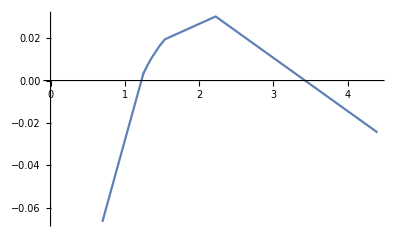

```mathematica
ListLinePlot[{#[[1]],(#[[2]]+1.029898)/-0.821074-#[[1]]}&/@SortBy[inptusDone,First]]
```

```mathematica
form =(*(g m + k  M)/(c m^2 +    m M +  e   M^2)*)(M/m a + b)/(m+M)
aa =-2.34503191/π^(3/2)/((form)/.{m->1.1,M->1.5})
ab=-1.85491225/π^(3/2)/((form)/.{m->1.3,M->2})
ac =-6.760633796/π^(3/2)/((form)/.{m->0.4,M->0.5})
(*ad =-2.51016/π^(3/2)/((form)/.{m->0.4,M->0.5})*)
ae=-1.690233432/π^(3/2)/((form)/.{m->1.6,M->2.})
af =-2.14875797/π^(3/2)/((form)/.{m->0.9,M->2.})
(*ae{m->1.6,M->2.}->SeriesData[ϵ,0,{-1.690233432*Λ^3-0.000117728*pm43*Λ^3,13.257246255*Λ^3-0.000382733*pm44*Λ^3,-57.721235374*Λ^3-0.0014534405*pm45*Λ^3},-1,2,1],{m->0.9,M->2.}->SeriesData[ϵ,0,{-2.14875797*Λ^3-0.00017391*pm52*Λ^3,14.847008038*Λ^3-0.000666703*pm53*Λ^3,-59.7327129885*Λ^3-0.00211091*pm54*Λ^3},-1,2,1]*)
```

((a M)/m+b)/(m+M)

-1.09496/(1.36364 a+b)

-1.09929/(1.53846 a+b)

-1.09271/(1.25 a+b)

-1.09276/(1.25 a+b)

-1.11908/(2.22222 a+b)

```mathematica
harb =NSolve[{aa==ac,ab==ae,ab==ac, ae==af}, {a,b},Reals,WorkingPrecision->1]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{}

```mathematica
(c m^2 +    m M +  e   M^2)/(a m^3 +    b m^2 M +  m M^2+g  M^3)
```

```mathematica
harb =NSolve[{aa==ac,ab==ac,ac ==ad,ad==ae, ae==af}, {c,d,k,e,g},Reals,WorkingPrecision->1]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{}

```mathematica
form/.harb[[1]]//InputForm
```

(m - (2528.3509087281914 - 2208.4502024093435*I)*M)/((-0.6815299232823997 + 0.011569840480240505*I)*m^2 + m*M - (0.36157574797456077 + 0.010061721572071032*I)*M^2)

```mathematica
(m - (num)*M)/((-0.6815299232823997 )*m^2 + m*M - (0.36157574797456077)*M^2)
```

(m-M num)/(-0.68153 m^2+m M-0.361576 M^2)

```mathematica
0.6815/0.3615
```

1.8852

```mathematica
Range[]
```

```mathematica
{m->#[[1]],M->#[[2]]}&/@ Tuples[]
```

9444

```mathematica
outed2= AssociationMap[runForValues[prepped[[-4]],#]&,{{m->1.6,M->2},{m->0.9,M->2},{m->1.5,1.1}}]
gorb ={runForValues[prepped[[-4]],{m->1.3,M->2}],runForValues[prepped[[-4]],{m->0.4,M->0.5}]}
InputForm[gorb]
```

1/(m+M)

-1.09496

-1.09929

-1.09271

```mathematica
-2.34503191/π^(3/2)/((form)/.{m->1.1,M->1.5})
-1.855005212/π^(3/2)/((form)/.{m->1.3,M->2})
-6.760933724/π^(3/2)/((form)/.{m->0.4,M->0.5})
```

-1.09496

-1.09935

-1.09276

```mathematica
?FindFormula
```

```mathematica
(*#->{Length@Cases[#,m,Infinity],Length@Cases[#,M,Infinity],InputForm[#]}&/@Values@remainingAfterRemaps*)~
```

<|loopIntegral(1/((k2^2-m^2).(k3^2-m^2).(k3^2-M^2).((k2+k3)^2-m^2)),{k2,k3})→-(2 (π Λ^2 log((2 m+M)^2/(9 m^2))))/(m^2-M^2)+O(ϵ^1),loopIntegral(1/((k2^2-M^2).(k3^2-m^2).(k3^2-M^2).((k2+k3)^2-m^2)),{k2,k3})→-(2 (π Λ^2 log((m+2 M)^2/(2 m+M)^2)))/(m^2-M^2)+O(ϵ^1)|>

21

```mathematica
remainingOnesHavingFDSed =Select[FDS[#]/.fdsEDEval&/@remainingOnes, Head[#] ===loopIntegral&];
```

```mathematica
remainingOnesHavingFDSed[[2]]
```

loopIntegral(1/((k1^2-M^2).(k2^2-m^2)^2.((k1+k2-p)^2-m^2)),{k1,k2})

```mathematica
remainingOnes2Loop=Select[fdsEDEval, MatchQ[#, loopIntegral[_, {k1,k2}]]&];
remainingOnes3PlusLoop=Select[fdsEDEval,! MatchQ[#, loopIntegral[_, {k1,k2}]]&];
```

```mathematica
{remainingOnes//Length,fdsEDEval//Length,remainingOnes2Loop//Length,remainingOnes3PlusLoop//Length}
```

{42,42,32,10}

```mathematica
#/.loopIntegral[int_, {k1,k2}]:>(loopIntegral[FDS[int], {k1,k2}]/.)&/@remainingOnes2Loop
```

<|loopIntegral(1/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)),{k1,k2})→loopIntegral(1/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)),{k1,k2}),loopIntegral(1/((k1^2-m^2).(k2^2-m^2)^2.((k1+k2-p)^2-m^2)),{k1,k2})→loopIntegral(1/((k1^2-m^2).((k1+k2-p)^2-m^2).(k2^2-m^2)^2),{k1,k2}),loopIntegral(1/((k1^2-M^2).(k2^2-m^2)^2.((k1+k2-p)^2-m^2)),{k1,k2})→loopIntegral(1/((k1^2-M^2).((k1+k2-p)^2-m^2).(k2^2-m^2)^2),{k1,k2}),loopIntegral(1/((k1^2-M^2).(k2^2-M^2)^2.((k1+k2-p)^2-m^2)),{k1,k2})→loopIntegral(1/((k1^2-M^2).((k1+k2-p)^2-m^2).(k2^2-M^2)^2),{k1,k2}),loopIntegral(1/((k1^2-m^2)^2.(k2^2-m^2).((k1-k2)^2-m^2)),{k1,k2})→loopIntegral(1/(((k1-k2)^2-m^2).(k2^2-m^2).(k1^2-m^2)^2),{k1,k2}),loopIntegral(1/((k2^2-m^2).(k3^2-m^2).(k3^2-M^2).((k2+k3)^2-m^2)),{k2,k3})→loopIntegral(1/((k1^2-m^2).(k2^2-m^2).(k2^2-M^2).((k1+k2)^2-m^2)),{k1,k2}),loopIntegral(1/((k2^2-m^2).(k3^2-m^2)^2.((k2+k3)^2-m^2)),{k2,k3})→loopIntegral(1/((k1^2-m^2).((k1+k2)^2-m^2).(k2^2-m^2)^2),{k1,k2}),loopIntegral(1/((k2^2-m^2).(k3^2-M^2)^2.((k2+k3)^2-m^2)),{k2,k3})→loopIntegral(1/((k1^2-m^2).((k1+k2)^2-m^2).(k2^2-M^2)^2),{k1,k2}),loopIntegral(1/((k2^2-M^2).(k3^2-m^2).(k3^2-M^2).((k2+k3)^2-m^2)),{k2,k3})→loopIntegral(1/((k1^2-M^2).(k2^2-m^2).(k2^2-M^2).((k1+k2)^2-m^2)),{k1,k2}),loopIntegral(1/((k2^2-M^2).(k3^2-m^2)^2.((k2+k3)^2-m^2)),{k2,k3})→loopIntegral(1/((k1^2-M^2).((k1+k2)^2-m^2).(k2^2-m^2)^2),{k1,k2}),loopIntegral(1/((k2^2-M^2).(k3^2-M^2)^2.((k2+k3)^2-m^2)),{k2,k3})→loopIntegral(1/((k1^2-M^2).((k1+k2)^2-m^2).(k2^2-M^2)^2),{k1,k2}),loopIntegral(1/((k2^2-M^2).(k3^2-m^2)^2.((k2+k3)^2-M^2)),{k2,k3})→loopIntegral(1/((k1^2-M^2).((k1+k2)^2-M^2).(k2^2-m^2)^2),{k1,k2}),loopIntegral(1/((k1^2-m^2)^2.(k2^2-M^2)^2.((k1-k2)^2-m^2)),{k1,k2})→loopIntegral(1/((k2^2-M^2)^2.((k1-k2)^2-m^2).(k1^2-m^2)^2),{k1,k2}),loopIntegral((k1·k2)/((k1^2-M^2).(k2^2-M^2)^2.((k1+k2-p)^2-m^2)),{k1,k2})→loopIntegral((k1·k2)/((k1^2-M^2).((k1+k2-p)^2-m^2).(k2^2-M^2)^2),{k1,k2}),loopIntegral((k1·k2)/((k1^2-m^2).(k1^2-M^2).(k2^2-m^2)^2.(k2^2-M^2)),{k1,k2})→loopIntegral((k1·k2)/((k2^2-m^2)^2.(k2^2-M^2).(k1^2-m^2).(k1^2-M^2)),{k1,k2}),loopIntegral((k1·k2)/((k1^2-m^2).(k1^2-M^2).(k2^2-m^2).(k2^2-M^2)^2),{k1,k2})→loopIntegral((k1·k2)/((k2^2-M^2)^2.(k2^2-m^2).(k1^2-m^2).(k1^2-M^2)),{k1,k2}),loopIntegral(k2^2/((k1^2-m^2)^2.(k2^2-M^2).((k1-k2)^2-M^2)),{k1,k2})→loopIntegral(k2^2/((k1^2-m^2)^2.((k1-k2)^2-M^2).(k2^2-M^2)),{k1,k2}),loopIntegral(k2^2/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2})→loopIntegral(k2^2/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2}),loopIntegral(k2^2/((k1^2-m^2).(k2^2-m^2)^2.((k1+k2-p)^2-m^2)),{k1,k2})→loopIntegral(k2^2/((k1^2-m^2).((k1+k2-p)^2-m^2).(k2^2-m^2)^2),{k1,k2}),loopIntegral(k2^2/((k1^2-M^2).(k2^2-M^2).((k1+k2-p)^2-m^2)^2),{k1,k2})→loopIntegral(k2^2/((k1^2-M^2).(k2^2-M^2).((k1+k2-p)^2-m^2)^2),{k1,k2}),loopIntegral(k2^2/((k1^2-M^2).(k2^2-M^2)^2.((k1+k2-p)^2-m^2)),{k1,k2})→loopIntegral(k2^2/((k1^2-M^2).((k1+k2-p)^2-m^2).(k2^2-M^2)^2),{k1,k2}),loopIntegral(k2^2/((k1^2-m^2)^2.(k2^2-M^2)^2.((k1-k2)^2-m^2)),{k1,k2})→loopIntegral(k2^2/((k2^2-M^2)^2.((k1-k2)^2-m^2).(k1^2-m^2)^2),{k1,k2}),loopIntegral(k2^2/((k1^2-M^2)^2.(k2^2-M^2)^2.((k1-k2)^2-m^2)),{k1,k2})→loopIntegral(k2^2/((k2^2-M^2)^2.((k1-k2)^2-m^2).(k1^2-M^2)^2),{k1,k2}),loopIntegral(((k1·k2) k2^2)/((k1^2-M^2).(k2^2-M^2).((k1+k2-p)^2-m^2)^2),{k1,k2})→loopIntegral(((k1·k2) k2^2)/((k1^2-M^2).(k2^2-M^2).((k1+k2-p)^2-m^2)^2),{k1,k2}),loopIntegral(((k1·k2) k2^2)/((k1^2-M^2).(k2^2-M^2)^2.((k1+k2-p)^2-m^2)),{k1,k2})→loopIntegral(((k1·k2) k2^2)/((k1^2-M^2).((k1+k2-p)^2-m^2).(k2^2-M^2)^2),{k1,k2}),loopIntegral(((k1·k2) k2^2)/((k1^2-m^2).(k1^2-M^2).(k2^2-m^2)^2.(k2^2-M^2)),{k1,k2})→loopIntegral(((k1·k2) k2^2)/((k2^2-m^2)^2.(k2^2-M^2).(k1^2-m^2).(k1^2-M^2)),{k1,k2}),loopIntegral(((k1·k2) k2^2)/((k1^2-m^2).(k1^2-M^2).(k2^2-m^2).(k2^2-M^2)^2),{k1,k2})→loopIntegral(((k1·k2) k2^2)/((k2^2-M^2)^2.(k2^2-m^2).(k1^2-m^2).(k1^2-M^2)),{k1,k2}),loopIntegral((k2·p)/((k1^2-m^2)^2.(k2^2-M^2).((k1+k2-p)^2-m^2)),{k1,k2})→loopIntegral((k2·p)/((k1^2-m^2)^2.(k2^2-M^2).((k1+k2-p)^2-m^2)),{k1,k2}),loopIntegral((k2·p)/((k1^2-M^2).(k2^2-M^2).((k1+k2-p)^2-m^2)^2),{k1,k2})→loopIntegral((k2·p)/((k1^2-M^2).(k2^2-M^2).((k1+k2-p)^2-m^2)^2),{k1,k2}),loopIntegral(((k1·k2) (k2·p))/((k1^2-M^2).(k2^2-M^2).((k1+k2-p)^2-m^2)^2),{k1,k2})→loopIntegral(((k1·k2) (k2·p))/((k1^2-M^2).(k2^2-M^2).((k1+k2-p)^2-m^2)^2),{k1,k2}),loopIntegral(k3^2/((k2^2-m^2).(k3^2-M^2)^2.((k2+k3)^2-m^2)),{k2,k3})→loopIntegral(k2^2/((k1^2-m^2).((k1+k2)^2-m^2).(k2^2-M^2)^2),{k1,k2}),loopIntegral(k3^2/((k2^2-M^2).(k3^2-M^2)^2.((k2+k3)^2-m^2)),{k2,k3})→loopIntegral(k2^2/((k1^2-M^2).((k1+k2)^2-m^2).(k2^2-M^2)^2),{k1,k2})|>

```mathematica
remainingOnes2Loop
```

<||>

```mathematica
?MatchQ
```

```mathematica
fdsEDEval2=Association@KeyValueMap[loopIntegral[FDS[#[[1]] /.{k1->k2,k2->k1}]->#2&,remainingOnes2];
```

<|2→<|loopIntegral(1/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)),{k1,k2})→loopIntegral(1/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)),{k1,k2}),loopIntegral(1/((k1^2-m^2).((k1+k2-p)^2-m^2).(k2^2-m^2)^2),{k1,k2})→loopIntegral(1/((k1^2-m^2).((k1+k2-p)^2-m^2).(k2^2-m^2)^2),{k1,k2}),loopIntegral(1/((k1^2-M^2).((k1+k2-p)^2-m^2).(k2^2-m^2)^2),{k1,k2})→loopIntegral(1/((k1^2-M^2).((k1+k2-p)^2-m^2).(k2^2-m^2)^2),{k1,k2}),loopIntegral(1/((k1^2-M^2).((k1+k2-p)^2-m^2).(k2^2-M^2)^2),{k1,k2})→loopIntegral(1/((k1^2-M^2).((k1+k2-p)^2-m^2).(k2^2-M^2)^2),{k1,k2}),loopIntegral(1/(((k1-k2)^2-m^2).(k2^2-m^2).(k1^2-m^2)^2),{k1,k2})→loopIntegral(1/(((k1-k2)^2-m^2).(k2^2-m^2).(k1^2-m^2)^2),{k1,k2}),loopIntegral(1/((k2^2-m^2).(k3^2-m^2).(k3^2-M^2).((k2+k3)^2-m^2)),{k2,k3})→loopIntegral(1/((k1^2-m^2).(k2^2-m^2).(k2^2-M^2).((k1+k2)^2-m^2)),{k1,k2}),loopIntegral(1/((k2^2-m^2).((k2+k3)^2-m^2).(k3^2-m^2)^2),{k2,k3})→loopIntegral(1/((k1^2-m^2).((k1+k2)^2-m^2).(k2^2-m^2)^2),{k1,k2}),loopIntegral(1/((k2^2-m^2).((k2+k3)^2-m^2).(k3^2-M^2)^2),{k2,k3})→loopIntegral(1/((k1^2-m^2).((k1+k2)^2-m^2).(k2^2-M^2)^2),{k1,k2}),loopIntegral(1/((k2^2-M^2).(k3^2-m^2).(k3^2-M^2).((k2+k3)^2-m^2)),{k2,k3})→loopIntegral(1/((k1^2-M^2).(k2^2-m^2).(k2^2-M^2).((k1+k2)^2-m^2)),{k1,k2}),loopIntegral(1/((k2^2-M^2).((k2+k3)^2-m^2).(k3^2-m^2)^2),{k2,k3})→loopIntegral(1/((k1^2-M^2).((k1+k2)^2-m^2).(k2^2-m^2)^2),{k1,k2}),loopIntegral(1/((k2^2-M^2).((k2+k3)^2-m^2).(k3^2-M^2)^2),{k2,k3})→loopIntegral(1/((k1^2-M^2).((k1+k2)^2-m^2).(k2^2-M^2)^2),{k1,k2}),loopIntegral(1/((k2^2-M^2).((k2+k3)^2-M^2).(k3^2-m^2)^2),{k2,k3})→loopIntegral(1/((k1^2-M^2).((k1+k2)^2-M^2).(k2^2-m^2)^2),{k1,k2}),loopIntegral(1/((k2^2-M^2)^2.((k1-k2)^2-m^2).(k1^2-m^2)^2),{k1,k2})→loopIntegral(1/((k2^2-M^2)^2.((k1-k2)^2-m^2).(k1^2-m^2)^2),{k1,k2}),loopIntegral((k1·k2)/((k1^2-M^2).((k1+k2-p)^2-m^2).(k2^2-M^2)^2),{k1,k2})→loopIntegral((k1·k2)/((k1^2-M^2).((k1+k2-p)^2-m^2).(k2^2-M^2)^2),{k1,k2}),loopIntegral((k1·k2)/((k2^2-m^2)^2.(k2^2-M^2).(k1^2-m^2).(k1^2-M^2)),{k1,k2})→loopIntegral((k1·k2)/((k2^2-m^2)^2.(k2^2-M^2).(k1^2-m^2).(k1^2-M^2)),{k1,k2}),loopIntegral((k1·k2)/((k2^2-M^2)^2.(k2^2-m^2).(k1^2-m^2).(k1^2-M^2)),{k1,k2})→loopIntegral((k1·k2)/((k2^2-M^2)^2.(k2^2-m^2).(k1^2-m^2).(k1^2-M^2)),{k1,k2}),loopIntegral(k2^2/((k1^2-m^2)^2.((k1-k2)^2-M^2).(k2^2-M^2)),{k1,k2})→loopIntegral(k2^2/((k1^2-m^2)^2.((k1-k2)^2-M^2).(k2^2-M^2)),{k1,k2}),loopIntegral(k2^2/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2})→loopIntegral(k2^2/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2}),loopIntegral(k2^2/((k1^2-m^2).((k1+k2-p)^2-m^2).(k2^2-m^2)^2),{k1,k2})→loopIntegral(k2^2/((k1^2-m^2).((k1+k2-p)^2-m^2).(k2^2-m^2)^2),{k1,k2}),loopIntegral(k2^2/((k1^2-M^2).(k2^2-M^2).((k1+k2-p)^2-m^2)^2),{k1,k2})→loopIntegral(k2^2/((k1^2-M^2).(k2^2-M^2).((k1+k2-p)^2-m^2)^2),{k1,k2}),loopIntegral(k2^2/((k1^2-M^2).((k1+k2-p)^2-m^2).(k2^2-M^2)^2),{k1,k2})→loopIntegral(k2^2/((k1^2-M^2).((k1+k2-p)^2-m^2).(k2^2-M^2)^2),{k1,k2}),loopIntegral(k2^2/((k2^2-M^2)^2.((k1-k2)^2-m^2).(k1^2-m^2)^2),{k1,k2})→loopIntegral(k2^2/((k2^2-M^2)^2.((k1-k2)^2-m^2).(k1^2-m^2)^2),{k1,k2}),loopIntegral(k2^2/((k2^2-M^2)^2.((k1-k2)^2-m^2).(k1^2-M^2)^2),{k1,k2})→loopIntegral(k2^2/((k2^2-M^2)^2.((k1-k2)^2-m^2).(k1^2-M^2)^2),{k1,k2}),loopIntegral(((k1·k2) k2^2)/((k1^2-M^2).(k2^2-M^2).((k1+k2-p)^2-m^2)^2),{k1,k2})→loopIntegral(((k1·k2) k2^2)/((k1^2-M^2).(k2^2-M^2).((k1+k2-p)^2-m^2)^2),{k1,k2}),loopIntegral(((k1·k2) k2^2)/((k1^2-M^2).((k1+k2-p)^2-m^2).(k2^2-M^2)^2),{k1,k2})→loopIntegral(((k1·k2) k2^2)/((k1^2-M^2).((k1+k2-p)^2-m^2).(k2^2-M^2)^2),{k1,k2}),loopIntegral(((k1·k2) k2^2)/((k2^2-m^2)^2.(k2^2-M^2).(k1^2-m^2).(k1^2-M^2)),{k1,k2})→loopIntegral(((k1·k2) k2^2)/((k2^2-m^2)^2.(k2^2-M^2).(k1^2-m^2).(k1^2-M^2)),{k1,k2}),loopIntegral(((k1·k2) k2^2)/((k2^2-M^2)^2.(k2^2-m^2).(k1^2-m^2).(k1^2-M^2)),{k1,k2})→loopIntegral(((k1·k2) k2^2)/((k2^2-M^2)^2.(k2^2-m^2).(k1^2-m^2).(k1^2-M^2)),{k1,k2}),loopIntegral((k2·p)/((k1^2-m^2)^2.(k2^2-M^2).((k1+k2-p)^2-m^2)),{k1,k2})→loopIntegral((k2·p)/((k1^2-m^2)^2.(k2^2-M^2).((k1+k2-p)^2-m^2)),{k1,k2}),loopIntegral((k2·p)/((k1^2-M^2).(k2^2-M^2).((k1+k2-p)^2-m^2)^2),{k1,k2})→loopIntegral((k2·p)/((k1^2-M^2).(k2^2-M^2).((k1+k2-p)^2-m^2)^2),{k1,k2}),loopIntegral(((k1·k2) (k2·p))/((k1^2-M^2).(k2^2-M^2).((k1+k2-p)^2-m^2)^2),{k1,k2})→loopIntegral(((k1·k2) (k2·p))/((k1^2-M^2).(k2^2-M^2).((k1+k2-p)^2-m^2)^2),{k1,k2}),loopIntegral(k3^2/((k2^2-m^2).((k2+k3)^2-m^2).(k3^2-M^2)^2),{k2,k3})→loopIntegral(k2^2/((k1^2-m^2).((k1+k2)^2-m^2).(k2^2-M^2)^2),{k1,k2}),loopIntegral(k3^2/((k2^2-M^2).((k2+k3)^2-m^2).(k3^2-M^2)^2),{k2,k3})→loopIntegral(k2^2/((k1^2-M^2).((k1+k2)^2-m^2).(k2^2-M^2)^2),{k1,k2})|>,3→<|loopIntegral(1/(((k2-k3)^2-m^2).(k3^2-M^2).(k1^2-m^2).(k2^2-m^2).(k2^2-M^2).((k1+k2)^2-m^2)),{k1,k2,k3})→loopIntegral(1/(((k2-k3)^2-m^2).(k3^2-M^2).(k1^2-m^2).(k2^2-m^2).(k2^2-M^2).((k1+k2)^2-m^2)),{k1,k2,k3}),loopIntegral(1/(((k2-k3)^2-M^2).(k3^2-M^2).(k1^2-m^2).((k1+k2)^2-m^2).(k2^2-m^2)^2),{k1,k2,k3})→loopIntegral(1/(((k2-k3)^2-M^2).(k3^2-M^2).(k1^2-m^2).((k1+k2)^2-m^2).(k2^2-m^2)^2),{k1,k2,k3}),loopIntegral(1/(((k1+k2-k3)^2-m^2).(k3^2-M^2).(k1^2-M^2)^2.(k2^2-m^2)^2),{k1,k2,k3})→loopIntegral(1/(((k1+k2-k3)^2-m^2).(k3^2-M^2).(k1^2-M^2)^2.(k2^2-m^2)^2),{k1,k2,k3}),loopIntegral(k2^2/(((k1+k2-k3)^2-m^2).(k3^2-m^2).(k1^2-M^2)^2.(k2^2-M^2)^2),{k1,k2,k3})→loopIntegral(k2^2/(((k1+k2-k3)^2-m^2).(k3^2-m^2).(k1^2-M^2)^2.(k2^2-M^2)^2),{k1,k2,k3}),loopIntegral(k2^2/(((k1+k2-k3)^2-m^2).(k3^2-M^2).(k1^2-m^2)^2.(k2^2-M^2)^2),{k1,k2,k3})→loopIntegral(k2^2/(((k1+k2-k3)^2-m^2).(k3^2-M^2).(k1^2-m^2)^2.(k2^2-M^2)^2),{k1,k2,k3}),loopIntegral((k2·k3)/(((k1+k2-k3)^2-m^2).(k3^2-M^2).(k1^2-m^2)^2.(k2^2-M^2)^2),{k1,k2,k3})→loopIntegral((k2·k3)/(((k1+k2-k3)^2-m^2).(k3^2-M^2).(k1^2-m^2)^2.(k2^2-M^2)^2),{k1,k2,k3}),loopIntegral((k2·k3)/(((k1+k2-k3)^2-m^2).(k3^2-M^2).(k1^2-m^2).(k1^2-M^2).(k2^2-m^2).(k2^2-M^2)),{k1,k2,k3})→loopIntegral((k2·k3)/(((k1+k2-k3)^2-m^2).(k3^2-M^2).(k1^2-m^2).(k1^2-M^2).(k2^2-m^2).(k2^2-M^2)),{k1,k2,k3}),loopIntegral((k2·k3)/(((k1+k2-k3)^2-M^2).(k3^2-M^2).(k1^2-m^2)^2.(k2^2-m^2)^2),{k1,k2,k3})→loopIntegral((k2·k3)/(((k1+k2-k3)^2-M^2).(k3^2-M^2).(k1^2-m^2)^2.(k2^2-m^2)^2),{k1,k2,k3}),loopIntegral(k3^2/(((k2-k3)^2-M^2).(k3^2-M^2).(k1^2-m^2).((k1+k2)^2-m^2).(k2^2-m^2)^2),{k1,k2,k3})→loopIntegral(k3^2/(((k2-k3)^2-M^2).(k3^2-M^2).(k1^2-m^2).((k1+k2)^2-m^2).(k2^2-m^2)^2),{k1,k2,k3}),loopIntegral(k3^2/(((k2-k3)^2-M^2).(k3^2-M^2).(k1^2-M^2).((k1+k2)^2-M^2).(k2^2-m^2)^2),{k1,k2,k3})→loopIntegral(k3^2/(((k2-k3)^2-M^2).(k3^2-M^2).(k1^2-M^2).((k1+k2)^2-M^2).(k2^2-m^2)^2),{k1,k2,k3})|>|>

```mathematica
groupBySize[[1]]//InputForm
```

{loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2, D], m]], {k2}], loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2, D], M]], {k2}], 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k3, D], m]], {k3}], loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k3, D], M]], {k3}], 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m]], {k2}], 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], M]], {k2}], 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2, D], M], PropagatorDenominator[Momentum[k2, D], M]], {k2}], 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k3, D], m], PropagatorDenominator[Momentum[k3, D], m]], {k3}], 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k3, D], m], PropagatorDenominator[Momentum[k3, D], M]], {k3}], 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k3, D], M], PropagatorDenominator[Momentum[k3, D], M]], {k3}], 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m]], 
  {k2}], loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], M], 
   PropagatorDenominator[Momentum[k2, D], M]], {k2}], loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2, D], M], 
   PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m]], {k2}], 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2, D], M], PropagatorDenominator[Momentum[k2, D], M], PropagatorDenominator[Momentum[k2, D], M]], 
  {k2}], loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m]]*Pair[Momentum[k2, D], Momentum[k2, D]], 
  {k2}], loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2, D], M], PropagatorDenominator[Momentum[k2, D], M]]*Pair[Momentum[k2, D], Momentum[k2, D]], 
  {k2}], loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m], 
    PropagatorDenominator[Momentum[k2, D], m]]*Pair[Momentum[k2, D], Momentum[k2, D]], {k2}], 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], M], PropagatorDenominator[Momentum[k2, D], M]]*
   Pair[Momentum[k2, D], Momentum[k2, D]], {k2}], 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2, D], M], PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m]]*
   Pair[Momentum[k2, D], Momentum[k2, D]], {k2}], 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2, D], M], PropagatorDenominator[Momentum[k2, D], M], PropagatorDenominator[Momentum[k2, D], M]]*
   Pair[Momentum[k2, D], Momentum[k2, D]], {k2}], 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2, D], M], PropagatorDenominator[Momentum[k2, D], M], PropagatorDenominator[Momentum[k2, D], M]]*
   Pair[Momentum[k2, D], Momentum[k2, D]]^2, {k2}], 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k3, D], M], PropagatorDenominator[Momentum[k3, D], M]]*Pair[Momentum[k3, D], Momentum[k3, D]], {k3}]}

```mathematica
fridges - what is going on here!
```

fridges-going is on what here!